```mathematica
(*First, we solve for the regular solution for displacement (u)*)
```

```mathematica
fudge[l_,m_]=(-1)^m*Sqrt[(2l+1)(l-m)!/(l+m)!];
```

```mathematica
(* Action of raising and lowerng operators for l *)

ddYdz[l_,m_,θ_,ϕ_]=fudge[l,m]/fudge[l-1,m]*(l+m)*r^(l-1)*SphericalHarmonicY[l-1,m,θ,ϕ]
ddYdp[l_,m_,θ_,ϕ_]=fudge[l,m]/fudge[l-1,m+1]*Sqrt[1/2]*r^(l-1)*SphericalHarmonicY[l-1,m+1,θ,ϕ]
ddYdn[l_,m_,θ_,ϕ_]=fudge[l,m]/fudge[l-1,m-1]*(l+m)*(l+m-1)*Sqrt[1/2]*r^(l-1)*SphericalHarmonicY[l-1,m-1,θ,ϕ]
```

((l+m) r^(-1+l) √(((1+2 l) (l-m)!)/((l+m)!)) SphericalHarmonicY[-1+l,m,θ,ϕ])/(√(((1+2 (-1+l)) (-1+l-m)!)/((-1+l+m)!)))

-(r^(-1+l) √(((1+2 l) (l-m)!)/((l+m)!)) SphericalHarmonicY[-1+l,1+m,θ,ϕ])/(√2 √(((1+2 (-1+l)) (-2+l-m)!)/((l+m)!)))

-((-1+l+m) (l+m) r^(-1+l) √(((1+2 l) (l-m)!)/((l+m)!)) SphericalHarmonicY[-1+l,-1+m,θ,ϕ])/(√2 √(((1+2 (-1+l)) (l-m)!)/((-2+l+m)!)))

```mathematica
(* Built d/dx and d/dy in terms of d/dp and d/dn *)
 ddYdx[l_,m_,θ_,ϕ_]=-Sqrt[1/2]*(ddYdp[l,m,θ,ϕ]-ddYdn[l,m,θ,ϕ]);
ddYdy[l_,m_,θ_,ϕ_]=I*Sqrt[1/2]*(ddYdp[l,m,θ,ϕ]+ddYdn[l,m,θ,ϕ]);
```

```mathematica
(* Here's the function psi *)newpsi[l_,m_,θ_,ϕ_,b1_,b2_,b3_]=Simplify[b1* ddYdx[l+1,m,θ,ϕ]+b2* ddYdy[l+1,m,θ,ϕ]+b3*ddYdz[l+1,m,θ,ϕ]]
```

1/2 r^l √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-(b1 (l+m) (1+l+m) SphericalHarmonicY[l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))-(ⅈ b2 (l+m) (1+l+m) SphericalHarmonicY[l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))+(2 b3 (1+l+m) SphericalHarmonicY[l,m,θ,ϕ])/(√(((1+2 l) (l-m)!)/((l+m)!)))+(b1 SphericalHarmonicY[l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))-(ⅈ b2 SphericalHarmonicY[l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!))))

```mathematica
Clear[ddYdz,ddYdn, ddYdp,ddYdx,ddYdy]
```

```mathematica
(* updated to avoid problem in energy calculation. Equivalent to earlier code. Action of raising and lowerng operators for l *)
ddYdz[l_,m_,θ_,ϕ_]=If[Abs[m]>l-1||l-1<0,0,fudge[l,m]/fudge[l-1,m]*(l+m)*r^(l-1)]*SphericalHarmonicY[l-1,m,θ,ϕ];
ddYdp[l_,m_,θ_,ϕ_]=If[Abs[m+1]>l-1||l-1<0,0,fudge[l,m]/fudge[l-1,m+1]*Sqrt[1/2]*r^(l-1)]*SphericalHarmonicY[l-1,m+1,θ,ϕ];
ddYdn[l_,m_,θ_,ϕ_]=If[Abs[m-1]>l-1||l-1<0,0,fudge[l,m]/fudge[l-1,m-1]*(l+m)*(l+m-1)*Sqrt[1/2]*r^(l-1)]*SphericalHarmonicY[l-1,m-1,θ,ϕ];
```

```mathematica
(* Built d/dx and d/dy in terms of d/dp and d/dn *)
 ddYdx[l_,m_,θ_,ϕ_]=-Sqrt[1/2]*(ddYdp[l,m,θ,ϕ]-ddYdn[l,m,θ,ϕ]);
ddYdy[l_,m_,θ_,ϕ_]=I*Sqrt[1/2]*(ddYdp[l,m,θ,ϕ]+ddYdn[l,m,θ,ϕ]);
```

```mathematica
(* Now grad psi: remove r^l and change Y_l^m to ddYdx or ddYdy or ddYdz *)
DXnewpsi[l_,m_,θ_,ϕ_,b1_,b2_,b3_]=Simplify[1/2  √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-(b1 (l+m) (1+l+m) ddYdx[l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))-(ⅈ b2 (l+m) (1+l+m) ddYdx[l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))+(2 b3 (1+l+m) ddYdx[l,m,θ,ϕ])/(√(((1+2 l) (l-m)!)/((l+m)!)))+(b1 ddYdx[l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))-(ⅈ b2 ddYdx[l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!))))]
DYnewpsi[l_,m_,θ_,ϕ_,b1_,b2_,b3_]=Simplify[1/2  √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-(b1 (l+m) (1+l+m) ddYdy[l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))-(ⅈ b2 (l+m) (1+l+m) ddYdy[l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))+(2 b3 (1+l+m) ddYdy[l,m,θ,ϕ])/(√(((1+2 l) (l-m)!)/((l+m)!)))+(b1 ddYdy[l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))-(ⅈ b2 ddYdy[l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!))))]
DZnewpsi[l_,m_,θ_,ϕ_,b1_,b2_,b3_]=Simplify[1/2  √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-(b1 (l+m) (1+l+m) ddYdz[l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))-(ⅈ b2 (l+m) (1+l+m) ddYdz[l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))+(2 b3 (1+l+m) ddYdz[l,m,θ,ϕ])/(√(((1+2 l) (l-m)!)/((l+m)!)))+(b1 ddYdz[l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))-(ⅈ b2 ddYdz[l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!))))]
```

1/(2 √2)√(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-1/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))b1 (l+m) (1+l+m) (If[1+Abs[-2+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) (l+(-1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(-1+m)-1]] SphericalHarmonicY[-1+l,-2+m,θ,ϕ]-If[1+Abs[m]>l||l<1,0,(fudge[l,-1+m] √(1/2) r^(l-1))/fudge[l-1,(-1+m)+1]] SphericalHarmonicY[-1+l,m,θ,ϕ])-1/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))ⅈ b2 (l+m) (1+l+m) (If[1+Abs[-2+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) (l+(-1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(-1+m)-1]] SphericalHarmonicY[-1+l,-2+m,θ,ϕ]-If[1+Abs[m]>l||l<1,0,(fudge[l,-1+m] √(1/2) r^(l-1))/fudge[l-1,(-1+m)+1]] SphericalHarmonicY[-1+l,m,θ,ϕ])+1/(√(((1+2 l) (l-m)!)/((l+m)!)))2 b3 (1+l+m) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,m] (l+m) (l+m-1) √(1/2) r^(l-1))/fudge[l-1,m-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]-If[1+Abs[1+m]>l||l<1,0,(fudge[l,m] √(1/2) r^(l-1))/fudge[l-1,m+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ])+1/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))b1 (If[1+Abs[m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) (l+(1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(1+m)-1]] SphericalHarmonicY[-1+l,m,θ,ϕ]-If[1+Abs[2+m]>l||l<1,0,(fudge[l,1+m] √(1/2) r^(l-1))/fudge[l-1,(1+m)+1]] SphericalHarmonicY[-1+l,2+m,θ,ϕ])-1/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))ⅈ b2 (If[1+Abs[m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) (l+(1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(1+m)-1]] SphericalHarmonicY[-1+l,m,θ,ϕ]-If[1+Abs[2+m]>l||l<1,0,(fudge[l,1+m] √(1/2) r^(l-1))/fudge[l-1,(1+m)+1]] SphericalHarmonicY[-1+l,2+m,θ,ϕ]))

1/(2 √2)√(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-1/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))ⅈ b1 (l+m) (1+l+m) (If[1+Abs[-2+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) (l+(-1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(-1+m)-1]] SphericalHarmonicY[-1+l,-2+m,θ,ϕ]+If[1+Abs[m]>l||l<1,0,(fudge[l,-1+m] √(1/2) r^(l-1))/fudge[l-1,(-1+m)+1]] SphericalHarmonicY[-1+l,m,θ,ϕ])+1/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))b2 (l+m) (1+l+m) (If[1+Abs[-2+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) (l+(-1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(-1+m)-1]] SphericalHarmonicY[-1+l,-2+m,θ,ϕ]+If[1+Abs[m]>l||l<1,0,(fudge[l,-1+m] √(1/2) r^(l-1))/fudge[l-1,(-1+m)+1]] SphericalHarmonicY[-1+l,m,θ,ϕ])+1/(√(((1+2 l) (l-m)!)/((l+m)!)))2 ⅈ b3 (1+l+m) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,m] (l+m) (l+m-1) √(1/2) r^(l-1))/fudge[l-1,m-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+If[1+Abs[1+m]>l||l<1,0,(fudge[l,m] √(1/2) r^(l-1))/fudge[l-1,m+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ])+1/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))ⅈ b1 (If[1+Abs[m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) (l+(1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(1+m)-1]] SphericalHarmonicY[-1+l,m,θ,ϕ]+If[1+Abs[2+m]>l||l<1,0,(fudge[l,1+m] √(1/2) r^(l-1))/fudge[l-1,(1+m)+1]] SphericalHarmonicY[-1+l,2+m,θ,ϕ])+1/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))b2 (If[1+Abs[m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) (l+(1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(1+m)-1]] SphericalHarmonicY[-1+l,m,θ,ϕ]+If[1+Abs[2+m]>l||l<1,0,(fudge[l,1+m] √(1/2) r^(l-1))/fudge[l-1,(1+m)+1]] SphericalHarmonicY[-1+l,2+m,θ,ϕ]))

1/2 √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-(b1 (l+m) (1+l+m) If[1+Abs[-1+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) r^(l-1))/fudge[l-1,-1+m]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))-(ⅈ b2 (l+m) (1+l+m) If[1+Abs[-1+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) r^(l-1))/fudge[l-1,-1+m]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))+(2 b3 (1+l+m) If[1+Abs[m]>l||l<1,0,(fudge[l,m] (l+m) r^(l-1))/fudge[l-1,m]] SphericalHarmonicY[-1+l,m,θ,ϕ])/(√(((1+2 l) (l-m)!)/((l+m)!)))+(b1 If[1+Abs[1+m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) r^(l-1))/fudge[l-1,1+m]] SphericalHarmonicY[-1+l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))-(ⅈ b2 If[1+Abs[1+m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) r^(l-1))/fudge[l-1,1+m]] SphericalHarmonicY[-1+l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!))))

```mathematica
Clear[M]
```

```mathematica
M[l_]=1/(4(1-ν)(2l-1)-2l)
```

1/(-2 l+4 (-1+2 l) (1-ν))

```mathematica
Clear[newuuxx,newuuyy,newuuzz]
```

```mathematica
(* Putting it together, here are the desired solutions for u_x, u_y, u_z *)
newuuxx[l_,m_,r_,θ_,ϕ_,b1_,b2_,b3_]=Simplify[-M[l+1]*(r^2-R^2)*DXnewpsi[l,m,θ,ϕ,b1,b2,b3]+b1*r^(l+1)SphericalHarmonicY[l+1,m,θ,ϕ]]
newuuyy[l_,m_,r_,θ_,ϕ_,b1_,b2_,b3_]=Simplify[-M[l+1]*(r^2-R^2)*DYnewpsi[l,m,θ,ϕ,b1,b2,b3]+b2*r^(l+1)SphericalHarmonicY[l+1,m,θ,ϕ]]
newuuzz[l_,m_,r_,θ_,ϕ_,b1_,b2_,b3_]=Simplify[-M[l+1]*(r^2-R^2)*DZnewpsi[l,m,θ,ϕ,b1,b2,b3]+b3*r^(l+1)SphericalHarmonicY[l+1,m,θ,ϕ]]
```

-1/(2 √2 (2+l (6-8 ν)-4 ν))(r^2-R^2) √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-1/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))b1 (l+m) (1+l+m) (If[1+Abs[-2+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) (l+(-1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(-1+m)-1]] SphericalHarmonicY[-1+l,-2+m,θ,ϕ]-If[1+Abs[m]>l||l<1,0,(fudge[l,-1+m] √(1/2) r^(l-1))/fudge[l-1,(-1+m)+1]] SphericalHarmonicY[-1+l,m,θ,ϕ])-1/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))ⅈ b2 (l+m) (1+l+m) (If[1+Abs[-2+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) (l+(-1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(-1+m)-1]] SphericalHarmonicY[-1+l,-2+m,θ,ϕ]-If[1+Abs[m]>l||l<1,0,(fudge[l,-1+m] √(1/2) r^(l-1))/fudge[l-1,(-1+m)+1]] SphericalHarmonicY[-1+l,m,θ,ϕ])+1/(√(((1+2 l) (l-m)!)/((l+m)!)))2 b3 (1+l+m) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,m] (l+m) (l+m-1) √(1/2) r^(l-1))/fudge[l-1,m-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]-If[1+Abs[1+m]>l||l<1,0,(fudge[l,m] √(1/2) r^(l-1))/fudge[l-1,m+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ])+1/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))b1 (If[1+Abs[m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) (l+(1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(1+m)-1]] SphericalHarmonicY[-1+l,m,θ,ϕ]-If[1+Abs[2+m]>l||l<1,0,(fudge[l,1+m] √(1/2) r^(l-1))/fudge[l-1,(1+m)+1]] SphericalHarmonicY[-1+l,2+m,θ,ϕ])-1/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))ⅈ b2 (If[1+Abs[m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) (l+(1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(1+m)-1]] SphericalHarmonicY[-1+l,m,θ,ϕ]-If[1+Abs[2+m]>l||l<1,0,(fudge[l,1+m] √(1/2) r^(l-1))/fudge[l-1,(1+m)+1]] SphericalHarmonicY[-1+l,2+m,θ,ϕ]))+b1 r^(1+l) SphericalHarmonicY[1+l,m,θ,ϕ]

-1/(2 √2 (2+l (6-8 ν)-4 ν))(r^2-R^2) √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-1/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))ⅈ b1 (l+m) (1+l+m) (If[1+Abs[-2+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) (l+(-1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(-1+m)-1]] SphericalHarmonicY[-1+l,-2+m,θ,ϕ]+If[1+Abs[m]>l||l<1,0,(fudge[l,-1+m] √(1/2) r^(l-1))/fudge[l-1,(-1+m)+1]] SphericalHarmonicY[-1+l,m,θ,ϕ])+1/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))b2 (l+m) (1+l+m) (If[1+Abs[-2+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) (l+(-1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(-1+m)-1]] SphericalHarmonicY[-1+l,-2+m,θ,ϕ]+If[1+Abs[m]>l||l<1,0,(fudge[l,-1+m] √(1/2) r^(l-1))/fudge[l-1,(-1+m)+1]] SphericalHarmonicY[-1+l,m,θ,ϕ])+1/(√(((1+2 l) (l-m)!)/((l+m)!)))2 ⅈ b3 (1+l+m) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,m] (l+m) (l+m-1) √(1/2) r^(l-1))/fudge[l-1,m-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+If[1+Abs[1+m]>l||l<1,0,(fudge[l,m] √(1/2) r^(l-1))/fudge[l-1,m+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ])+1/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))ⅈ b1 (If[1+Abs[m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) (l+(1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(1+m)-1]] SphericalHarmonicY[-1+l,m,θ,ϕ]+If[1+Abs[2+m]>l||l<1,0,(fudge[l,1+m] √(1/2) r^(l-1))/fudge[l-1,(1+m)+1]] SphericalHarmonicY[-1+l,2+m,θ,ϕ])+1/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))b2 (If[1+Abs[m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) (l+(1+m)-1) √(1/2) r^(l-1))/fudge[l-1,(1+m)-1]] SphericalHarmonicY[-1+l,m,θ,ϕ]+If[1+Abs[2+m]>l||l<1,0,(fudge[l,1+m] √(1/2) r^(l-1))/fudge[l-1,(1+m)+1]] SphericalHarmonicY[-1+l,2+m,θ,ϕ]))+b2 r^(1+l) SphericalHarmonicY[1+l,m,θ,ϕ]

-1/(2 (2+l (6-8 ν)-4 ν))(r^2-R^2) √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (-(b1 (l+m) (1+l+m) If[1+Abs[-1+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) r^(l-1))/fudge[l-1,-1+m]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))-(ⅈ b2 (l+m) (1+l+m) If[1+Abs[-1+m]>l||l<1,0,(fudge[l,-1+m] (l+(-1+m)) r^(l-1))/fudge[l-1,-1+m]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ])/(√(((1+2 l) (1+l-m)!)/((-1+l+m)!)))+(2 b3 (1+l+m) If[1+Abs[m]>l||l<1,0,(fudge[l,m] (l+m) r^(l-1))/fudge[l-1,m]] SphericalHarmonicY[-1+l,m,θ,ϕ])/(√(((1+2 l) (l-m)!)/((l+m)!)))+(b1 If[1+Abs[1+m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) r^(l-1))/fudge[l-1,1+m]] SphericalHarmonicY[-1+l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!)))-(ⅈ b2 If[1+Abs[1+m]>l||l<1,0,(fudge[l,1+m] (l+(1+m)) r^(l-1))/fudge[l-1,1+m]] SphericalHarmonicY[-1+l,1+m,θ,ϕ])/(√(((1+2 l) (-1+l-m)!)/((1+l+m)!))))+b3 r^(1+l) SphericalHarmonicY[1+l,m,θ,ϕ]

```mathematica
(* Gradient by brute force *)
DX:=(Sin[θ]Cos[ϕ]D[#,r]+Cos[θ]Cos[ϕ]/r*D[#,θ]-Sin[ϕ]/Sin[θ]/r*D[#,ϕ])&
DY:=(Sin[θ]Sin[ϕ]D[#,r]+Cos[θ]Sin[ϕ]/r*D[#,θ]+Cos[ϕ]/Sin[θ]/r*D[#,ϕ])&
DZ:=(Cos[θ]*D[#,r]-Sin[θ]/r*D[#,θ])&
```

```mathematica
divergenceuu[l_,m_,r_,θ_,ϕ_,b1_,b2_,b3_]:=DX[newuuxx[l,m,r,θ,ϕ,b1,b2,b3]]+DY[newuuyy[l,m,r,θ,ϕ,b1,b2,b3]]+DZ[newuuzz[l,m,r,θ,ϕ,b1,b2,b3]]
```

```mathematica
(* Now calculate D(D.u)+(1-2ν)D^2u, for (lll, mmm) which should be zero for all lll and mmm *)
mmm=2;
lll=6;
divlll=Simplify[divergenceuu[lll,mmm,r,θ,ϕ,b1,b2,b3]];
graddiv4=Simplify[{DX[divlll],DY[divlll],DZ[divlll]}];
lap4=Simplify[Simplify[{Laplacian[newuuxx[lll,mmm,r,θ,ϕ,b1,b2,b3],{r,θ,ϕ},"Spherical"],Laplacian[newuuyy[lll,mmm,r,θ,ϕ,b1,b2,b3],{r,θ,ϕ},"Spherical"],Laplacian[newuuzz[lll,mmm,r,θ,ϕ,b1,b2,b3],{r,θ,ϕ},"Spherical"]}]];
FullSimplify[graddiv4+(1-2ν)*lap4] (* should be {0,0,0} and it is *)
```

{0,0,0}

```mathematica
(* at the surface -- r=R -- notice the l-1 *)
TraditionalForm[newuuxx[l-1,m,R,θ,ϕ,Subscript[S, x]/R^(l),Subscript[S, y]/R^(l),Subscript[S, z]/R^(l)]]
TraditionalForm[newuuyy[l-1,m,R,θ,ϕ,Subscript[S, x]/R^(l),Subscript[S, y]/R^(l),Subscript[S, z]/R^(l)]]
TraditionalForm[newuuzz[l-1,m,R,θ,ϕ,Subscript[S, x]/R^(l),Subscript[S, y]/R^(l),Subscript[S, z]/R^(l)]]
```

S_x Y_l^m(θ,ϕ)

S_y Y_l^m(θ,ϕ)

S_z Y_l^m(θ,ϕ)

```mathematica
(* Now about the BCs themselves *)
```

```mathematica
(* rhat expressed as spherical harmonics *)
rhat[θ_,ϕ_,one_,zero_,minus_]={(SphericalHarmonicY[1,one,θ,ϕ]-SphericalHarmonicY[1,minus,θ,ϕ])/(-√(3/(2 π)) ),(SphericalHarmonicY[1,one,θ,ϕ]+SphericalHarmonicY[1,minus,θ,ϕ])/(-ⅈ √(3/(2 π))),SphericalHarmonicY[1,zero,θ,ϕ]/(1/2 √(3/π))}
```

{-√((2 π)/3) (-SphericalHarmonicY[1,minus,θ,ϕ]+SphericalHarmonicY[1,one,θ,ϕ]),ⅈ √((2 π)/3) (SphericalHarmonicY[1,minus,θ,ϕ]+SphericalHarmonicY[1,one,θ,ϕ]),2 √(π/3) SphericalHarmonicY[1,zero,θ,ϕ]}

```mathematica
ExpToTrig[rhat[θ,ϕ,1,0,-1]] (* check that rhat is correct *)
```

{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}

```mathematica
(* Product of Y_lm and Y_1m' *)
ProductY11Ylm[l_,m_,θ_,ϕ_]=Assuming[l≥1&&l∈Integers&&-2 m∈Integers&&m∈Integers&&2 m∈Integers&&l≥1&&l≥2+m&&l+m≥0,(-1)^(m+1) Sum[Sqrt[(2l+1)3(2L+1)/4/π]*ThreeJSymbol[{L,-m-1},{l,m},{1,1}]*ThreeJSymbol[{L,0},{l,0},{1,0}]*SphericalHarmonicY[L,m+1,θ,ϕ],{L,l-1,l+1}] ]
(* -1^(m+1) at the beginning added to get right answer!! *)

ProductY10Ylm[l_,m_,θ_,ϕ_]=Assuming[l≥1&&l∈Integers&&-2 m∈Integers&&m∈Integers&&2 m∈Integers&&l≥1&&l≥2+m&&l+m≥0, (-1)^m Sum[Sqrt[(2l+1)3(2L+1)/4/π]*ThreeJSymbol[{L,-m},{l,m},{1,0}]*ThreeJSymbol[{L,0},{l,0},{1,0}]*SphericalHarmonicY[L,m,θ,ϕ],{L,l-1,l+1}] ]

ProductY1n1Ylm[l_,m_,θ_,ϕ_]=Assuming[l≥1&&l∈Integers&&-2 m∈Integers&&m∈Integers&&2 m∈Integers&&l≥1&&l≥2+m&&l+m≥0,(-1)^(m+1) Sum[Sqrt[(2l+1)3(2L+1)/4/π]*ThreeJSymbol[{L,-m+1},{l,m},{1,-1}]*ThreeJSymbol[{L,0},{l,0},{1,0}]*SphericalHarmonicY[L,m-1,θ,ϕ],{L,l-1,l+1}] ]
```

(-1)^(1+m) (1/2 √((1+2 (-1+l)) (1+2 l)) √(3/π) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2+m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,1+m,θ,ϕ]+1/2 √((1+2 l) (1+2 (1+l))) √(3/π) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[1+l,1+m,θ,ϕ])

(-1)^m (1/2 √((1+2 (-1+l)) (1+2 l)) √(3/π) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{(-1)^(-l-m) √(((l-m) (l+m))/(l (-1+2 l) (1+2 l))), l≥1&&l≥1+m&&l+m≥1}, {0, True}}]) SphericalHarmonicY[-1+l,m,θ,ϕ]+1/2 √((1+2 l) (1+2 (1+l))) √(3/π) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{(-1)^(1+l+m) √(((1+l-m) (1+l+m))/((1+l) (1+2 l) (3+2 l))), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[1+l,m,θ,ϕ])

(-1)^(1+m) (1/2 √((1+2 (-1+l)) (1+2 l)) √(3/π) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥m&&l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+1/2 √((1+2 l) (1+2 (1+l))) √(3/π) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[1+l,-1+m,θ,ϕ])

```mathematica
(* Check the 3j symbols are correct -- calculate 1's*)
lll
mmm
Simplify[ProductY10Ylm[lll,mmm,θ,ϕ]/SphericalHarmonicY[1,0,θ,ϕ]/SphericalHarmonicY[lll,mmm,θ,ϕ]]
Simplify[ProductY11Ylm[lll,mmm,θ,ϕ]/SphericalHarmonicY[1,1,θ,ϕ]/SphericalHarmonicY[lll,mmm,θ,ϕ]]
Simplify[ProductY1n1Ylm[lll,mmm,θ,ϕ]/SphericalHarmonicY[1,-1,θ,ϕ]/SphericalHarmonicY[lll,mmm,θ,ϕ]]
```

6

2

1

1

1

```mathematica
(* Now calculate the vector displacement for a spherical harmonic shape assuming the displacement is radial *)
```

```mathematica
Shape1A[l_,m_,θ_,ϕ_,one_,zero_,minus_]=Expand[(SphericalHarmonicY[l,m,θ,ϕ]+(-1)^m*SphericalHarmonicY[l,-m,θ,ϕ])/Sqrt[2]*rhat[ θ,ϕ,one,zero,minus]](* positive "m" *)
```

{(-1)^m √(π/3) SphericalHarmonicY[1,minus,θ,ϕ] SphericalHarmonicY[l,-m,θ,ϕ]+(-1)^(1+m) √(π/3) SphericalHarmonicY[1,one,θ,ϕ] SphericalHarmonicY[l,-m,θ,ϕ]+√(π/3) SphericalHarmonicY[1,minus,θ,ϕ] SphericalHarmonicY[l,m,θ,ϕ]-√(π/3) SphericalHarmonicY[1,one,θ,ϕ] SphericalHarmonicY[l,m,θ,ϕ],ⅈ (-1)^m √(π/3) SphericalHarmonicY[1,minus,θ,ϕ] SphericalHarmonicY[l,-m,θ,ϕ]+ⅈ (-1)^m √(π/3) SphericalHarmonicY[1,one,θ,ϕ] SphericalHarmonicY[l,-m,θ,ϕ]+ⅈ √(π/3) SphericalHarmonicY[1,minus,θ,ϕ] SphericalHarmonicY[l,m,θ,ϕ]+ⅈ √(π/3) SphericalHarmonicY[1,one,θ,ϕ] SphericalHarmonicY[l,m,θ,ϕ],(-1)^m √((2 π)/3) SphericalHarmonicY[1,zero,θ,ϕ] SphericalHarmonicY[l,-m,θ,ϕ]+√((2 π)/3) SphericalHarmonicY[1,zero,θ,ϕ] SphericalHarmonicY[l,m,θ,ϕ]}

```mathematica
(* re-express the surface displacement as product functions *)
```

```mathematica
Shape1[l_,m_,θ_,ϕ_]=Simplify[{(-1)^m √(π/3) ProductY1n1Ylm[l,-m,θ,ϕ]+(-1)^(1+m) √(π/3) ProductY11Ylm[l,-m,θ,ϕ]+√(π/3) ProductY1n1Ylm[l,m,θ,ϕ]-√(π/3) ProductY11Ylm[l,m,θ,ϕ],ⅈ (-1)^m √(π/3) ProductY1n1Ylm[l,-m,θ,ϕ]+ⅈ (-1)^m √(π/3) ProductY11Ylm[l,-m,θ,ϕ]+ⅈ √(π/3) ProductY1n1Ylm[l,m,θ,ϕ]+ⅈ √(π/3) ProductY11Ylm[l,m,θ,ϕ],(-1)^m √((2 π)/3) ProductY10Ylm[l,-m,θ,ϕ]+√((2 π)/3) ProductY10Ylm[l,m,θ,ϕ]},Assumptions->l>=1&&-l<=m<=l]
```

{1/2 ((-1)^(1-l) √l (Piecewise[{{(-1)^(-l+m) √((-l+l^2+m-2 l m+m^2)/(-2 l+8 l^3)), l≥2+m}, {0, True}}]) SphericalHarmonicY[-1+l,-1-m,θ,ϕ]+(-1)^-l √l (Piecewise[{{(-1)^(-l+m) √(((-1+l+m) (l+m))/(-2 l+8 l^3)), l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,1-m,θ,ϕ]+(-1)^(1-l+m) √l (Piecewise[{{(-1)^(-l-m) √(((-1+l+m) (l+m))/(-2 l+8 l^3)), l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+(-1)^(-l+m) √l (Piecewise[{{(-1)^(-l-m) √((-l+l^2+m-2 l m+m^2)/(-2 l+8 l^3)), l≥2+m}, {0, True}}]) SphericalHarmonicY[-1+l,1+m,θ,ϕ]+((-1)^(2 l-m) √((1+l+m) (2+l+m)) SphericalHarmonicY[1+l,-1-m,θ,ϕ])/(√(6+16 l+8 l^2))+((-1)^(1+2 l-m) SphericalHarmonicY[1+l,1-m,θ,ϕ])/(√((6+16 l+8 l^2)/(2+3 l+l^2-3 m-2 l m+m^2)))+((-1)^(2 (l+m)) SphericalHarmonicY[1+l,-1+m,θ,ϕ])/(√((6+16 l+8 l^2)/(2+3 l+l^2-3 m-2 l m+m^2)))+((-1)^(1+2 l+2 m) √((1+l+m) (2+l+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ])/(√(6+16 l+8 l^2))),-1/2 ⅈ ((-1)^-l √l (Piecewise[{{(-1)^(-l+m) √((-l+l^2+m-2 l m+m^2)/(-2 l+8 l^3)), l≥2+m}, {0, True}}]) SphericalHarmonicY[-1+l,-1-m,θ,ϕ]+(-1)^-l √l (Piecewise[{{(-1)^(-l+m) √(((-1+l+m) (l+m))/(-2 l+8 l^3)), l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,1-m,θ,ϕ]+(-1)^(-l+m) √l (Piecewise[{{(-1)^(-l-m) √(((-1+l+m) (l+m))/(-2 l+8 l^3)), l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+(-1)^(-l+m) √l (Piecewise[{{(-1)^(-l-m) √((-l+l^2+m-2 l m+m^2)/(-2 l+8 l^3)), l≥2+m}, {0, True}}]) SphericalHarmonicY[-1+l,1+m,θ,ϕ]+((-1)^(1+2 l-m) √((1+l+m) (2+l+m)) SphericalHarmonicY[1+l,-1-m,θ,ϕ])/(√(6+16 l+8 l^2))+((-1)^(1+2 l-m) SphericalHarmonicY[1+l,1-m,θ,ϕ])/(√((6+16 l+8 l^2)/(2+3 l+l^2-3 m-2 l m+m^2)))+((-1)^(1+2 l+2 m) SphericalHarmonicY[1+l,-1+m,θ,ϕ])/(√((6+16 l+8 l^2)/(2+3 l+l^2-3 m-2 l m+m^2)))+((-1)^(1+2 l+2 m) √((1+l+m) (2+l+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ])/(√(6+16 l+8 l^2))),1/(√2)(-1)^(-l-m) ((-1)^m √l (Piecewise[{{(-1)^(-l+m) √(-(l^2-m^2)/(l-4 l^3)), l+m≥1&&l≥1+m}, {0, True}}]) SphericalHarmonicY[-1+l,-m,θ,ϕ]+(-1)^(2 m) √l (Piecewise[{{(-1)^(-l-m) √(-(l^2-m^2)/(l-4 l^3)), l≥1+m&&l+m≥1}, {0, True}}]) SphericalHarmonicY[-1+l,m,θ,ϕ]+(-1)^(3 l) √((1+2 l+l^2-m^2)/(3+8 l+4 l^2)) (SphericalHarmonicY[1+l,-m,θ,ϕ]+(-1)^(3 m) SphericalHarmonicY[1+l,m,θ,ϕ]))}

```mathematica
(* Check -- calculate 1's again *)
Simplify[Shape1A[lll,mmm,θ,ϕ,1,0,-1]/Shape1[lll,mmm,θ,ϕ]]
```

{1,1,1}

```mathematica
(* Pick out the amplitude of each component of the surface spherical harmonic displacement given the shape specified above. Notice that a factor of R is dropped from the boundary condition and will be included later. *)
SXnnn=g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[-1+l,-1-m,θ,ϕ],1];
SXnnp=g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[-1+l,-m+1,θ,ϕ],1];
SXnpn=g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[-1+l,m-1,θ,ϕ],1];
SXpnn=g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[1+l,-m-1,θ,ϕ],1];
SXppn=g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[1+l,m-1,θ,ϕ],1];
SXnpp=g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[-1+l,m+1,θ,ϕ],1];
SXpnp=g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[1+l,-m+1,θ,ϕ],1];
SXppp=g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[1+l,m+1,θ,ϕ],1];

SYnnn=g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[-1+l,-1-m,θ,ϕ],1];
SYnnp=g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[-1+l,-m+1,θ,ϕ],1];
SYnpn=g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[-1+l,m-1,θ,ϕ],1];
SYpnn=g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[1+l,-m-1,θ,ϕ],1];
SYppn=g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[1+l,m-1,θ,ϕ],1];
SYnpp=g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[-1+l,m+1,θ,ϕ],1];
SYpnp=g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[1+l,-m+1,θ,ϕ],1];
SYppp=g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[1+l,m+1,θ,ϕ],1];

SZnn=g*Coefficient[Shape1[l,m,θ,ϕ][[3]],SphericalHarmonicY[-1+l,-m,θ,ϕ],1];
SZnp=g*Coefficient[Shape1[l,m,θ,ϕ][[3]],SphericalHarmonicY[-1+l,m,θ,ϕ],1];
SZpn=g*Coefficient[Shape1[l,m,θ,ϕ][[3]],SphericalHarmonicY[1+l,-m,θ,ϕ],1];
SZpp=g*Coefficient[Shape1[l,m,θ,ϕ][[3]],SphericalHarmonicY[1+l,m,θ,ϕ],1];
```

```mathematica
uxnnn=newuuxx[l-2,-m-1,R,θ,ϕ,SXnnn/R^(l-1),SYnnn/R^(l-1),0];
uxnnp=newuuxx[l-2,-m+1,R,θ,ϕ,SXnnp/R^(l-1),SYnnp/R^(l-1),0];
uxnpn=newuuxx[l-2,m-1,R,θ,ϕ,SXnpn/R^(l-1),SYnpn/R^(l-1),0];
uxnpp=newuuxx[l-2,m+1,R,θ,ϕ,SXnpp/R^(l-1),SYnpp/R^(l-1),0];

uxpnn=newuuxx[l,-m-1,R,θ,ϕ,SXpnn/R^(l+1),SYpnn/R^(l+1),0];
uxpnp=newuuxx[l,-m+1,R,θ,ϕ,SXpnp/R^(l+1),SYpnp/R^(l+1),0];
uxppn=newuuxx[l,m-1,R,θ,ϕ,SXppn/R^(l+1),SYppn/R^(l+1),0];
uxppp=newuuxx[l,m+1,R,θ,ϕ,SXppp/R^(l+1),SYppp/R^(l+1),0];

uxnn=newuuxx[l-2,-m,R,θ,ϕ,0,0,SZnn/R^(l-1)];
uxnp=newuuxx[l-2,m,R,θ,ϕ,0,0,SZnp/R^(l-1)];
uxpn=newuuxx[l,-m,R,θ,ϕ,0,0,SZpn/R^(l+1)];
uxpp=newuuxx[l,m,R,θ,ϕ,0,0,SZpp/R^(l+1)];
```

```mathematica
uynnn=newuuyy[l-2,-m-1,R,θ,ϕ,SXnnn/R^(l-1),SYnnn/R^(l-1),0];
uynnp=newuuyy[l-2,-m+1,R,θ,ϕ,SXnnp/R^(l-1),SYnnp/R^(l-1),0];
uynpn=newuuyy[l-2,m-1,R,θ,ϕ,SXnpn/R^(l-1),SYnpn/R^(l-1),0];
uynpp=newuuyy[l-2,m+1,R,θ,ϕ,SXnpp/R^(l-1),SYnpp/R^(l-1),0];

uypnn=newuuyy[l,-m-1,R,θ,ϕ,SXpnn/R^(l+1),SYpnn/R^(l+1),0];
uypnp=newuuyy[l,-m+1,R,θ,ϕ,SXpnp/R^(l+1),SYpnp/R^(l+1),0];
uyppn=newuuyy[l,m-1,R,θ,ϕ,SXppn/R^(l+1),SYppn/R^(l+1),0];
uyppp=newuuyy[l,m+1,R,θ,ϕ,SXppp/R^(l+1),SYppp/R^(l+1),0];

uynn=newuuyy[l-2,-m,R,θ,ϕ,0,0,SZnn/R^(l-1)];
uynp=newuuyy[l-2,m,R,θ,ϕ,0,0,SZnp/R^(l-1)];
uypn=newuuyy[l,-m,R,θ,ϕ,0,0,SZpn/R^(l+1)];
uypp=newuuyy[l,m,R,θ,ϕ,0,0,SZpp/R^(l+1)];
```

```mathematica
uznnn=newuuzz[l-2,-m-1,R,θ,ϕ,SXnnn/R^(l-1),SYnnn/R^(l-1),0];
uznnp=newuuzz[l-2,-m+1,R,θ,ϕ,SXnnp/R^(l-1),SYnnp/R^(l-1),0];
uznpn=newuuzz[l-2,m-1,R,θ,ϕ,SXnpn/R^(l-1),SYnpn/R^(l-1),0];
uznpp=newuuzz[l-2,m+1,R,θ,ϕ,SXnpp/R^(l-1),SYnpp/R^(l-1),0];

uzpnn=newuuzz[l,-m-1,R,θ,ϕ,SXpnn/R^(l+1),SYpnn/R^(l+1),0];
uzpnp=newuuzz[l,-m+1,R,θ,ϕ,SXpnp/R^(l+1),SYpnp/R^(l+1),0];
uzppn=newuuzz[l,m-1,R,θ,ϕ,SXppn/R^(l+1),SYppn/R^(l+1),0];
uzppp=newuuzz[l,m+1,R,θ,ϕ,SXppp/R^(l+1),SYppp/R^(l+1),0];

uznn=newuuzz[l-2,-m,R,θ,ϕ,0,0,SZnn/R^(l-1)];
uznp=newuuzz[l-2,m,R,θ,ϕ,0,0,SZnp/R^(l-1)];
uzpn=newuuzz[l,-m,R,θ,ϕ,0,0,SZpn/R^(l+1)];
uzpp=newuuzz[l,m,R,θ,ϕ,0,0,SZpp/R^(l+1)];
```

```mathematica
(* Now compare the surface displacement from u with the displacement from the original shape *)
```

```mathematica
(* displacement from u *)
shape1check[l_,m_,θ_,ϕ_]=uxnnn+uxnnp+uxnpn+uxnpp+uxpnn+uxpnp+uxppn+uxppp;
shape2check[l_,m_,θ_,ϕ_]=uynnn+uynnp+uynpn+uynpp+uypnn+uypnp+uyppn+uyppp;
shape3check[l_,m_,θ_,ϕ_]=uznn+uznp+uzpn+uzpp;
```

```mathematica
(* Check by dividing one by the other *)
Simplify[Shape1[4,2,θ,ϕ][[1]]/shape1check[4,2,θ,ϕ]]
Simplify[Shape1[4,2,θ,ϕ][[2]]/shape2check[4,2,θ,ϕ]]
Simplify[Shape1[4,2,θ,ϕ][[3]]/shape3check[4,2,θ,ϕ]]
```

1/g

1/g

1/g

```mathematica
(* Now we know the BCs are satisfied, we put back in the r-dependence *)

uxnnn=newuuxx[l-2,-m-1,r,θ,ϕ,SXnnn/R^(l-1),SYnnn/R^(l-1),0];
uxnnp=newuuxx[l-2,-m+1,r,θ,ϕ,SXnnp/R^(l-1),SYnnp/R^(l-1),0];
uxnpn=newuuxx[l-2,m-1,r,θ,ϕ,SXnpn/R^(l-1),SYnpn/R^(l-1),0];
uxnpp=newuuxx[l-2,m+1,r,θ,ϕ,SXnpp/R^(l-1),SYnpp/R^(l-1),0];

uxpnn=newuuxx[l,-m-1,r,θ,ϕ,SXpnn/R^(l+1),SYpnn/R^(l+1),0];
uxpnp=newuuxx[l,-m+1,r,θ,ϕ,SXpnp/R^(l+1),SYpnp/R^(l+1),0];
uxppn=newuuxx[l,m-1,r,θ,ϕ,SXppn/R^(l+1),SYppn/R^(l+1),0];
uxppp=newuuxx[l,m+1,r,θ,ϕ,SXppp/R^(l+1),SYppp/R^(l+1),0];

uxnn=newuuxx[l-2,-m,r,θ,ϕ,0,0,SZnn/R^(l-1)];
uxnp=newuuxx[l-2,m,r,θ,ϕ,0,0,SZnp/R^(l-1)];
uxpn=newuuxx[l,-m,r,θ,ϕ,0,0,SZpn/R^(l+1)];
uxpp=newuuxx[l,m,r,θ,ϕ,0,0,SZpp/R^(l+1)];

uynnn=newuuyy[l-2,-m-1,r,θ,ϕ,SXnnn/R^(l-1),SYnnn/R^(l-1),0];
uynnp=newuuyy[l-2,-m+1,r,θ,ϕ,SXnnp/R^(l-1),SYnnp/R^(l-1),0];
uynpn=newuuyy[l-2,m-1,r,θ,ϕ,SXnpn/R^(l-1),SYnpn/R^(l-1),0];
uynpp=newuuyy[l-2,m+1,r,θ,ϕ,SXnpp/R^(l-1),SYnpp/R^(l-1),0];

uypnn=newuuyy[l,-m-1,r,θ,ϕ,SXpnn/R^(l+1),SYpnn/R^(l+1),0];
uypnp=newuuyy[l,-m+1,r,θ,ϕ,SXpnp/R^(l+1),SYpnp/R^(l+1),0];
uyppn=newuuyy[l,m-1,r,θ,ϕ,SXppn/R^(l+1),SYppn/R^(l+1),0];
uyppp=newuuyy[l,m+1,r,θ,ϕ,SXppp/R^(l+1),SYppp/R^(l+1),0];

uynn=newuuyy[l-2,-m,r,θ,ϕ,0,0,SZnn/R^(l-1)];
uynp=newuuyy[l-2,m,r,θ,ϕ,0,0,SZnp/R^(l-1)];
uypn=newuuyy[l,-m,r,θ,ϕ,0,0,SZpn/R^(l+1)];
uypp=newuuyy[l,m,r,θ,ϕ,0,0,SZpp/R^(l+1)];

uznnn=newuuzz[l-2,-m-1,r,θ,ϕ,SXnnn/R^(l-1),SYnnn/R^(l-1),0];
uznnp=newuuzz[l-2,-m+1,r,θ,ϕ,SXnnp/R^(l-1),SYnnp/R^(l-1),0];
uznpn=newuuzz[l-2,m-1,r,θ,ϕ,SXnpn/R^(l-1),SYnpn/R^(l-1),0];
uznpp=newuuzz[l-2,m+1,r,θ,ϕ,SXnpp/R^(l-1),SYnpp/R^(l-1),0];

uzpnn=newuuzz[l,-m-1,r,θ,ϕ,SXpnn/R^(l+1),SYpnn/R^(l+1),0];
uzpnp=newuuzz[l,-m+1,r,θ,ϕ,SXpnp/R^(l+1),SYpnp/R^(l+1),0];
uzppn=newuuzz[l,m-1,r,θ,ϕ,SXppn/R^(l+1),SYppn/R^(l+1),0];
uzppp=newuuzz[l,m+1,r,θ,ϕ,SXppp/R^(l+1),SYppp/R^(l+1),0];

uznn=newuuzz[l-2,-m,r,θ,ϕ,0,0,SZnn/R^(l-1)];
uznp=newuuzz[l-2,m,r,θ,ϕ,0,0,SZnp/R^(l-1)];
uzpn=newuuzz[l,-m,r,θ,ϕ,0,0,SZpn/R^(l+1)];
uzpp=newuuzz[l,m,r,θ,ϕ,0,0,SZpp/R^(l+1)];
```

```mathematica
finalanswer1=uxnnn+uxnnp+uxnpn+uxnpp+uxpnn+uxpnp+uxppn+uxppp+uxnn+uxnp+uxpn+uxpp;
finalanswer2=uynnn+uynnp+uynpn+uynpp+uypnn+uypnp+uyppn+uyppp+uynn+uynp+uypn+uypp;
finalanswer3=uznnn+uznnp+uznpn+uznpp+uzpnn+uzpnp+uzppn+uzppp+uznn+uznp+uzpn+uzpp;
```

```mathematica
ux1[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=finalanswer1;
uy1[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=finalanswer2;
uz1[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=finalanswer3;
```

```mathematica
(* We see that in all evaluations the Y_l-3,m-terms vanish. So we remove them. *)
```

```mathematica
uxnew[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=(g √((1+2 (-1+l)) (1+2 l)) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (l+m)!)/((-2+l-m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥-m&&l-m≥2}, {0, True}}]) (If[1+Abs[-1-m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1-m)] ((-2+l)+(1+(-1-m))) ((-2+l)+(1+(-1-m))-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(1+(-1-m))-1]] *0*SphericalHarmonicY[-3+l,-1-m,θ,ϕ]-If[1+Abs[1-m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1-m)] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(1+(-1-m))+1]] *0*SphericalHarmonicY[-3+l,1-m,θ,ϕ]))/(2 √2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l+m)!)/((-2+l-m)!)))+(g √((1+2 (-1+l)) (1+2 l)) (-1+l-m) (l-m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-2+l+m)!)/((l-m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2-m&&l-m≥0}, {0, True}}]) (If[1+Abs[-1-m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1-m)] ((-2+l)+(-1+(1-m))) ((-2+l)+(-1+(1-m))-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(-1+(1-m))-1]] *0*SphericalHarmonicY[-3+l,-1-m,θ,ϕ]-If[1+Abs[1-m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1-m)] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(-1+(1-m))+1]] *0*SphericalHarmonicY[-3+l,1-m,θ,ϕ]))/(2 √2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l+m)!)/((-2+l-m)!)))-(g √((1+2 (-1+l)) (1+2 l)) (-1+l-m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-1+l+m)!)/((-1+l-m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{(-1)^(-l+m) √(((l-m) (l+m))/(l (-1+2 l) (1+2 l))), l≥1&&l≥1-m&&l-m≥1}, {0, True}}]) (If[1+Abs[-1-m]>-2+l||-2+l<1,0,(fudge[-2+l,-m] ((-2+l)-m) ((-2+l)-m-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,-m-1]] *0*SphericalHarmonicY[-3+l,-1-m,θ,ϕ]-If[1+Abs[1-m]>-2+l||-2+l<1,0,(fudge[-2+l,-m] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,-m+1]] *0*SphericalHarmonicY[-3+l,1-m,θ,ϕ]))/(2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l+m)!)/((-2+l-m)!)))+((-1)^m g √((1+2 (-1+l)) (1+2 l)) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (l-m)!)/((-2+l+m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥m&&l+m≥2}, {0, True}}]) (If[1+Abs[-1+m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1+m)] ((-2+l)+(1+(-1+m))) ((-2+l)+(1+(-1+m))-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(1+(-1+m))-1]] *0*SphericalHarmonicY[-3+l,-1+m,θ,ϕ]-If[1+Abs[1+m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1+m)] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(1+(-1+m))+1]] *0*SphericalHarmonicY[-3+l,1+m,θ,ϕ]))/(2 √2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l-m)!)/((-2+l+m)!)))-((-1)^m g √((1+2 (-1+l)) (1+2 l)) (-1+l+m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-1+l-m)!)/((-1+l+m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{(-1)^(-l-m) √(((l-m) (l+m))/(l (-1+2 l) (1+2 l))), l≥1&&l≥1+m&&l+m≥1}, {0, True}}]) (If[1+Abs[-1+m]>-2+l||-2+l<1,0,(fudge[-2+l,m] ((-2+l)+m) ((-2+l)+m-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,m-1]] *0*SphericalHarmonicY[-3+l,-1+m,θ,ϕ]-If[1+Abs[1+m]>-2+l||-2+l<1,0,(fudge[-2+l,m] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,m+1]] *0*SphericalHarmonicY[-3+l,1+m,θ,ϕ]))/(2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l-m)!)/((-2+l+m)!)))+((-1)^m g √((1+2 (-1+l)) (1+2 l)) (-1+l+m) (l+m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-2+l-m)!)/((l+m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2+m&&l+m≥0}, {0, True}}]) (If[1+Abs[-1+m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1+m)] ((-2+l)+(-1+(1+m))) ((-2+l)+(-1+(1+m))-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(-1+(1+m))-1]] *0*SphericalHarmonicY[-3+l,-1+m,θ,ϕ]-If[1+Abs[1+m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1+m)] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(-1+(1+m))+1]] *0*SphericalHarmonicY[-3+l,1+m,θ,ϕ]))/(2 √2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l-m)!)/((-2+l+m)!)))-1/2 g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥-m&&l-m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,-1-m,θ,ϕ]+1/2 g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,1-m,θ,ϕ]+(g √((1+2 l) (1+2 (1+l))) R^(-1-l) (r^2-R^2) √(((3+2 l) (2+l+m)!)/((l-m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) (If[1+Abs[-1-m]>l||l<1,0,(fudge[l,1+(-1-m)] (l+(1+(-1-m))) (l+(1+(-1-m))-1) √(1/2) r^(l-1))/fudge[l-1,(1+(-1-m))-1]] SphericalHarmonicY[-1+l,-1-m,θ,ϕ]-If[1+Abs[1-m]>l||l<1,0,(fudge[l,1+(-1-m)] √(1/2) r^(l-1))/fudge[l-1,(1+(-1-m))+1]] SphericalHarmonicY[-1+l,1-m,θ,ϕ]))/(2 √2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l+m)!)/((l-m)!)))+(g √((1+2 l) (1+2 (1+l))) (1+l-m) (2+l-m) R^(-1-l) (r^2-R^2) √(((3+2 l) (l+m)!)/((2+l-m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) (If[1+Abs[-1-m]>l||l<1,0,(fudge[l,-1+(1-m)] (l+(-1+(1-m))) (l+(-1+(1-m))-1) √(1/2) r^(l-1))/fudge[l-1,(-1+(1-m))-1]] SphericalHarmonicY[-1+l,-1-m,θ,ϕ]-If[1+Abs[1-m]>l||l<1,0,(fudge[l,-1+(1-m)] √(1/2) r^(l-1))/fudge[l-1,(-1+(1-m))+1]] SphericalHarmonicY[-1+l,1-m,θ,ϕ]))/(2 √2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l+m)!)/((l-m)!)))-(g √((1+2 l) (1+2 (1+l))) (1+l-m) R^(-1-l) (r^2-R^2) √(((3+2 l) (1+l+m)!)/((1+l-m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{(-1)^(1+l-m) √(((1+l-m) (1+l+m))/((1+l) (1+2 l) (3+2 l))), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) (If[1+Abs[-1-m]>l||l<1,0,(fudge[l,-m] (l-m) (l-m-1) √(1/2) r^(l-1))/fudge[l-1,-m-1]] SphericalHarmonicY[-1+l,-1-m,θ,ϕ]-If[1+Abs[1-m]>l||l<1,0,(fudge[l,-m] √(1/2) r^(l-1))/fudge[l-1,-m+1]] SphericalHarmonicY[-1+l,1-m,θ,ϕ]))/(2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l+m)!)/((l-m)!)))-1/2 (-1)^m g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥m&&l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+1/2 (-1)^m g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2+m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,1+m,θ,ϕ]+((-1)^m g √((1+2 l) (1+2 (1+l))) R^(-1-l) (r^2-R^2) √(((3+2 l) (2+l-m)!)/((l+m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,1+(-1+m)] (l+(1+(-1+m))) (l+(1+(-1+m))-1) √(1/2) r^(l-1))/fudge[l-1,(1+(-1+m))-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]-If[1+Abs[1+m]>l||l<1,0,(fudge[l,1+(-1+m)] √(1/2) r^(l-1))/fudge[l-1,(1+(-1+m))+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ]))/(2 √2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l-m)!)/((l+m)!)))-((-1)^m g √((1+2 l) (1+2 (1+l))) (1+l+m) R^(-1-l) (r^2-R^2) √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{(-1)^(1+l+m) √(((1+l-m) (1+l+m))/((1+l) (1+2 l) (3+2 l))), l≥0&&l≥m&&l+m≥0}, {0, True}}]) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,m] (l+m) (l+m-1) √(1/2) r^(l-1))/fudge[l-1,m-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]-If[1+Abs[1+m]>l||l<1,0,(fudge[l,m] √(1/2) r^(l-1))/fudge[l-1,m+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ]))/(2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l-m)!)/((l+m)!)))+((-1)^m g √((1+2 l) (1+2 (1+l))) (1+l+m) (2+l+m) R^(-1-l) (r^2-R^2) √(((3+2 l) (l-m)!)/((2+l+m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,-1+(1+m)] (l+(-1+(1+m))) (l+(-1+(1+m))-1) √(1/2) r^(l-1))/fudge[l-1,(-1+(1+m))-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]-If[1+Abs[1+m]>l||l<1,0,(fudge[l,-1+(1+m)] √(1/2) r^(l-1))/fudge[l-1,(-1+(1+m))+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ]))/(2 √2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l-m)!)/((l+m)!)))-1/2 g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[1+l,-1-m,θ,ϕ]+1/2 g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[1+l,1-m,θ,ϕ]-1/2 (-1)^m g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+1/2 (-1)^m g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[1+l,1+m,θ,ϕ];
```

```mathematica
uynew[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=(ⅈ g √((1+2 (-1+l)) (1+2 l)) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (l+m)!)/((-2+l-m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥-m&&l-m≥2}, {0, True}}]) (If[1+Abs[-1-m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1-m)] ((-2+l)+(1+(-1-m))) ((-2+l)+(1+(-1-m))-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(1+(-1-m))-1]] *0*SphericalHarmonicY[-3+l,-1-m,θ,ϕ]+If[1+Abs[1-m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1-m)] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(1+(-1-m))+1]] *0*SphericalHarmonicY[-3+l,1-m,θ,ϕ]))/(2 √2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l+m)!)/((-2+l-m)!)))+(ⅈ g √((1+2 (-1+l)) (1+2 l)) (-1+l-m) (l-m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-2+l+m)!)/((l-m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2-m&&l-m≥0}, {0, True}}]) (If[1+Abs[-1-m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1-m)] ((-2+l)+(-1+(1-m))) ((-2+l)+(-1+(1-m))-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(-1+(1-m))-1]] *0*SphericalHarmonicY[-3+l,-1-m,θ,ϕ]+If[1+Abs[1-m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1-m)] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(-1+(1-m))+1]] *0*SphericalHarmonicY[-3+l,1-m,θ,ϕ]))/(2 √2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l+m)!)/((-2+l-m)!)))-(ⅈ g √((1+2 (-1+l)) (1+2 l)) (-1+l-m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-1+l+m)!)/((-1+l-m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{(-1)^(-l+m) √(((l-m) (l+m))/(l (-1+2 l) (1+2 l))), l≥1&&l≥1-m&&l-m≥1}, {0, True}}]) (If[1+Abs[-1-m]>-2+l||-2+l<1,0,(fudge[-2+l,-m] ((-2+l)-m) ((-2+l)-m-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,-m-1]] *0*SphericalHarmonicY[-3+l,-1-m,θ,ϕ]+If[1+Abs[1-m]>-2+l||-2+l<1,0,(fudge[-2+l,-m] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,-m+1]] *0*SphericalHarmonicY[-3+l,1-m,θ,ϕ]))/(2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l+m)!)/((-2+l-m)!)))+(ⅈ (-1)^m g √((1+2 (-1+l)) (1+2 l)) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (l-m)!)/((-2+l+m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥m&&l+m≥2}, {0, True}}]) (If[1+Abs[-1+m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1+m)] ((-2+l)+(1+(-1+m))) ((-2+l)+(1+(-1+m))-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(1+(-1+m))-1]] *0*SphericalHarmonicY[-3+l,-1+m,θ,ϕ]+If[1+Abs[1+m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1+m)] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(1+(-1+m))+1]] *0*SphericalHarmonicY[-3+l,1+m,θ,ϕ]))/(2 √2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l-m)!)/((-2+l+m)!)))-(ⅈ (-1)^m g √((1+2 (-1+l)) (1+2 l)) (-1+l+m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-1+l-m)!)/((-1+l+m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{(-1)^(-l-m) √(((l-m) (l+m))/(l (-1+2 l) (1+2 l))), l≥1&&l≥1+m&&l+m≥1}, {0, True}}]) (If[1+Abs[-1+m]>-2+l||-2+l<1,0,(fudge[-2+l,m] ((-2+l)+m) ((-2+l)+m-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,m-1]] *0*SphericalHarmonicY[-3+l,-1+m,θ,ϕ]+If[1+Abs[1+m]>-2+l||-2+l<1,0,(fudge[-2+l,m] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,m+1]] *0*SphericalHarmonicY[-3+l,1+m,θ,ϕ]))/(2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l-m)!)/((-2+l+m)!)))+(ⅈ (-1)^m g √((1+2 (-1+l)) (1+2 l)) (-1+l+m) (l+m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-2+l-m)!)/((l+m)!)) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2+m&&l+m≥0}, {0, True}}]) (If[1+Abs[-1+m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1+m)] ((-2+l)+(-1+(1+m))) ((-2+l)+(-1+(1+m))-1) √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(-1+(1+m))-1]] *0*SphericalHarmonicY[-3+l,-1+m,θ,ϕ]+If[1+Abs[1+m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1+m)] √(1/2) r^((-2+l)-1))/fudge[(-2+l)-1,(-1+(1+m))+1]] *0*SphericalHarmonicY[-3+l,1+m,θ,ϕ]))/(2 √2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l-m)!)/((-2+l+m)!)))-1/2 ⅈ g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥-m&&l-m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,-1-m,θ,ϕ]-1/2 ⅈ g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,1-m,θ,ϕ]+(ⅈ g √((1+2 l) (1+2 (1+l))) R^(-1-l) (r^2-R^2) √(((3+2 l) (2+l+m)!)/((l-m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) (If[1+Abs[-1-m]>l||l<1,0,(fudge[l,1+(-1-m)] (l+(1+(-1-m))) (l+(1+(-1-m))-1) √(1/2) r^(l-1))/fudge[l-1,(1+(-1-m))-1]] SphericalHarmonicY[-1+l,-1-m,θ,ϕ]+If[1+Abs[1-m]>l||l<1,0,(fudge[l,1+(-1-m)] √(1/2) r^(l-1))/fudge[l-1,(1+(-1-m))+1]] SphericalHarmonicY[-1+l,1-m,θ,ϕ]))/(2 √2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l+m)!)/((l-m)!)))+(ⅈ g √((1+2 l) (1+2 (1+l))) (1+l-m) (2+l-m) R^(-1-l) (r^2-R^2) √(((3+2 l) (l+m)!)/((2+l-m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) (If[1+Abs[-1-m]>l||l<1,0,(fudge[l,-1+(1-m)] (l+(-1+(1-m))) (l+(-1+(1-m))-1) √(1/2) r^(l-1))/fudge[l-1,(-1+(1-m))-1]] SphericalHarmonicY[-1+l,-1-m,θ,ϕ]+If[1+Abs[1-m]>l||l<1,0,(fudge[l,-1+(1-m)] √(1/2) r^(l-1))/fudge[l-1,(-1+(1-m))+1]] SphericalHarmonicY[-1+l,1-m,θ,ϕ]))/(2 √2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l+m)!)/((l-m)!)))-(ⅈ g √((1+2 l) (1+2 (1+l))) (1+l-m) R^(-1-l) (r^2-R^2) √(((3+2 l) (1+l+m)!)/((1+l-m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{(-1)^(1+l-m) √(((1+l-m) (1+l+m))/((1+l) (1+2 l) (3+2 l))), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) (If[1+Abs[-1-m]>l||l<1,0,(fudge[l,-m] (l-m) (l-m-1) √(1/2) r^(l-1))/fudge[l-1,-m-1]] SphericalHarmonicY[-1+l,-1-m,θ,ϕ]+If[1+Abs[1-m]>l||l<1,0,(fudge[l,-m] √(1/2) r^(l-1))/fudge[l-1,-m+1]] SphericalHarmonicY[-1+l,1-m,θ,ϕ]))/(2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l+m)!)/((l-m)!)))-1/2 ⅈ (-1)^m g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥m&&l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,-1+m,θ,ϕ]-1/2 ⅈ (-1)^m g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2+m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,1+m,θ,ϕ]+(ⅈ (-1)^m g √((1+2 l) (1+2 (1+l))) R^(-1-l) (r^2-R^2) √(((3+2 l) (2+l-m)!)/((l+m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,1+(-1+m)] (l+(1+(-1+m))) (l+(1+(-1+m))-1) √(1/2) r^(l-1))/fudge[l-1,(1+(-1+m))-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+If[1+Abs[1+m]>l||l<1,0,(fudge[l,1+(-1+m)] √(1/2) r^(l-1))/fudge[l-1,(1+(-1+m))+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ]))/(2 √2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l-m)!)/((l+m)!)))-(ⅈ (-1)^m g √((1+2 l) (1+2 (1+l))) (1+l+m) R^(-1-l) (r^2-R^2) √(((3+2 l) (1+l-m)!)/((1+l+m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{(-1)^(1+l+m) √(((1+l-m) (1+l+m))/((1+l) (1+2 l) (3+2 l))), l≥0&&l≥m&&l+m≥0}, {0, True}}]) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,m] (l+m) (l+m-1) √(1/2) r^(l-1))/fudge[l-1,m-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+If[1+Abs[1+m]>l||l<1,0,(fudge[l,m] √(1/2) r^(l-1))/fudge[l-1,m+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ]))/(2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l-m)!)/((l+m)!)))+(ⅈ (-1)^m g √((1+2 l) (1+2 (1+l))) (1+l+m) (2+l+m) R^(-1-l) (r^2-R^2) √(((3+2 l) (l-m)!)/((2+l+m)!)) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) (If[1+Abs[-1+m]>l||l<1,0,(fudge[l,-1+(1+m)] (l+(-1+(1+m))) (l+(-1+(1+m))-1) √(1/2) r^(l-1))/fudge[l-1,(-1+(1+m))-1]] SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+If[1+Abs[1+m]>l||l<1,0,(fudge[l,-1+(1+m)] √(1/2) r^(l-1))/fudge[l-1,(-1+(1+m))+1]] SphericalHarmonicY[-1+l,1+m,θ,ϕ]))/(2 √2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l-m)!)/((l+m)!)))-1/2 ⅈ g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[1+l,-1-m,θ,ϕ]-1/2 ⅈ g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[1+l,1-m,θ,ϕ]-1/2 ⅈ (-1)^m g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[1+l,-1+m,θ,ϕ]-1/2 ⅈ (-1)^m g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[1+l,1+m,θ,ϕ];
```

```mathematica
uznew[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=(g √((1+2 (-1+l)) (1+2 l)) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (l+m)!)/((-2+l-m)!)) If[1+Abs[m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1-m)] ((-2+l)+(1+(-1-m))) r^((-2+l)-1))/fudge[(-2+l)-1,1+(-1-m)]] (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥-m&&l-m≥2}, {0, True}}]) *0*SphericalHarmonicY[-3+l,-m,θ,ϕ])/(2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l+m)!)/((-2+l-m)!)))-(g √((1+2 (-1+l)) (1+2 l)) (-1+l-m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-1+l+m)!)/((-1+l-m)!)) If[1+Abs[m]>-2+l||-2+l<1,0,(fudge[-2+l,-m] ((-2+l)-m) r^((-2+l)-1))/fudge[(-2+l)-1,-m]] (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{(-1)^(-l+m) √(((l-m) (l+m))/(l (-1+2 l) (1+2 l))), l≥1&&l≥1-m&&l-m≥1}, {0, True}}]) *0*SphericalHarmonicY[-3+l,-m,θ,ϕ])/(√2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l+m)!)/((-2+l-m)!)))+(g √((1+2 (-1+l)) (1+2 l)) (-1+l-m) (l-m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-2+l+m)!)/((l-m)!)) If[1+Abs[m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1-m)] ((-2+l)+(-1+(1-m))) r^((-2+l)-1))/fudge[(-2+l)-1,-1+(1-m)]] (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l+m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2-m&&l-m≥0}, {0, True}}]) *0*SphericalHarmonicY[-3+l,-m,θ,ϕ])/(2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l+m)!)/((-2+l-m)!)))+((-1)^m g √((1+2 (-1+l)) (1+2 l)) (-1+l+m) (l+m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-2+l-m)!)/((l+m)!)) If[1+Abs[m]>-2+l||-2+l<1,0,(fudge[-2+l,-1+(1+m)] ((-2+l)+(-1+(1+m))) r^((-2+l)-1))/fudge[(-2+l)-1,-1+(1+m)]] (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l-m) (l-m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥2+m&&l+m≥0}, {0, True}}]) *0*SphericalHarmonicY[-3+l,m,θ,ϕ])/(2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l-m)!)/((-2+l+m)!)))+((-1)^(1+m) g √((1+2 (-1+l)) (1+2 l)) (-1+l+m) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (-1+l-m)!)/((-1+l+m)!)) If[1+Abs[m]>-2+l||-2+l<1,0,(fudge[-2+l,m] ((-2+l)+m) r^((-2+l)-1))/fudge[(-2+l)-1,m]] (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{(-1)^(-l-m) √(((l-m) (l+m))/(l (-1+2 l) (1+2 l))), l≥1&&l≥1+m&&l+m≥1}, {0, True}}]) *0*SphericalHarmonicY[-3+l,m,θ,ϕ])/(√2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l-m)!)/((-2+l+m)!)))+((-1)^m g √((1+2 (-1+l)) (1+2 l)) R^(1-l) (r^2-R^2) √(((3+2 (-2+l)) (l-m)!)/((-2+l+m)!)) If[1+Abs[m]>-2+l||-2+l<1,0,(fudge[-2+l,1+(-1+m)] ((-2+l)+(1+(-1+m))) r^((-2+l)-1))/fudge[(-2+l)-1,1+(-1+m)]] (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{((-1)^(-l-m) √(((-1+l+m) (l+m))/(l (-1+2 l) (1+2 l))))/(√2), l≥1&&l≥m&&l+m≥2}, {0, True}}]) *0*SphericalHarmonicY[-3+l,m,θ,ϕ])/(2 (2+(-2+l) (6-8 ν)-4 ν) √(((1+2 (-2+l)) (-2+l-m)!)/((-2+l+m)!)))+(g √((1+2 l) (1+2 (1+l))) (1+l-m) (2+l-m) R^(-1-l) (r^2-R^2) √(((3+2 l) (l+m)!)/((2+l-m)!)) If[1+Abs[m]>l||l<1,0,(fudge[l,-1+(1-m)] (l+(-1+(1-m))) r^(l-1))/fudge[l-1,-1+(1-m)]] (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,-m,θ,ϕ])/(2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l+m)!)/((l-m)!)))+1/(√2)g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{(-1)^(-l+m) √(((l-m) (l+m))/(l (-1+2 l) (1+2 l))), l≥1&&l≥1-m&&l-m≥1}, {0, True}}]) SphericalHarmonicY[-1+l,-m,θ,ϕ]-(g √((1+2 l) (1+2 (1+l))) (1+l-m) R^(-1-l) (r^2-R^2) √(((3+2 l) (1+l+m)!)/((1+l-m)!)) If[1+Abs[m]>l||l<1,0,(fudge[l,-m] (l-m) r^(l-1))/fudge[l-1,-m]] (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{(-1)^(1+l-m) √(((1+l-m) (1+l+m))/((1+l) (1+2 l) (3+2 l))), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,-m,θ,ϕ])/(√2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l+m)!)/((l-m)!)))+(g √((1+2 l) (1+2 (1+l))) R^(-1-l) (r^2-R^2) √(((3+2 l) (2+l+m)!)/((l-m)!)) If[1+Abs[m]>l||l<1,0,(fudge[l,1+(-1-m)] (l+(1+(-1-m))) r^(l-1))/fudge[l-1,1+(-1-m)]] (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l-m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,-m,θ,ϕ])/(2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l+m)!)/((l-m)!)))+((-1)^m g √((1+2 l) (1+2 (1+l))) R^(-1-l) (r^2-R^2) √(((3+2 l) (2+l-m)!)/((l+m)!)) If[1+Abs[m]>l||l<1,0,(fudge[l,1+(-1+m)] (l+(1+(-1+m))) r^(l-1))/fudge[l-1,1+(-1+m)]] (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l-m) (2+l-m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,m,θ,ϕ])/(2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l-m)!)/((l+m)!)))+1/(√2)(-1)^m g √((1+2 (-1+l)) (1+2 l)) r^(-1+l) R^(1-l) (Piecewise[{{(-1)^-l l √(1/(l (-1+2 l) (1+2 l))), l≥1}, {0, True}}]) (Piecewise[{{(-1)^(-l-m) √(((l-m) (l+m))/(l (-1+2 l) (1+2 l))), l≥1&&l≥1+m&&l+m≥1}, {0, True}}]) SphericalHarmonicY[-1+l,m,θ,ϕ]+((-1)^(1+m) g √((1+2 l) (1+2 (1+l))) (1+l+m) R^(-1-l) (r^2-R^2) √(((3+2 l) (1+l-m)!)/((1+l+m)!)) If[1+Abs[m]>l||l<1,0,(fudge[l,m] (l+m) r^(l-1))/fudge[l-1,m]] (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{(-1)^(1+l+m) √(((1+l-m) (1+l+m))/((1+l) (1+2 l) (3+2 l))), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,m,θ,ϕ])/(√2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l-m)!)/((l+m)!)))+((-1)^m g √((1+2 l) (1+2 (1+l))) (1+l+m) (2+l+m) R^(-1-l) (r^2-R^2) √(((3+2 l) (l-m)!)/((2+l+m)!)) If[1+Abs[m]>l||l<1,0,(fudge[l,-1+(1+m)] (l+(-1+(1+m))) r^(l-1))/fudge[l-1,-1+(1+m)]] (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{((-1)^(l+m) √(((1+l+m) (2+l+m))/((1+l) (1+2 l) (3+2 l))))/(√2), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[-1+l,m,θ,ϕ])/(2 (2+l (6-8 ν)-4 ν) √(((1+2 l) (l-m)!)/((l+m)!)))+1/(√2)g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{(-1)^(1+l-m) √(((1+l-m) (1+l+m))/((1+l) (1+2 l) (3+2 l))), l≥0&&l≥-m&&l-m≥0}, {0, True}}]) SphericalHarmonicY[1+l,-m,θ,ϕ]+1/(√2)(-1)^m g √((1+2 l) (1+2 (1+l))) r^(1+l) R^(-1-l) (Piecewise[{{(-1)^(1+l) (1+l) √(1/((1+l) (1+2 l) (3+2 l))), l≥0}, {0, True}}]) (Piecewise[{{(-1)^(1+l+m) √(((1+l-m) (1+l+m))/((1+l) (1+2 l) (3+2 l))), l≥0&&l≥m&&l+m≥0}, {0, True}}]) SphericalHarmonicY[1+l,m,θ,ϕ];
```

```mathematica
(* Restore factor of R. *)
ux[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=R*uxnew[l,m,R,g,ν,r,θ,ϕ];
uy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=R*uynew[l,m,R,g,ν,r,θ,ϕ];
uz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=R*uznew[l,m,R,g,ν,r,θ,ϕ];
```

```mathematica
(* Now calculate D(D.u)+(1-2ν)D^2u, for (lll, mmm) which should still be zero for all lll and mmm *)
lll=6;
mmm=0;
{ux[lll,mmm,R,g,ν,r,θ,ϕ],uy[lll,mmm,R,g,ν,r,θ,ϕ],uz[lll,mmm,R,g,ν,r,θ,ϕ]};
divergenceU:=Simplify[DX[ux[lll,mmm,R,g,ν,r,θ,ϕ]]+DY[uy[lll,mmm,R,g,ν,r,θ,ϕ]]+DZ[uz[lll,mmm,R,g,ν,r,θ,ϕ]]];
(* divlll=Simplify[divergenceU]; *)
graddiv4=Simplify[{DX[divergenceU],DY[divergenceU],DZ[divergenceU]}];
lap4=Simplify[{Laplacian[ux[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[uy[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[uz[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"]}];
FullSimplify[graddiv4+(1-2ν)*lap4]
```

{0,0,0}

```mathematica
lll=6;
mmm=6;
{ux[lll,mmm,R,g,ν,r,θ,ϕ],uy[lll,mmm,R,g,ν,r,θ,ϕ],uz[lll,mmm,R,g,ν,r,θ,ϕ]};
divergenceU:=Simplify[DX[ux[lll,mmm,R,g,ν,r,θ,ϕ]]+DY[uy[lll,mmm,R,g,ν,r,θ,ϕ]]+DZ[uz[lll,mmm,R,g,ν,r,θ,ϕ]]];
(* divlll=Simplify[divergenceU]; *)
graddiv4=Simplify[{DX[divergenceU],DY[divergenceU],DZ[divergenceU]}];
lap4=Simplify[{Laplacian[ux[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[uy[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[uz[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"]}];
FullSimplify[graddiv4+(1-2ν)*lap4]
```

{0,0,0}

```mathematica
Simplify[Shape1[lll,mmm,θ,ϕ]/{ux[lll,mmm,R,g,ν,R,θ,ϕ],uy[lll,mmm,R,g,ν,R,θ,ϕ],uz[lll,mmm,R,g,ν,R,θ,ϕ]}]
```

{1/(g R),1/(g R),1/(g R)}

```mathematica
(*brute force calculate bulk energy; dropped a factor of μ*)
Clear[ν]
lll=6;
mmm=0;
epsxy:=Simplify[(DX[uy[lll,mmm,R,g,ν,r,θ,ϕ]]+DY[ux[lll,mmm,R,g,ν,r,θ,ϕ]])/2];
epsyz:=Simplify[(DY[uz[lll,mmm,R,g,ν,r,θ,ϕ]]+DZ[uy[lll,mmm,R,g,ν,r,θ,ϕ]])/2];
epszx:=Simplify[(DZ[ux[lll,mmm,R,g,ν,r,θ,ϕ]]+DX[uz[lll,mmm,R,g,ν,r,θ,ϕ]])/2];
epsxx:=Simplify[DX[ux[lll,mmm,R,g,ν,r,θ,ϕ]]];
epsyy:=Simplify[DY[uy[lll,mmm,R,g,ν,r,θ,ϕ]]];
epszz:=Simplify[DZ[uz[lll,mmm,R,g,ν,r,θ,ϕ]]];
energydensity=
Simplify[2*(epsxy^2+epsyz^2+epszx^2)+(1-ν)/(1-2ν)*(epsxx^2+epsyy^2+epszz^2) +2*ν/(1-2ν)*(epsxx*epsyy+epsyy*epszz+epszz*epsxx)];
E60=Integrate[energydensity*Sin[θ]*r^2,{θ,0,π},{ϕ,0,2π},{r,0,R}]
```

(2 g^2 R^3 (-67+53 ν))/(-19+26 ν)

```mathematica
(*the above energy has an extra factor of 2 because for m=0 the shape in the code is √2*Y_l0; for shape Y_l0, the energy is the same as that of shape Y_lm (m>0)*)
```

```mathematica
(*brute force calculate bulk energy; dropped a factor of μ*)
Clear[ν]
lll=6;
mmm=6;
epsxy:=Simplify[(DX[uy[lll,mmm,R,g,ν,r,θ,ϕ]]+DY[ux[lll,mmm,R,g,ν,r,θ,ϕ]])/2];
epsyz:=Simplify[(DY[uz[lll,mmm,R,g,ν,r,θ,ϕ]]+DZ[uy[lll,mmm,R,g,ν,r,θ,ϕ]])/2];
epszx:=Simplify[(DZ[ux[lll,mmm,R,g,ν,r,θ,ϕ]]+DX[uz[lll,mmm,R,g,ν,r,θ,ϕ]])/2];
epsxx:=Simplify[DX[ux[lll,mmm,R,g,ν,r,θ,ϕ]]];
epsyy:=Simplify[DY[uy[lll,mmm,R,g,ν,r,θ,ϕ]]];
epszz:=Simplify[DZ[uz[lll,mmm,R,g,ν,r,θ,ϕ]]];
energydensity=
Simplify[2*(epsxy^2+epsyz^2+epszx^2)+(1-ν)/(1-2ν)*(epsxx^2+epsyy^2+epszz^2) +2*ν/(1-2ν)*(epsxx*epsyy+epsyy*epszz+epszz*epsxx)];
E66=Integrate[energydensity*Sin[θ]*r^2,{θ,0,π},{ϕ,0,2π},{r,0,R}]
```

(g^2 R^3 (-67+53 ν))/(-19+26 ν)

```mathematica
(*matrix-based integration for faster energy calculation*)
```

```mathematica
(*The coefficients in the paper are defined slightly differently from the coefficients A, B, C below, and are defined at the end of this file*)
```

```mathematica
(*extract coefficients in ux, uy, uz*)
AA1[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[ux[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m+1,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];
AAA1[l_,m_,R_,g_,ν_,r_]=Simplify[AA1[l,m,R,g,ν,r]-AA1[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)

AA2[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[ux[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m-1,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];
AAA2[l_,m_,R_,g_,ν_,r_]=Simplify[AA2[l,m,R,g,ν,r]-AA2[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)

AA3[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[ux[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m+1,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];
AAA3[l_,m_,R_,g_,ν_,r_]=Simplify[AA3[l,m,R,g,ν,r]-AA3[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)

AA4[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[ux[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m-1,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];
AAA4[l_,m_,R_,g_,ν_,r_]=Simplify[AA4[l,m,R,g,ν,r]-AA4[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)

AA5[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[ux[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m+1,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];

AA6[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[ux[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m-1,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];

AA7[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[ux[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m+1,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];

AA8[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[ux[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m-1,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];
```

```mathematica
lll=6
mmm=0
```

6

0

```mathematica
Simplify[(AA1[lll,mmm,R,g,ν,R]+AAA1[lll,mmm,R,g,ν,r]*(r^2-R^2))/AA1[lll,mmm,R,g,ν,r]] (* check *)
```

1

```mathematica
ux2[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=AA1[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+AAA1[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,m+1,θ,ϕ]+ AA2[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+AAA2[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,m-1,θ,ϕ]+AA3[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,-m+1,θ,ϕ]+AAA3[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,-m+1,θ,ϕ]+ AA4[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,-m-1,θ,ϕ]+AAA4[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,-m-1,θ,ϕ]+AA5[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+AA6[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+AA7[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,-m+1,θ,ϕ]+AA8[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,-1-m,θ,ϕ]
```

```mathematica
Simplify[ux2[lll,mmm,R,g,ν,r,θ,ϕ]-ux[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
A1[l_,m_,R_,g_,ν_]=Simplify[AAA1[l,m,R,g,ν,r],Assumptions->{r>0,R>0}];
A2[l_,m_,R_,g_,ν_]=Simplify[AAA2[l,m,R,g,ν,r],Assumptions->{r>0,R>0}];
A3[l_,m_,R_,g_,ν_]=Simplify[AAA4[l,m,R,g,ν,r],Assumptions->{r>0,R>0}];
A4[l_,m_,R_,g_,ν_]=Simplify[AAA3[l,m,R,g,ν,r],Assumptions->{r>0,R>0}];
A5[l_,m_,R_,g_,ν_]=AA5[l,m,R,g,ν,R];
A6[l_,m_,R_,g_,ν_]=AA6[l,m,R,g,ν,R];
A7[l_,m_,R_,g_,ν_]=AA8[l,m,R,g,ν,R];
A8[l_,m_,R_,g_,ν_]=AA7[l,m,R,g,ν,R];
A9[l_,m_,R_,g_,ν_]=AA1[l,m,R,g,ν,R];
A10[l_,m_,R_,g_,ν_]=AA2[l,m,R,g,ν,R];
A11[l_,m_,R_,g_,ν_]=AA4[l,m,R,g,ν,R];
A12[l_,m_,R_,g_,ν_]=AA3[l,m,R,g,ν,R];
```

```mathematica
ux3[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=A1[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+A2[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+A3[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)*SphericalHarmonicY[l-1,-m-1,θ,ϕ]+A4[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)*SphericalHarmonicY[l-1,1-m,θ,ϕ]+A5[l,m,R,g,ν]*r^(l+1)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+A6[l,m,R,g,ν]*r^(l+1)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+A7[l,m,R,g,ν]*r^(l+1)*SphericalHarmonicY[l+1,-m-1,θ,ϕ]+A8[l,m,R,g,ν]*r^(l+1)*SphericalHarmonicY[l+1,1-m,θ,ϕ]+A9[l,m,R,g,ν]*r^(l-1)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+A10[l,m,R,g,ν]*r^(l-1)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+A11[l,m,R,g,ν]*r^(l-1)*SphericalHarmonicY[l-1,-m-1,θ,ϕ]+A12[l,m,R,g,ν]*r^(l-1)*SphericalHarmonicY[l-1,1-m,θ,ϕ];
```

```mathematica
Simplify[ux2[lll,mmm,R,g,ν,r,θ,ϕ]-ux3[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
BB1[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m+1,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];

BBB1[l_,m_,R_,g_,ν_,r_]=Simplify[BB1[l,m,R,g,ν,r]-BB1[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)

BB2[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m-1,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];

BBB2[l_,m_,R_,g_,ν_,r_]=Simplify[BB2[l,m,R,g,ν,r]-BB2[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)

BB3[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m+1,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];

BBB3[l_,m_,R_,g_,ν_,r_]=Simplify[BB3[l,m,R,g,ν,r]-BB3[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)

BB4[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m-1,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];

BBB4[l_,m_,R_,g_,ν_,r_]=Simplify[BB4[l,m,R,g,ν,r]-BB4[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)

BB5[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m+1,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];

BB6[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m-1,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];

BB7[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m+1,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];

BB8[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m-1,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];
```

```mathematica
Simplify[(BB1[lll,mmm,R,g,ν,R]+BBB1[lll,mmm,R,g,ν,r]*(r^2-R^2))/BB1[lll,mmm,R,g,ν,r]] (* check *)
```

1

```mathematica
uy2[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=BB1[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+BBB1[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,m+1,θ,ϕ]+ BB2[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+BBB2[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,m-1,θ,ϕ]+BB3[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,-m+1,θ,ϕ]+BBB3[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,-m+1,θ,ϕ]+ BB4[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,-m-1,θ,ϕ]+BBB4[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,-m-1,θ,ϕ]+BB5[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+BB6[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+BB7[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,-m+1,θ,ϕ]+BB8[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,-1-m,θ,ϕ]
```

```mathematica
Simplify[uy[lll,mmm,R,g,ν,r,θ,ϕ]-uy2[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
B1[l_,m_,R_,g_,ν_]=Simplify[BBB1[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
B2[l_,m_,R_,g_,ν_]=Simplify[BBB2[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
B3[l_,m_,R_,g_,ν_]=Simplify[BBB4[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
B4[l_,m_,R_,g_,ν_]=Simplify[BBB3[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
B5[l_,m_,R_,g_,ν_]=BB5[l,m,R,g,ν,R];
B6[l_,m_,R_,g_,ν_]=BB6[l,m,R,g,ν,R];
B7[l_,m_,R_,g_,ν_]=BB8[l,m,R,g,ν,R];
B8[l_,m_,R_,g_,ν_]=BB7[l,m,R,g,ν,R];
B9[l_,m_,R_,g_,ν_]=BB1[l,m,R,g,ν,R];
B10[l_,m_,R_,g_,ν_]=BB2[l,m,R,g,ν,R];
B11[l_,m_,R_,g_,ν_]=BB4[l,m,R,g,ν,R];
B12[l_,m_,R_,g_,ν_]=BB3[l,m,R,g,ν,R];
```

```mathematica
uy3[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=B1[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+B2[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+B3[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)*SphericalHarmonicY[l-1,-m-1,θ,ϕ]+B4[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)*SphericalHarmonicY[l-1,1-m,θ,ϕ]+B5[l,m,R,g,ν]*r^(l+1)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+B6[l,m,R,g,ν]*r^(l+1)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+B7[l,m,R,g,ν]*r^(l+1)*SphericalHarmonicY[l+1,-m-1,θ,ϕ]+B8[l,m,R,g,ν]*r^(l+1)*SphericalHarmonicY[l+1,1-m,θ,ϕ]+B9[l,m,R,g,ν]*r^(l-1)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+B10[l,m,R,g,ν]*r^(l-1)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+B11[l,m,R,g,ν]*r^(l-1)*SphericalHarmonicY[l-1,-m-1,θ,ϕ]+B12[l,m,R,g,ν]*r^(l-1)*SphericalHarmonicY[l-1,1-m,θ,ϕ];
```

```mathematica
FullSimplify[uy2[lll,mmm,R,g,ν,r,θ,ϕ]-uy3[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
CC1[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];

CCC1[l_,m_,R_,g_,ν_,r_]=Simplify[CC1[l,m,R,g,ν,r]-CC1[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)

CC2[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m,θ,ϕ],1]/(r^(l-1)),Assumptions->{l>0,-l<=m<=l,r>0}];

CCC2[l_,m_,R_,g_,ν_,r_]=Simplify[CC2[l,m,R,g,ν,r]-CC2[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9[l,m,R,g,ν,r ] and AA9[l,m,R,g,ν,R] are independent of r *)


CC3[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];

CC4[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[uz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m,θ,ϕ],1]/(r^(l+1)),Assumptions->{l>0,-l<=m<=l,r>0}];

Simplify[(CC1[lll,mmm,R,g,ν,R]+CCC1[lll,mmm,R,g,ν,r]*(r^2-R^2))/CC1[lll,mmm,R,g,ν,r]] (* check *)
```

1

```mathematica
uz2[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=CC1[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,m,θ,ϕ]+CCC1[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,m,θ,ϕ]+ CC2[l,m,R,g,ν,R]*r^(l-1)*SphericalHarmonicY[l-1,-m,θ,ϕ]+CCC2[l,m,R,g,ν,r]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,-m,θ,ϕ]+CC3[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,m,θ,ϕ]+CC4[l,m,R,g,ν,R]*r^(l+1)*SphericalHarmonicY[l+1,-m,θ,ϕ]
```

```mathematica
Simplify[uz[lll,mmm,R,g,ν,r,θ,ϕ]-uz2[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
C1[l_,m_,R_,g_,ν_]=CC2[l,m,R,g,ν,R];
C2[l_,m_,R_,g_,ν_]=CC1[l,m,R,g,ν,R];
C3[l_,m_,R_,g_,ν_]=CC4[l,m,R,g,ν,R];
C4[l_,m_,R_,g_,ν_]=CC3[l,m,R,g,ν,R];
C5[l_,m_,R_,g_,ν_]=Simplify[CCC2[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
C6[l_,m_,R_,g_,ν_]=Simplify[CCC1[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
```

```mathematica
uz3[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=C1[l,m,R,g,ν]*r^(l-1)SphericalHarmonicY[l-1,-m,θ,ϕ]+C2[l,m,R,g,ν]*r^(l-1)SphericalHarmonicY[l-1,m,θ,ϕ]+C3[l,m,R,g,ν]*r^(l+1)SphericalHarmonicY[l+1,-m,θ,ϕ]+C4[l,m,R,g,ν]*r^(l+1)SphericalHarmonicY[l+1,m,θ,ϕ]+C5[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,-m,θ,ϕ]+C6[l,m,R,g,ν]*(r^2-R^2)*r^(l-1)SphericalHarmonicY[l-1,m,θ,ϕ];
```

```mathematica
Simplify[uz2[l,m,R,g,ν,r,θ,ϕ]-uz3[l,m,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
lll=6;
mmm=3;
FullSimplify[ux2[lll,mmm,R,g,ν,r,θ,ϕ]-ux3[lll,mmm,R,g,ν,r,θ,ϕ]]
FullSimplify[uy2[lll,mmm,R,g,ν,r,θ,ϕ]-uy3[lll,mmm,R,g,ν,r,θ,ϕ]]
FullSimplify[uz2[lll,mmm,R,g,ν,r,θ,ϕ]-uz3[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

0

0

```mathematica
Simplify[ux[lll,mmm,R,g,ν,r,θ,ϕ]-ux3[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[uy[lll,mmm,R,g,ν,r,θ,ϕ]-uy3[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[uz[lll,mmm,R,g,ν,r,θ,ϕ]-uz3[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

0

0

```mathematica
(* Now calculate D(D.u)+(1-2ν)D^2u, for (lll, mmm) which should still be zero for all lll and mmm *)
lll=6;
mmm=3;
{ux3[lll,mmm,R,g,ν,r,θ,ϕ],uy3[lll,mmm,R,g,ν,r,θ,ϕ],uz3[lll,mmm,R,g,ν,r,θ,ϕ]};
divergenceU:=Simplify[DX[ux3[lll,mmm,R,g,ν,r,θ,ϕ]]+DY[uy3[lll,mmm,R,g,ν,r,θ,ϕ]]+DZ[uz3[lll,mmm,R,g,ν,r,θ,ϕ]]];
(* divlll=Simplify[divergenceU]; *)
graddiv4=Simplify[{DX[divergenceU],DY[divergenceU],DZ[divergenceU]}];
lap4=Simplify[{Laplacian[ux3[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[uy3[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[uz3[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"]}];
FullSimplify[graddiv4+(1-2ν)*lap4]
```

{0,0,0}

```mathematica
(* Calculate strains in terms of Y_lm's *)
```

```mathematica
duxdx[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=A1[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,m+1,θ,ϕ]+A2[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,m-1,θ,ϕ]+A3[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,-m-1,θ,ϕ]+A4[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,1-m,θ,ϕ]+A5[l,m,R,g,ν]*ddYdx[l+1,m+1,θ,ϕ]+A6[l,m,R,g,ν]*ddYdx[l+1,m-1,θ,ϕ]+A7[l,m,R,g,ν]*ddYdx[l+1,-m-1,θ,ϕ]+A8[l,m,R,g,ν]*ddYdx[l+1,1-m,θ,ϕ]+A9[l,m,R,g,ν]*ddYdx[l-1,m+1,θ,ϕ]+A10[l,m,R,g,ν]*ddYdx[l-1,m-1,θ,ϕ]+A11[l,m,R,g,ν]*ddYdx[l-1,-m-1,θ,ϕ]+A12[l,m,R,g,ν]*ddYdx[l-1,1-m,θ,ϕ]+A1[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,m+1,θ,ϕ]-ProductY1n1Ylm[l-1,m+1,θ,ϕ]))*r^(l-1)+A2[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,m-1,θ,ϕ]-ProductY1n1Ylm[l-1,m-1,θ,ϕ]))*r^(l-1)+A3[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,-m-1,θ,ϕ]-ProductY1n1Ylm[l-1,-m-1,θ,ϕ]))*r^(l-1)+A4[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,1-m,θ,ϕ]-ProductY1n1Ylm[l-1,1-m,θ,ϕ]))*r^(l-1);
duxdy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=A1[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,m+1,θ,ϕ]+A2[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,m-1,θ,ϕ]+A3[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,-m-1,θ,ϕ]+A4[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,1-m,θ,ϕ]+A5[l,m,R,g,ν]*ddYdy[l+1,m+1,θ,ϕ]+A6[l,m,R,g,ν]*ddYdy[l+1,m-1,θ,ϕ]+A7[l,m,R,g,ν]*ddYdy[l+1,-m-1,θ,ϕ]+A8[l,m,R,g,ν]*ddYdy[l+1,1-m,θ,ϕ]+A9[l,m,R,g,ν]*ddYdy[l-1,m+1,θ,ϕ]+A10[l,m,R,g,ν]*ddYdy[l-1,m-1,θ,ϕ]+A11[l,m,R,g,ν]*ddYdy[l-1,-m-1,θ,ϕ]+A12[l,m,R,g,ν]*ddYdy[l-1,1-m,θ,ϕ]+A1[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,m+1,θ,ϕ]+ProductY1n1Ylm[l-1,m+1,θ,ϕ]))*r^(l-1)+A2[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,m-1,θ,ϕ]+ProductY1n1Ylm[l-1,m-1,θ,ϕ]))*r^(l-1)+A3[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,-m-1,θ,ϕ]+ProductY1n1Ylm[l-1,-m-1,θ,ϕ]))*r^(l-1)+A4[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,1-m,θ,ϕ]+ProductY1n1Ylm[l-1,1-m,θ,ϕ]))*r^(l-1);
duxdz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=A1[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,m+1,θ,ϕ]+A2[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,m-1,θ,ϕ]+A3[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,-m-1,θ,ϕ]+A4[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,1-m,θ,ϕ]+A5[l,m,R,g,ν]*ddYdz[l+1,m+1,θ,ϕ]+A6[l,m,R,g,ν]*ddYdz[l+1,m-1,θ,ϕ]+A7[l,m,R,g,ν]*ddYdz[l+1,-m-1,θ,ϕ]+A8[l,m,R,g,ν]*ddYdz[l+1,1-m,θ,ϕ]+A9[l,m,R,g,ν]*ddYdz[l-1,m+1,θ,ϕ]+A10[l,m,R,g,ν]*ddYdz[l-1,m-1,θ,ϕ]+A11[l,m,R,g,ν]*ddYdz[l-1,-m-1,θ,ϕ]+A12[l,m,R,g,ν]*ddYdz[l-1,1-m,θ,ϕ]+A1[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,m+1,θ,ϕ])*r^(l-1)+A2[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,m-1,θ,ϕ])*r^(l-1)+A3[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,-m-1,θ,ϕ])*r^(l-1)+A4[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,1-m,θ,ϕ])*r^(l-1);
duzdx[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=C1[l,m,R,g,ν]*ddYdx[l-1,-m,θ,ϕ]+C2[l,m,R,g,ν]*ddYdx[l-1,m,θ,ϕ]+C3[l,m,R,g,ν]*ddYdx[l+1,-m,θ,ϕ]+C4[l,m,R,g,ν]*ddYdx[l+1,m,θ,ϕ]+C5[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,-m,θ,ϕ]+C6[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,m,θ,ϕ]+C5[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,-m,θ,ϕ]-ProductY1n1Ylm[l-1,-m,θ,ϕ]))*r^(l-1)+C6[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,m,θ,ϕ]-ProductY1n1Ylm[l-1,m,θ,ϕ]))*r^(l-1);
duzdy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=C1[l,m,R,g,ν]*ddYdy[l-1,-m,θ,ϕ]+C2[l,m,R,g,ν]*ddYdy[l-1,m,θ,ϕ]+C3[l,m,R,g,ν]*ddYdy[l+1,-m,θ,ϕ]+C4[l,m,R,g,ν]*ddYdy[l+1,m,θ,ϕ]+C5[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,-m,θ,ϕ]+C6[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,m,θ,ϕ]+C5[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,-m,θ,ϕ]+ProductY1n1Ylm[l-1,-m,θ,ϕ]))*r^(l-1)+C6[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,m,θ,ϕ]+ProductY1n1Ylm[l-1,m,θ,ϕ]))*r^(l-1);
duzdz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=
C1[l,m,R,g,ν]*ddYdz[l-1,-m,θ,ϕ]+
C2[l,m,R,g,ν]*ddYdz[l-1,m,θ,ϕ]+
C3[l,m,R,g,ν]*ddYdz[l+1,-m,θ,ϕ]+
C4[l,m,R,g,ν]*ddYdz[l+1,m,θ,ϕ]+C5[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,-m,θ,ϕ]+C6[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,m,θ,ϕ]+C5[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,-m,θ,ϕ])*r^(l-1)+C6[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,m,θ,ϕ])*r^(l-1);

duydz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=B1[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,m+1,θ,ϕ]+B2[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,m-1,θ,ϕ]+B3[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,-m-1,θ,ϕ]+B4[l,m,R,g,ν]*(r^2-R^2)*ddYdz[l-1,1-m,θ,ϕ]+B5[l,m,R,g,ν]*ddYdz[l+1,m+1,θ,ϕ]+B6[l,m,R,g,ν]*ddYdz[l+1,m-1,θ,ϕ]+B7[l,m,R,g,ν]*ddYdz[l+1,-m-1,θ,ϕ]+B8[l,m,R,g,ν]*ddYdz[l+1,1-m,θ,ϕ]+B9[l,m,R,g,ν]*ddYdz[l-1,m+1,θ,ϕ]+B10[l,m,R,g,ν]*ddYdz[l-1,m-1,θ,ϕ]+B11[l,m,R,g,ν]*ddYdz[l-1,-m-1,θ,ϕ]+B12[l,m,R,g,ν]*ddYdz[l-1,1-m,θ,ϕ]+B1[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,m+1,θ,ϕ])*r^(l-1)+B2[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,m-1,θ,ϕ])*r^(l-1)+B3[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,-m-1,θ,ϕ])*r^(l-1)+B4[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l-1,1-m,θ,ϕ])*r^(l-1);
duydy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=B1[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,m+1,θ,ϕ]+B2[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,m-1,θ,ϕ]+B3[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,-m-1,θ,ϕ]+B4[l,m,R,g,ν]*(r^2-R^2)*ddYdy[l-1,1-m,θ,ϕ]+B5[l,m,R,g,ν]*ddYdy[l+1,m+1,θ,ϕ]+B6[l,m,R,g,ν]*ddYdy[l+1,m-1,θ,ϕ]+B7[l,m,R,g,ν]*ddYdy[l+1,-m-1,θ,ϕ]+B8[l,m,R,g,ν]*ddYdy[l+1,1-m,θ,ϕ]+B9[l,m,R,g,ν]*ddYdy[l-1,m+1,θ,ϕ]+B10[l,m,R,g,ν]*ddYdy[l-1,m-1,θ,ϕ]+B11[l,m,R,g,ν]*ddYdy[l-1,-m-1,θ,ϕ]+B12[l,m,R,g,ν]*ddYdy[l-1,1-m,θ,ϕ]+B1[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,m+1,θ,ϕ]+ProductY1n1Ylm[l-1,m+1,θ,ϕ]))*r^(l-1)+B2[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,m-1,θ,ϕ]+ProductY1n1Ylm[l-1,m-1,θ,ϕ]))*r^(l-1)+B3[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,-m-1,θ,ϕ]+ProductY1n1Ylm[l-1,-m-1,θ,ϕ]))*r^(l-1)+B4[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l-1,1-m,θ,ϕ]+ProductY1n1Ylm[l-1,1-m,θ,ϕ]))*r^(l-1);
duydx[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=B1[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,m+1,θ,ϕ]+B2[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,m-1,θ,ϕ]+B3[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,-m-1,θ,ϕ]+B4[l,m,R,g,ν]*(r^2-R^2)*ddYdx[l-1,1-m,θ,ϕ]+B5[l,m,R,g,ν]*ddYdx[l+1,m+1,θ,ϕ]+B6[l,m,R,g,ν]*ddYdx[l+1,m-1,θ,ϕ]+B7[l,m,R,g,ν]*ddYdx[l+1,-m-1,θ,ϕ]+B8[l,m,R,g,ν]*ddYdx[l+1,1-m,θ,ϕ]+B9[l,m,R,g,ν]*ddYdx[l-1,m+1,θ,ϕ]+B10[l,m,R,g,ν]*ddYdx[l-1,m-1,θ,ϕ]+B11[l,m,R,g,ν]*ddYdx[l-1,-m-1,θ,ϕ]+B12[l,m,R,g,ν]*ddYdx[l-1,1-m,θ,ϕ]+B1[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,m+1,θ,ϕ]-ProductY1n1Ylm[l-1,m+1,θ,ϕ]))*r^(l-1)+B2[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,m-1,θ,ϕ]-ProductY1n1Ylm[l-1,m-1,θ,ϕ]))*r^(l-1)+B3[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,-m-1,θ,ϕ]-ProductY1n1Ylm[l-1,-m-1,θ,ϕ]))*r^(l-1)+B4[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l-1,1-m,θ,ϕ]-ProductY1n1Ylm[l-1,1-m,θ,ϕ]))*r^(l-1);
```

```mathematica
(*check derivatives*)
lll:=6
mmm:=5
Simplify[DX[ux2[lll,mmm,R,g,ν,r,θ,ϕ]]/duxdx[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DY[ux2[lll,mmm,R,g,ν,r,θ,ϕ]]/duxdy[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DZ[ux2[lll,mmm,R,g,ν,r,θ,ϕ]]/duxdz[lll,mmm,R,g,ν,r,θ,ϕ]]

Simplify[DX[uy2[lll,mmm,R,g,ν,r,θ,ϕ]]/duydx[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DY[uy2[lll,mmm,R,g,ν,r,θ,ϕ]]/duydy[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DZ[uy2[lll,mmm,R,g,ν,r,θ,ϕ]]/duydz[lll,mmm,R,g,ν,r,θ,ϕ]]

Simplify[DX[uz2[lll,mmm,R,g,ν,r,θ,ϕ]]/duzdx[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DY[uz2[lll,mmm,R,g,ν,r,θ,ϕ]]/duzdy[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DZ[uz2[lll,mmm,R,g,ν,r,θ,ϕ]]/duzdz[lll,mmm,R,g,ν,r,θ,ϕ]]

lll:=6
mmm:=2
Simplify[DX[ux2[lll,mmm,R,g,ν,r,θ,ϕ]]/duxdx[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DY[ux2[lll,mmm,R,g,ν,r,θ,ϕ]]/duxdy[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DZ[ux2[lll,mmm,R,g,ν,r,θ,ϕ]]/duxdz[lll,mmm,R,g,ν,r,θ,ϕ]]

Simplify[DX[uy2[lll,mmm,R,g,ν,r,θ,ϕ]]/duydx[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DY[uy2[lll,mmm,R,g,ν,r,θ,ϕ]]/duydy[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DZ[uy2[lll,mmm,R,g,ν,r,θ,ϕ]]/duydz[lll,mmm,R,g,ν,r,θ,ϕ]]

Simplify[DX[uz2[lll,mmm,R,g,ν,r,θ,ϕ]]/duzdx[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DY[uz2[lll,mmm,R,g,ν,r,θ,ϕ]]/duzdy[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DZ[uz2[lll,mmm,R,g,ν,r,θ,ϕ]]/duzdz[lll,mmm,R,g,ν,r,θ,ϕ]]
```

1

1

1

«15 more identical outputs»

```mathematica
TraditionalForm[MatrixM={{0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{1,0,0,0,0,0,0,0,0,0}}]
TraditionalForm[MatrixZero={{0,0,0,0,1,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,1,0,0,0,0}}]
TraditionalForm[Matrixn1={{0,0,1,0,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,1,0,0}}]
TraditionalForm[Matrixp1={{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,0},
{0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}}]
TraditionalForm[Matrixp2={{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0}}]
TraditionalForm[Matrixn2={{1,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,1}}]
TraditionalForm[M1={{1,1,-1,1,1,1,1,1,1,1},{1,1,1,-1,1,1,1,1,-1,1},{-1,1,1,1,-1,1,1,1,1,1},{1,-1,1,1,1,1,-1,1,1,1},{1,1,-1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,-1,1,1},{1,1,1,-1,1,1,1,1,-1,1},{1,1,1,1,1,-1,1,1,1,-1},{1,-1,1,1,1,1,-1,1,1,1},{1,1,1,1,1,1,1,-1,1,1}}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | -1 | 1 | 1 | 1 | 1 | -1 | 1
-1 | 1 | 1 | 1 | -1 | 1 | 1 | 1 | 1 | 1
1 | -1 | 1 | 1 | 1 | 1 | -1 | 1 | 1 | 1
1 | 1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | 1 | 1
1 | 1 | 1 | -1 | 1 | 1 | 1 | 1 | -1 | 1
1 | 1 | 1 | 1 | 1 | -1 | 1 | 1 | 1 | -1
1 | -1 | 1 | 1 | 1 | 1 | -1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | 1 | 1)

```mathematica
(*This is the integration matrix*)
MatrixAll1[m_]=M1*((-1)^m*MatrixM+KroneckerDelta[0,m]*MatrixZero+KroneckerDelta[1,m]*Matrixp1+KroneckerDelta[-1,m]*Matrixn1+KroneckerDelta[2,m]*Matrixp2+KroneckerDelta[-2,m]*Matrixn2);
```

```mathematica
TraditionalForm[MatrixAll1[m]]
```

(-2,m | 0 | --1,m | 0 | 0,m | 0 | 0 | 0 | 0 | (-1)^m
0 | -1,m | 0 | -0,m | 0 | 0 | 0 | 0 | (-1)^(m+1) | 0
--1,m | 0 | 0,m | 0 | -1,m | 0 | 0 | (-1)^m | 0 | 0
0 | -0,m | 0 | 1,m | 0 | 0 | (-1)^(m+1) | 0 | 0 | 0
0,m | 0 | -1,m | 0 | 2,m | (-1)^m | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-1)^m | 2,m | 0 | -1,m | 0 | 0,m
0 | 0 | 0 | (-1)^(m+1) | 0 | 0 | 1,m | 0 | -0,m | 0
0 | 0 | (-1)^m | 0 | 0 | -1,m | 0 | 0,m | 0 | --1,m
0 | (-1)^(m+1) | 0 | 0 | 0 | 0 | -0,m | 0 | -1,m | 0
(-1)^m | 0 | 0 | 0 | 0 | 0,m | 0 | --1,m | 0 | -2,m)

```mathematica
(*Now we write strain (epsilon) as vectors*)
Epsxy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=(duydx[l,m,R,g,ν,r,θ,ϕ]+duxdy[l,m,R,g,ν,r,θ,ϕ])/2;
Epsyz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=(duydz[l,m,R,g,ν,r,θ,ϕ]+duzdy[l,m,R,g,ν,r,θ,ϕ])/2;
Epszx[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=(duzdx[l,m,R,g,ν,r,θ,ϕ]+duxdz[l,m,R,g,ν,r,θ,ϕ])/2;
Epsxx[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=duxdx[l,m,R,g,ν,r,θ,ϕ];
Epsyy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=duydy[l,m,R,g,ν,r,θ,ϕ];
Epszz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=duzdz[l,m,R,g,ν,r,θ,ϕ];
EpsxxVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpsxxVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2+m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1+m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1+m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2+m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2-m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1-m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1-m,θ,ϕ],1],
Coefficient[Epsxx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2-m,θ,ϕ],1]}};
```

```mathematica
EpsyyVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpsyyVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2+m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1+m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1+m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2+m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2-m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1-m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1-m,θ,ϕ],1],
Coefficient[Epsyy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2-m,θ,ϕ],1]}};
EpszzVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpszzVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2+m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1+m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1+m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2+m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2-m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1-m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1-m,θ,ϕ],1],
Coefficient[Epszz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2-m,θ,ϕ],1]}};
EpsxyVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpsxyVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2+m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1+m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1+m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2+m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2-m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1-m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1-m,θ,ϕ],1],
Coefficient[Epsxy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2-m,θ,ϕ],1]}};
EpsyzVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpsyzVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2+m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1+m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1+m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2+m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2-m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1-m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1-m,θ,ϕ],1],
Coefficient[Epsyz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2-m,θ,ϕ],1]}};
EpszxVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpszxVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2+m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1+m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1+m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2+m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,2-m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,1-m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-1-m,θ,ϕ],1],
Coefficient[Epszx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-2,-2-m,θ,ϕ],1]}};
```

```mathematica
(*bulk energy from matrix-based integration; dropped a factor of μ*)
Ebulk1[l_,m_,R_,g_,ν_]:=Simplify[Simplify[2*( Integrate[EpsxyVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxyVector0[l,m,R,g,ν,r]]*r^2,{r,0,R}]
+Integrate[EpsyzVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyzVector0[l,m,R,g,ν,r]]*r^2,{r,0,R}]
+Integrate[EpszxVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszxVector0[l,m,R,g,ν,r]]*r^2,{r,0,R}])+(1-ν)/(1-2ν)*(Integrate[EpsxxVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxVector0[l,m,R,g,ν,r]]*r^2,{r,0,R}]
+ Integrate[EpsyyVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyVector0[l,m,R,g,ν,r]]*r^2,{r,0,R}]
+ Integrate[EpszzVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszzVector0[l,m,R,g,ν,r]]*r^2,{r,0,R}])+2*ν/(1-2ν)*(Integrate[EpsxxVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyVector0[l,m,R,g,ν,r]]*r^2,{r,0,R}]+Integrate[EpsyyVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszzVector0[l,m,R,g,ν,r]]*r^2,{r,0,R}]+Integrate[EpszzVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxVector0[l,m,R,g,ν,r]]*r^2,{r,0,R}])]+Simplify[2*( Integrate[EpsxyVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxyVector2[l,m,R,g,ν,r]]*r^2,{r,0,R}]
+Integrate[EpsyzVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyzVector2[l,m,R,g,ν,r]]*r^2,{r,0,R}]
+Integrate[EpszxVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszxVector2[l,m,R,g,ν,r]]*r^2,{r,0,R}])+(1-ν)/(1-2ν)*(Integrate[EpsxxVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxVector2[l,m,R,g,ν,r]]*r^2,{r,0,R}]
+ Integrate[EpsyyVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyVector2[l,m,R,g,ν,r]]*r^2,{r,0,R}]
+ Integrate[EpszzVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszzVector2[l,m,R,g,ν,r]]*r^2,{r,0,R}])+2*ν/(1-2ν)*(Integrate[EpsxxVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyVector2[l,m,R,g,ν,r]]*r^2,{r,0,R}]+Integrate[EpsyyVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszzVector2[l,m,R,g,ν,r]]*r^2,{r,0,R}]+Integrate[EpszzVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxVector2[l,m,R,g,ν,r]]*r^2,{r,0,R}])]];
```

```mathematica
(*check that matrix-based calculation agrees with brute force calculation*)
EB160=Ebulk1[6,0,R,g,ν]
EB161=Ebulk1[6,1,R,g,ν]
EB162=Ebulk1[6,2,R,g,ν]
EB163=Ebulk1[6,3,R,g,ν]
EB164=Ebulk1[6,4,R,g,ν]
EB165=Ebulk1[6,5,R,g,ν]
EB166=Ebulk1[6,6,R,g,ν]
```

{{(2 g^2 R^3 (-67+53 ν))/(-19+26 ν)}}

{{(g^2 R^3 (-67+53 ν))/(-19+26 ν)}}

{{(g^2 R^3 (-67+53 ν))/(-19+26 ν)}}

{{(g^2 R^3 (-67+53 ν))/(-19+26 ν)}}

«3 more identical outputs»

```mathematica
(*check m independence: change l value to see m independence for each l. Note that for m=0 the energy should be divided by 2 due to the different definition of real spherical harmonics with m=0*)
lll=6;
For[mmm=0,mmm<lll,mmm++,Print[Ebulk1[lll,mmm,R,g,ν]]]
```

{{(2 g^2 R^3 (-67+53 ν))/(-19+26 ν)}}

{{(g^2 R^3 (-67+53 ν))/(-19+26 ν)}}

{{(g^2 R^3 (-67+53 ν))/(-19+26 ν)}}

{{(g^2 R^3 (-67+53 ν))/(-19+26 ν)}}

«2 more identical outputs»

```mathematica
(*Add surface energy*)
Etot[l_,R_,g_,ν_,κ_,Δ_,α_]:=κ*Δ*8π/(l*(l+1)+2)*(1/8*l(l+2)(l^2-1)+Ebulk1[l,l,R,g,ν]/g^2*α/R^3);
```

```mathematica
(*find l value with lowest total energy*)
mytable1[α_,ν_,R_]=Evaluate[Table[Flatten[Etot[l,R,g,ν,κ,Δ,α]/(κ*Δ)],{l,1,25}]]
```

{{-(2 π α (1+ν))/(-2+3 ν)},{π (3+(α (-7+ν))/(-7+10 ν))},{4/7 π (15+(4 α (-2+ν))/(-5+7 ν))},{4/11 π (45+(α (-29+19 ν))/(-13+18 ν))},{1/4 π (105+(α (-23+17 ν))/(-8+11 ν))},{2/11 π (210+(α (-67+53 ν))/(-19+26 ν))},{4/29 π (378+(2 α (-23+19 ν))/(-11+15 ν))},{4/37 π (630+(α (-121+103 ν))/(-25+34 ν))},{2/23 π (990+(α (-77+67 ν))/(-14+19 ν))},{1/14 π (1485+(α (-191+169 ν))/(-31+42 ν))},{4/67 π (2145+(4 α (-29+26 ν))/(-17+23 ν))},{4/79 π (3003+(α (-277+251 ν))/(-37+50 ν))},{1/23 π (4095+(α (-163+149 ν))/(-20+27 ν))},{2/53 π (5460+(α (-379+349 ν))/(-43+58 ν))},{4/121 π (7140+(2 α (-109+101 ν))/(-23+31 ν))},{4/137 π (9180+(α (-497+463 ν))/(-49+66 ν))},{2/77 π (11628+(α (-281+263 ν))/(-26+35 ν))},{1/43 π (14535+(α (-631+593 ν))/(-55+74 ν))},{4/191 π (17955+(4 α (-88+83 ν))/(-29+39 ν))},{4/211 π (21945+(α (-781+739 ν))/(-61+82 ν))},{1/58 π (26565+(α (-431+409 ν))/(-32+43 ν))},{2/127 π (31878+(α (-947+901 ν))/(-67+90 ν))},{4/277 π (37950+(2 α (-259+247 ν))/(-35+47 ν))},{4/301 π (44850+(α (-1129+1079 ν))/(-73+98 ν))},{2/163 π (52650+(α (-613+587 ν))/(-38+51 ν))}}

```mathematica
(*Etot/(κ*Δ)*)
Energy[α_,ν_,R_]=Min[mytable1[α,ν,R]]
```

Min[-(2 π α (1+ν))/(-2+3 ν),4/7 π (15+(4 α (-2+ν))/(-5+7 ν)),π (3+(α (-7+ν))/(-7+10 ν)),1/4 π (105+(α (-23+17 ν))/(-8+11 ν)),4/11 π (45+(α (-29+19 ν))/(-13+18 ν)),4/29 π (378+(2 α (-23+19 ν))/(-11+15 ν)),4/67 π (2145+(4 α (-29+26 ν))/(-17+23 ν)),2/11 π (210+(α (-67+53 ν))/(-19+26 ν)),2/23 π (990+(α (-77+67 ν))/(-14+19 ν)),4/191 π (17955+(4 α (-88+83 ν))/(-29+39 ν)),4/121 π (7140+(2 α (-109+101 ν))/(-23+31 ν)),4/37 π (630+(α (-121+103 ν))/(-25+34 ν)),1/23 π (4095+(α (-163+149 ν))/(-20+27 ν)),1/14 π (1485+(α (-191+169 ν))/(-31+42 ν)),4/277 π (37950+(2 α (-259+247 ν))/(-35+47 ν)),4/79 π (3003+(α (-277+251 ν))/(-37+50 ν)),2/77 π (11628+(α (-281+263 ν))/(-26+35 ν)),2/53 π (5460+(α (-379+349 ν))/(-43+58 ν)),1/58 π (26565+(α (-431+409 ν))/(-32+43 ν)),4/137 π (9180+(α (-497+463 ν))/(-49+66 ν)),2/163 π (52650+(α (-613+587 ν))/(-38+51 ν)),1/43 π (14535+(α (-631+593 ν))/(-55+74 ν)),4/211 π (21945+(α (-781+739 ν))/(-61+82 ν)),2/127 π (31878+(α (-947+901 ν))/(-67+90 ν)),4/301 π (44850+(α (-1129+1079 ν))/(-73+98 ν))]

```mathematica
(*minimum energy l: the l value of the shape with lowest energy*)
lmin[α_,ν_,R_]:=Flatten[{Select[Table[l,{l,1,25}],Energy[α,ν,R]==Flatten[mytable1[α,ν,R]][[#]]&]}]
```

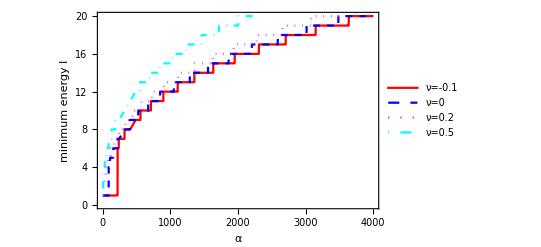

```mathematica
Plot[{lmin[α,-0.1,1],lmin[α,0.0,1],lmin[α,0.2,1],lmin[α,0.5,1]},{α,0,4000},Frame->True,PlotStyle->{{Red},{Blue, Dashed},{Magenta, Dotted},{Cyan, DotDashed}},PlotRange->{{0,4000},{0,20}},FrameLabel-> {Style[α,15],Style["minimum energy l",15]}, PlotLegends->Placed[{"ν=-0.1","ν=0","ν=0.2","ν=0.5"},{0.8,0.4}]]
```

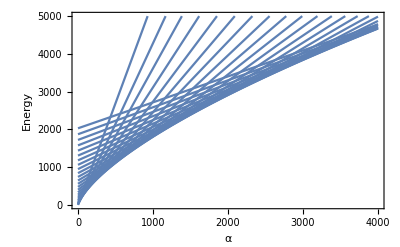

```mathematica
Plot[mytable1[α,0.2,1],{α,0,4000},PlotRange->{{0,4000},{0,5000}},Frame->True,FrameLabel-> {Style[α,15],Style["Energy",15]}]
```

```mathematica
(*κ=μR^3/α*)
```

```mathematica
(*critical fractional excess area*) 
Delta[α_,ν_,R_]:=Energy[α,ν,R]/(π *α* (1+ν))*(1-2ν)
```

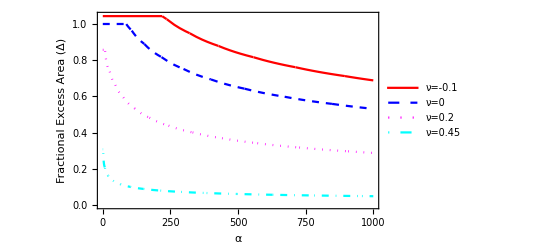

```mathematica
pdelta=Plot[{Delta[α,-0.1,1],Delta[α,0.0,1],Delta[α,0.2,1],Delta[α,0.45,1]},{α,0.1,1000},FrameLabel->{Style["α",15],Style["Fractional Excess Area (Δ)",15]},PlotStyle->{{Red},{Blue, Dashed},{Magenta, Dotted},{Cyan, DotDashed}},Frame->True,PlotLegends->{"ν=-0.1","ν=0","ν=0.2","ν=0.45"}]
```

```mathematica
EnergyDensity[l_,m_,R_,g_,ν_,r_]:=1/(4 Pi)*Simplify[Simplify[2*( EpsxyVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxyVector0[l,m,R,g,ν,r]]
+EpsyzVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyzVector0[l,m,R,g,ν,r]]
+EpszxVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszxVector0[l,m,R,g,ν,r]])+(1-ν)/(1-2ν)*(EpsxxVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxVector0[l,m,R,g,ν,r]]
+ EpsyyVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyVector0[l,m,R,g,ν,r]]
+ EpszzVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszzVector0[l,m,R,g,ν,r]])+2*ν/(1-2ν)*(EpsxxVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyVector0[l,m,R,g,ν,r]]+EpsyyVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszzVector0[l,m,R,g,ν,r]]+EpszzVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxVector0[l,m,R,g,ν,r]])]+Simplify[2*( EpsxyVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxyVector2[l,m,R,g,ν,r]]
+EpsyzVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyzVector2[l,m,R,g,ν,r]]
+EpszxVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszxVector2[l,m,R,g,ν,r]])+(1-ν)/(1-2ν)*(EpsxxVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxVector2[l,m,R,g,ν,r]]
+ EpsyyVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyVector2[l,m,R,g,ν,r]]
+ EpszzVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszzVector2[l,m,R,g,ν,r]])+2*ν/(1-2ν)*(EpsxxVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyVector2[l,m,R,g,ν,r]]+EpsyyVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszzVector2[l,m,R,g,ν,r]]+EpszzVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxVector2[l,m,R,g,ν,r]])],Assumptions->{R>0} ][[1]][[1]];
```

-Graphics-

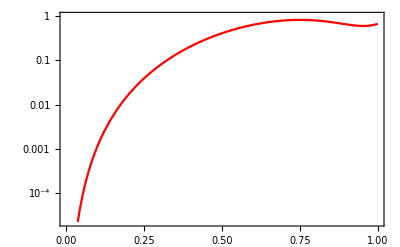

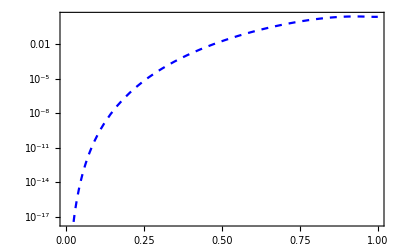

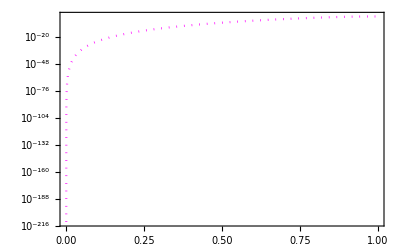

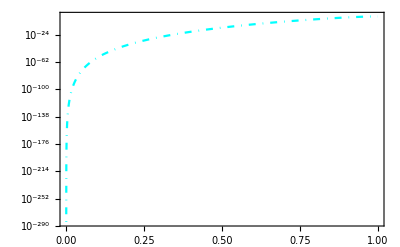

```mathematica
p=Plot[-10,{x,0.5,1},FrameLabel->{Style["r",15],Style["Energy Density",15]},Frame->True,PlotRange-> {{0.5,1},{1*^-1,50}},ScalingFunctions-> "Log"]
p4log=Plot[{EnergyDensity[4,4,1,1,0.2,r]},{r,0,1},PlotStyle->{Red},Frame->True,ScalingFunctions-> "Log"]
p8log=Plot[{EnergyDensity[8,8,1,1,0.2,r]},{r,0,1},PlotStyle->{{Blue,Dashed}},Frame->True,ScalingFunctions-> "Log"]
p16log=Plot[{EnergyDensity[16,16,1,1,0.2,r]},{r,0,1},PlotStyle->{{Magenta,Dotted}},Frame->True,PlotRange->Full,ScalingFunctions-> "Log"]
p32log=Plot[{EnergyDensity[32,32,1,1,0.2,r]},{r,0,1},PlotStyle->{{Cyan,DotDashed}},Frame->True,PlotRange->Full,ScalingFunctions-> "Log"]
```

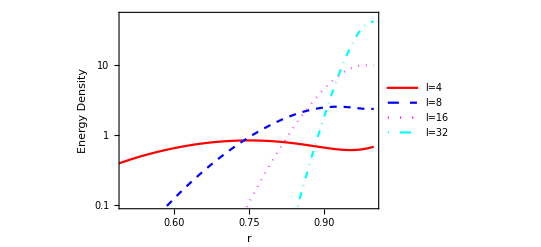

```mathematica
Legended[Show[p,p4log,p8log,p16log,p32log],Placed[LineLegend[{Red,{Blue,Dashed},{Magenta,Dotted},{Cyan,DotDashed}},{"l=4","l=8","l=16","l=32"}],{0.18,0.66}]]
```

```mathematica
(*Now we solve for the irregular solution for displacement (v)*)
```

```mathematica
(* derivatives of r^(-l-1) Y_l^m *)
DXI[l_,m_,r_,θ_,ϕ_]=1/2*(Sqrt[(l+m+2)(l+m+1)]*r^(-l-2)*SphericalHarmonicY[l+1,m+1,θ,ϕ]-Sqrt[(l-m+2)(l-m+1)]*r^(-l-2)*SphericalHarmonicY[l+1,m-1,θ,ϕ])*Sqrt[(2l+1)/(2l+3)]
DYI[l_,m_,r_,θ_,ϕ_]=-I/2*(Sqrt[(l+m+2)(l+m+1)]*r^(-l-2)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+Sqrt[(l-m+2)(l-m+1)]*r^(-l-2)*SphericalHarmonicY[l+1,m-1,θ,ϕ])*Sqrt[(2l+1)/(2l+3)]
DZI[l_,m_,r_,θ_,ϕ_]=-r^(-l-2)*SphericalHarmonicY[l+1,m,θ,ϕ]*Sqrt[(2l+1)/(2l+3)]*Sqrt[(l+1-m)(l+1+m)]
```

1/2 √((1+2 l)/(3+2 l)) (-√((1+l-m) (2+l-m)) r^(-2-l) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+√((1+l+m) (2+l+m)) r^(-2-l) SphericalHarmonicY[1+l,1+m,θ,ϕ])

-1/2 ⅈ √((1+2 l)/(3+2 l)) (√((1+l-m) (2+l-m)) r^(-2-l) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+√((1+l+m) (2+l+m)) r^(-2-l) SphericalHarmonicY[1+l,1+m,θ,ϕ])

-√((1+2 l)/(3+2 l)) √((1+l-m) (1+l+m)) r^(-2-l) SphericalHarmonicY[1+l,m,θ,ϕ]

```mathematica
(* Some checks that analytic derivatives are correct *)
a11=Simplify[DXI[10,5,r,θ,ϕ]];
a22=Simplify[DX[r^(-10-1)*SphericalHarmonicY[10,5,θ,ϕ]]];
b11=Simplify[DYI[10,5,r,θ,ϕ]];
b22=Simplify[DY[r^(-10-1)*SphericalHarmonicY[10,5,θ,ϕ]]];
c11=Simplify[DZI[10,3,r,θ,ϕ]];
c22=Simplify[DZ[r^(-10-1)*SphericalHarmonicY[10,3,θ,ϕ]]];
```

```mathematica
Simplify[a11/a22]
Simplify[b11/b22]
FullSimplify[c11/c22]
```

1

1

1

```mathematica
(* First trial for solution -- v_1 *)
```

```mathematica
vv1x=Simplify[r^2*( aa0*DXI[l,m,r,θ,ϕ]+aa1*DXI[l,m+1,r,θ,ϕ]+aam1*DXI[l,m-1,r,θ,ϕ])]
vv1y=Simplify[r^2*( aa0*DYI[l,m,r,θ,ϕ]+aa1*DYI[l,m+1,r,θ,ϕ]+aam1*DYI[l,m-1,r,θ,ϕ])]
vv1z=Simplify[r^2*( aa0*DZI[l,m,r,θ,ϕ]+aa1*DZI[l,m+1,r,θ,ϕ]+aam1*DZI[l,m-1,r,θ,ϕ])]
```

1/2 √((1+2 l)/(3+2 l)) r^-l (-aam1 √(6+l^2+l (5-2 m)-5 m+m^2) SphericalHarmonicY[1+l,-2+m,θ,ϕ]-aa0 √(2+l^2+l (3-2 m)-3 m+m^2) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+aam1 √((l+m) (1+l+m)) SphericalHarmonicY[1+l,m,θ,ϕ]-aa1 √(l+l^2-2 l m+(-1+m) m) SphericalHarmonicY[1+l,m,θ,ϕ]+aa0 √((1+l+m) (2+l+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ]+aa1 √((2+l+m) (3+l+m)) SphericalHarmonicY[1+l,2+m,θ,ϕ])

-1/2 ⅈ √((1+2 l)/(3+2 l)) r^-l (aam1 √(6+l^2+l (5-2 m)-5 m+m^2) SphericalHarmonicY[1+l,-2+m,θ,ϕ]+aa0 √(2+l^2+l (3-2 m)-3 m+m^2) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+aam1 √((l+m) (1+l+m)) SphericalHarmonicY[1+l,m,θ,ϕ]+aa1 √(l+l^2-2 l m+(-1+m) m) SphericalHarmonicY[1+l,m,θ,ϕ]+aa0 √((1+l+m) (2+l+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ]+aa1 √((2+l+m) (3+l+m)) SphericalHarmonicY[1+l,2+m,θ,ϕ])

-√((1+2 l)/(3+2 l)) r^-l (aam1 √((2+l-m) (l+m)) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+aa0 √(1+2 l+l^2-m^2) SphericalHarmonicY[1+l,m,θ,ϕ]+aa1 √((l-m) (2+l+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ])

```mathematica
vv1xx[l_,m_,r_,θ_,ϕ_]=vv1x;
vv1yy[l_,m_,r_,θ_,ϕ_]=vv1y;
vv1zz[l_,m_,r_,θ_,ϕ_]=vv1z;
```

```mathematica
(* Second trial solution -- v_2  *)
```

```mathematica
vv2x=bx*r^(-l)*SphericalHarmonicY[l-1,m,θ,ϕ];
vv2y=by*r^(-l)*SphericalHarmonicY[l-1,m,θ,ϕ];
vv2z=bz*r^(-l)*SphericalHarmonicY[l-1,m,θ,ϕ];
divvv2=bx* DXI[l-1,m,r,θ,ϕ]+by* DYI[l-1,m,r,θ,ϕ]+bz*DZI[l-1,m,r,θ,ϕ];
divvv22=DX[vv2x]+DY[vv2y]+DZ[vv2z];
div2calc[l_,m_,r_,θ_,ϕ_]=divvv2
div2brut[l_,m_,r_,θ_,ϕ_]=divvv22
```

-bz √((1+2 (-1+l))/(3+2 (-1+l))) √((l-m) (l+m)) r^(-1-l) SphericalHarmonicY[l,m,θ,ϕ]+1/2 bx √((1+2 (-1+l))/(3+2 (-1+l))) (-√((l-m) (1+l-m)) r^(-1-l) SphericalHarmonicY[l,-1+m,θ,ϕ]+√((l+m) (1+l+m)) r^(-1-l) SphericalHarmonicY[l,1+m,θ,ϕ])-1/2 ⅈ by √((1+2 (-1+l))/(3+2 (-1+l))) (√((l-m) (1+l-m)) r^(-1-l) SphericalHarmonicY[l,-1+m,θ,ϕ]+√((l+m) (1+l+m)) r^(-1-l) SphericalHarmonicY[l,1+m,θ,ϕ])

-bz l r^(-1-l) Cos[θ] SphericalHarmonicY[-1+l,m,θ,ϕ]+ⅈ by m r^(-1-l) Cos[ϕ] Csc[θ] SphericalHarmonicY[-1+l,m,θ,ϕ]-bx l r^(-1-l) Cos[ϕ] Sin[θ] SphericalHarmonicY[-1+l,m,θ,ϕ]-ⅈ bx m r^(-1-l) Csc[θ] Sin[ϕ] SphericalHarmonicY[-1+l,m,θ,ϕ]-by l r^(-1-l) Sin[θ] Sin[ϕ] SphericalHarmonicY[-1+l,m,θ,ϕ]+bx r^(-1-l) Cos[θ] Cos[ϕ] (m Cot[θ] SphericalHarmonicY[-1+l,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[l-m] √Gamma[1+l+m] SphericalHarmonicY[-1+l,1+m,θ,ϕ])/(√Gamma[-1+l-m] √Gamma[l+m]))-bz r^(-1-l) Sin[θ] (m Cot[θ] SphericalHarmonicY[-1+l,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[l-m] √Gamma[1+l+m] SphericalHarmonicY[-1+l,1+m,θ,ϕ])/(√Gamma[-1+l-m] √Gamma[l+m]))+by r^(-1-l) Cos[θ] Sin[ϕ] (m Cot[θ] SphericalHarmonicY[-1+l,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[l-m] √Gamma[1+l+m] SphericalHarmonicY[-1+l,1+m,θ,ϕ])/(√Gamma[-1+l-m] √Gamma[l+m]))

```mathematica
(* Another check on the divergence of v_2 *)
```

```mathematica
Simplify[div2calc[6,2,r,θ,ϕ]-div2brut[6,2,r,θ,ϕ]]
```

0

```mathematica
(* Calculate the three components of grad (div v_2 ) *)
```

```mathematica
Ddivvv2DX[l_,m_,r_,θ_,ϕ_]=Simplify[-bz √((1+2 (-1+l))/(3+2 (-1+l))) √((l-m) (l+m)) DXI[l,m,r,θ,ϕ]+1/2 bx √((1+2 (-1+l))/(3+2 (-1+l))) (-√((l-m) (1+l-m)) DXI[l,-1+m,r,θ,ϕ]+√((l+m) (1+l+m)) DXI[l,1+m,r,θ,ϕ])-1/2 ⅈ by √((1+2 (-1+l))/(3+2 (-1+l))) (√((l-m) (1+l-m)) DXI[l,-1+m,r,θ,ϕ]+√((l+m) (1+l+m)) DXI[l,1+m,r,θ,ϕ])];
```

```mathematica
Ddivvv2DY[l_,m_,r_,θ_,ϕ_]=Simplify[-bz √((1+2 (-1+l))/(3+2 (-1+l))) √((l-m) (l+m)) DYI[l,m,r,θ,ϕ]+1/2 bx √((1+2 (-1+l))/(3+2 (-1+l))) (-√((l-m) (1+l-m)) DYI[l,-1+m,r,θ,ϕ]+√((l+m) (1+l+m)) DYI[l,1+m,r,θ,ϕ])-1/2 ⅈ by √((1+2 (-1+l))/(3+2 (-1+l))) (√((l-m) (1+l-m)) DYI[l,-1+m,r,θ,ϕ]+√((l+m) (1+l+m)) DYI[l,1+m,r,θ,ϕ])]
```

1/4 ⅈ √((-1+2 l)/(3+2 l)) r^(-2-l) ((bx+ⅈ by) √(l+l^2-2 l m+(-1+m) m) √(6+l^2+l (5-2 m)-5 m+m^2) SphericalHarmonicY[1+l,-2+m,θ,ϕ]+2 bz √(l^2-m^2) √(2+l^2+l (3-2 m)-3 m+m^2) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+2 ⅈ by √(l+l^2-2 l m+(-1+m) m) √(l+l^2+m+2 l m+m^2) SphericalHarmonicY[1+l,m,θ,ϕ]+2 bz √(l^2-m^2) √(2+l^2+3 m+m^2+l (3+2 m)) SphericalHarmonicY[1+l,1+m,θ,ϕ]-bx √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ]+ⅈ by √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ])

```mathematica
Ddivvv2DZ[l_,m_,r_,θ_,ϕ_]=Simplify[-bz √((1+2 (-1+l))/(3+2 (-1+l))) √((l-m) (l+m)) DZI[l,m,r,θ,ϕ]+1/2 bx √((1+2 (-1+l))/(3+2 (-1+l))) (-√((l-m) (1+l-m)) DZI[l,-1+m,r,θ,ϕ]+√((l+m) (1+l+m)) DZI[l,1+m,r,θ,ϕ])-1/2 ⅈ by √((1+2 (-1+l))/(3+2 (-1+l))) (√((l-m) (1+l-m)) DZI[l,-1+m,r,θ,ϕ]+√((l+m) (1+l+m)) DZI[l,1+m,r,θ,ϕ])]
```

1/2 √((-1+2 l)/(3+2 l)) r^(-2-l) ((bx+ⅈ by) √(2 l+l^2-(-2+m) m) √(l+l^2-2 l m+(-1+m) m) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+2 bz √(l^2-m^2) √(1+2 l+l^2-m^2) SphericalHarmonicY[1+l,m,θ,ϕ]-(bx-ⅈ by) √(l+l^2+m+2 l m+m^2) √(2 l+l^2-m (2+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ])

```mathematica
Simplify[Ddivvv2DX[6,2,r,θ,ϕ]-DX[div2brut[6,2,r,θ,ϕ]]]
Simplify[Ddivvv2DY[6,2,r,θ,ϕ]-DY[div2brut[6,2,r,θ,ϕ]]]
Simplify[Ddivvv2DZ[6,2,r,θ,ϕ]-DZ[div2brut[6,2,r,θ,ϕ]]]
```

0

0

0

```mathematica
(* Analytic calculation of required double derivative operator on v_1 *)
```

```mathematica
DDVV1x=Simplify[(-2(l+1)-2(1-2ν)(2l+1))(aa1*DXI[l,m+1,r,θ,ϕ]+aa0*DXI[l,m,r,θ,ϕ]+aam1*DXI[l,m-1,r,θ,ϕ])];
DDVV1y=Simplify[(-2(l+1)-2(1-2ν)(2l+1))(aa1*DYI[l,m+1,r,θ,ϕ]+aa0*DYI[l,m,r,θ,ϕ]+aam1*DYI[l,m-1,r,θ,ϕ])];
DDVV1z=Simplify[(-2(l+1)-2(1-2ν)(2l+1))(aa1*DZI[l,m+1,r,θ,ϕ]+aa0*DZI[l,m,r,θ,ϕ]+aam1*DZI[l,m-1,r,θ,ϕ])];
DDvv1x[l_,m_,r_,θ_,ϕ_]=DDVV1x
DDvv1y[l_,m_,r_,θ_,ϕ_]=DDVV1y
DDvv1z[l_,m_,r_,θ_,ϕ_]=DDVV1z
```

-√((1+2 l)/(3+2 l)) r^(-2-l) (-2-3 l+2 ν+4 l ν) (aam1 √(6+l^2+l (5-2 m)-5 m+m^2) SphericalHarmonicY[1+l,-2+m,θ,ϕ]+aa0 √(2+l^2+l (3-2 m)-3 m+m^2) SphericalHarmonicY[1+l,-1+m,θ,ϕ]-aam1 √((l+m) (1+l+m)) SphericalHarmonicY[1+l,m,θ,ϕ]+aa1 √(l+l^2-2 l m+(-1+m) m) SphericalHarmonicY[1+l,m,θ,ϕ]-aa0 √((1+l+m) (2+l+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ]-aa1 √((2+l+m) (3+l+m)) SphericalHarmonicY[1+l,2+m,θ,ϕ])

-ⅈ √((1+2 l)/(3+2 l)) r^(-2-l) (-2-3 l+2 ν+4 l ν) (aam1 √(6+l^2+l (5-2 m)-5 m+m^2) SphericalHarmonicY[1+l,-2+m,θ,ϕ]+aa0 √(2+l^2+l (3-2 m)-3 m+m^2) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+aam1 √((l+m) (1+l+m)) SphericalHarmonicY[1+l,m,θ,ϕ]+aa1 √(l+l^2-2 l m+(-1+m) m) SphericalHarmonicY[1+l,m,θ,ϕ]+aa0 √((1+l+m) (2+l+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ]+aa1 √((2+l+m) (3+l+m)) SphericalHarmonicY[1+l,2+m,θ,ϕ])

-2 √((1+2 l)/(3+2 l)) r^(-2-l) (-2-3 l+2 ν+4 l ν) (aam1 √((2+l-m) (l+m)) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+aa0 √(1+2 l+l^2-m^2) SphericalHarmonicY[1+l,m,θ,ϕ]+aa1 √((l-m) (2+l+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ])

```mathematica
(* brute force *)
mbzbrutx[l_,m_,r_,θ_,ϕ_]=(DX[DX[vv1xx[l,m,r,θ,ϕ]]+DY[vv1yy[l,m,r,θ,ϕ]]+DZ[vv1zz[l,m,r,θ,ϕ]]]
+(1-2ν)Laplacian[vv1xx[l,m,r,θ,ϕ],{r,θ,ϕ},"Spherical"]/.sols );

mbzbruty[l_,m_,r_,θ_,ϕ_]=(DY[DX[vv1xx[l,m,r,θ,ϕ]]+DY[vv1yy[l,m,r,θ,ϕ]]+DZ[vv1zz[l,m,r,θ,ϕ]]]
+(1-2ν)Laplacian[vv1yy[l,m,r,θ,ϕ],{r,θ,ϕ},"Spherical"]/.sols );

mbzbrutz[l_,m_,r_,θ_,ϕ_]=(DZ[DX[vv1xx[l,m,r,θ,ϕ]]+DY[vv1yy[l,m,r,θ,ϕ]]+DZ[vv1zz[l,m,r,θ,ϕ]]]
+(1-2ν)Laplacian[vv1zz[l,m,r,θ,ϕ],{r,θ,ϕ},"Spherical"]/.sols );
```

```mathematica
(* Find the requied values of aa1, aa0, and aam1 *)MustBeZero=Simplify[DDvv1x[l,m,r,θ,ϕ]+Ddivvv2DX[l,m,r,θ,ϕ]];
MustBeZeroy=Simplify[DDvv1y[l,m,r,θ,ϕ]+Ddivvv2DY[l,m,r,θ,ϕ]];
MustBeZeroz=Simplify[DDvv1z[l,m,r,θ,ϕ]+Ddivvv2DZ[l,m,r,θ,ϕ]];
sols=Simplify[Solve[Coefficient[MustBeZero,SphericalHarmonicY[1+l,-2+m,θ,ϕ],1]==0&&
Coefficient[MustBeZero,SphericalHarmonicY[1+l,-1+m,θ,ϕ],1]==0 &&
Coefficient[MustBeZero,SphericalHarmonicY[1+l,m,θ,ϕ],1]==0&&
Coefficient[MustBeZero,SphericalHarmonicY[1+l,1+m,θ,ϕ],1]==0&&
Coefficient[MustBeZero,SphericalHarmonicY[1+l,2+m,θ,ϕ],1]==0,{aa0,aa1,aam1}]]
Simplify[MustBeZero/.sols][[1]] (* Check the solution works *)
Simplify[MustBeZeroy/.sols][[1]]
Simplify[MustBeZeroz/.sols][[1]]
```

{{aa0→(bz √((-1+2 l)/(3+2 l)) √(l^2-m^2))/(2 √((1+2 l)/(3+2 l)) (-2-3 l+2 ν+4 l ν)),aa1→-((bx-ⅈ by) √((-1+2 l)/(3+2 l)) √((l+m) (1+l+m)))/(4 √((1+2 l)/(3+2 l)) (-2-3 l+2 ν+4 l ν)),aam1→((bx+ⅈ by) √((-1+2 l)/(3+2 l)) √(l+l^2-2 l m+(-1+m) m))/(4 √((1+2 l)/(3+2 l)) (-2-3 l+2 ν+4 l ν))}}

0

0

0

```mathematica
(* More checks *)
```

```mathematica
mbzBbrutx[l_,m_,r_,θ_,ϕ_]=mbzbrutx[l,m,r,θ,ϕ]/.sols;
mbzBbruty[l_,m_,r_,θ_,ϕ_]=mbzbruty[l,m,r,θ,ϕ]/.sols;
mbzBbrutz[l_,m_,r_,θ_,ϕ_]=mbzbrutz[l,m,r,θ,ϕ]/.sols;
```

```mathematica
Simplify[mbzBbrutx[6,2,r,θ,ϕ]+DX[div2brut[6,2,r,θ,ϕ]]]
Simplify[mbzBbruty[6,2,r,θ,ϕ]+DY[div2brut[6,2,r,θ,ϕ]]]
Simplify[mbzBbrutz[6,2,r,θ,ϕ]+DZ[div2brut[6,2,r,θ,ϕ]]]
```

{{0}}

{{0}}

{{0}}

```mathematica
Simplify[mbzbrutx[6,2,r,θ,ϕ]-DDvv1x[6,2,r,θ,ϕ]/. sols] 
Simplify[mbzbruty[6,2,r,θ,ϕ]-DDvv1y[6,2,r,θ,ϕ]/. sols] 
Simplify[mbzbrutz[6,2,r,θ,ϕ]-DDvv1z[6,2,r,θ,ϕ]/. sols] 
(* brute force dervative operator minus calculated derivative operator -- should be zero *)
```

{{0}}

{{0}}

{{0}}

```mathematica
v1x[l_,m_,r_,θ_,ϕ_]=Simplify[vv1x/. sols][[1]];
v1y[l_,m_,r_,θ_,ϕ_]=Simplify[vv1y/. sols][[1]];
v1z[l_,m_,r_,θ_,ϕ_]=Simplify[vv1z/. sols][[1]];
v22x[l_,m_,r_,θ_,ϕ_]=vv2x;
v22y[l_,m_,r_,θ_,ϕ_]=vv2y;
v22z[l_,m_,r_,θ_,ϕ_]=vv2z;
v12x[l_,m_,r_,θ_,ϕ_]=v22x[l,m,r,θ,ϕ]+v1x[l,m,r,θ,ϕ] (* Full solutionn *)
v12y[l_,m_,r_,θ_,ϕ_]=v22y[l,m,r,θ,ϕ]+v1y[l,m,r,θ,ϕ]
v12z[l_,m_,r_,θ_,ϕ_]=v22z[l,m,r,θ,ϕ]+v1z[l,m,r,θ,ϕ]
```

bx r^-l SphericalHarmonicY[-1+l,m,θ,ϕ]-1/(8 (-2-3 l+2 ν+4 l ν))√((-1+2 l)/(3+2 l)) r^-l ((bx+ⅈ by) √(l+l^2-2 l m+(-1+m) m) √(6+l^2+l (5-2 m)-5 m+m^2) SphericalHarmonicY[1+l,-2+m,θ,ϕ]+2 bz √(l^2-m^2) √(2+l^2+l (3-2 m)-3 m+m^2) SphericalHarmonicY[1+l,-1+m,θ,ϕ]-2 bx √(l+l^2-2 l m+(-1+m) m) √(l+l^2+m+2 l m+m^2) SphericalHarmonicY[1+l,m,θ,ϕ]-2 bz √(l^2-m^2) √(2+l^2+3 m+m^2+l (3+2 m)) SphericalHarmonicY[1+l,1+m,θ,ϕ]+bx √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ]-ⅈ by √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ])

by r^-l SphericalHarmonicY[-1+l,m,θ,ϕ]+1/(8 (-2-3 l+2 ν+4 l ν))√((-1+2 l)/(3+2 l)) r^-l ((-ⅈ bx+by) √(l+l^2-2 l m+(-1+m) m) √(6+l^2+l (5-2 m)-5 m+m^2) SphericalHarmonicY[1+l,-2+m,θ,ϕ]-2 ⅈ bz √(l^2-m^2) √(2+l^2+l (3-2 m)-3 m+m^2) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+2 by √(l+l^2-2 l m+(-1+m) m) √(l+l^2+m+2 l m+m^2) SphericalHarmonicY[1+l,m,θ,ϕ]-2 ⅈ bz √(l^2-m^2) √(2+l^2+3 m+m^2+l (3+2 m)) SphericalHarmonicY[1+l,1+m,θ,ϕ]+ⅈ bx √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ]+by √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ])

bz r^-l SphericalHarmonicY[-1+l,m,θ,ϕ]+1/(4 (-2-3 l+2 ν+4 l ν))√((-1+2 l)/(3+2 l)) r^-l (-(bx+ⅈ by) √(2 l+l^2-(-2+m) m) √(l+l^2-2 l m+(-1+m) m) SphericalHarmonicY[1+l,-1+m,θ,ϕ]-2 bz √(l^2-m^2) √(1+2 l+l^2-m^2) SphericalHarmonicY[1+l,m,θ,ϕ]+(bx-ⅈ by) √(l+l^2+m+2 l m+m^2) √(2 l+l^2-m (2+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ])

```mathematica
(* Now calculate D(D.u)+(1-2ν)D^2u, for (lll, mmm) which should be zero for all lll and mmm *)
mmm=4;
lll=8;
divlll=DX[v12x[lll,mmm,r,θ,ϕ]]+DY[v12y[lll,mmm,r,θ,ϕ]]+DZ[v12z[lll,mmm,r,θ,ϕ]];
graddiv4=Simplify[{DX[divlll],DY[divlll],DZ[divlll]}];
lap4=Simplify[Simplify[{Laplacian[v12x[lll,mmm,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[v12y[lll,mmm,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[v12z[lll,mmm,r,θ,ϕ],{r,θ,ϕ},"Spherical"]}]];
Simplify[graddiv4+(1-2ν)*lap4] (* should be {0,0,0} and it is *)
```

{0,0,0}

```mathematica
v3x[l_,m_,r_,θ_,ϕ_]=-aa1*R^2*DXI[l,m+1,r,θ,ϕ]-aa0*R^2*DXI[l,m,r,θ,ϕ]-aam1*R^2*DXI[l,m-1,r,θ,ϕ];
v3y[l_,m_,r_,θ_,ϕ_]=-aa1*R^2*DYI[l,m+1,r,θ,ϕ]-aa0*R^2*DYI[l,m,r,θ,ϕ]-aam1*R^2*DYI[l,m-1,r,θ,ϕ];
v3z[l_,m_,r_,θ_,ϕ_]=-aa1*R^2*DZI[l,m+1,r,θ,ϕ]-aa0*R^2*DZI[l,m,r,θ,ϕ]-aam1*R^2*DZI[l,m-1,r,θ,ϕ];
```

```mathematica
Simplify[v12x[l,m,R,θ,ϕ]+v3x[l,m,R,θ,ϕ]/.sols]
```

{bx R^-l SphericalHarmonicY[-1+l,m,θ,ϕ]}

```mathematica
newvx[l_,m_,r_,θ_,ϕ_,bx_,by_,bz_]=Simplify[v12x[l,m,r,θ,ϕ]+v3x[l,m,r,θ,ϕ]/.sols]
```

{bx r^-l SphericalHarmonicY[-1+l,m,θ,ϕ]-1/(8 (-2-3 l+2 ν+4 l ν))√((-1+2 l)/(3+2 l)) r^(-2-l) (r^2-R^2) ((bx+ⅈ by) √(l+l^2-2 l m+(-1+m) m) √(6+l^2+l (5-2 m)-5 m+m^2) SphericalHarmonicY[1+l,-2+m,θ,ϕ]+2 bz √(l^2-m^2) √(2+l^2+l (3-2 m)-3 m+m^2) SphericalHarmonicY[1+l,-1+m,θ,ϕ]-2 bx √(l+l^2-2 l m+(-1+m) m) √(l+l^2+m+2 l m+m^2) SphericalHarmonicY[1+l,m,θ,ϕ]-2 bz √(l^2-m^2) √(2+l^2+3 m+m^2+l (3+2 m)) SphericalHarmonicY[1+l,1+m,θ,ϕ]+bx √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ]-ⅈ by √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ])}

```mathematica
newvy[l_,m_,r_,θ_,ϕ_,bx_,by_,bz_]=Simplify[v12y[l,m,r,θ,ϕ]+v3y[l,m,r,θ,ϕ]/.sols]
```

{1/8 r^-l (8 by SphericalHarmonicY[-1+l,m,θ,ϕ]+1/(r^2 (-2-3 l+2 ν+4 l ν))√((-1+2 l)/(3+2 l)) (r^2-R^2) ((-ⅈ bx+by) √(l+l^2-2 l m+(-1+m) m) √(6+l^2+l (5-2 m)-5 m+m^2) SphericalHarmonicY[1+l,-2+m,θ,ϕ]-2 ⅈ bz √(l^2-m^2) √(2+l^2+l (3-2 m)-3 m+m^2) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+2 by √(l+l^2-2 l m+(-1+m) m) √(l+l^2+m+2 l m+m^2) SphericalHarmonicY[1+l,m,θ,ϕ]-2 ⅈ bz √(l^2-m^2) √(2+l^2+3 m+m^2+l (3+2 m)) SphericalHarmonicY[1+l,1+m,θ,ϕ]+ⅈ bx √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ]+by √(l+l^2+m+2 l m+m^2) √(6+l^2+5 m+m^2+l (5+2 m)) SphericalHarmonicY[1+l,2+m,θ,ϕ]))}

```mathematica
newvz[l_,m_,r_,θ_,ϕ_,bx_,by_,bz_]=Simplify[v12z[l,m,r,θ,ϕ]+v3z[l,m,r,θ,ϕ]/.sols]
```

{bz r^-l SphericalHarmonicY[-1+l,m,θ,ϕ]-1/(4 (-2-3 l+2 ν+4 l ν))√((-1+2 l)/(3+2 l)) r^(-2-l) (r^2-R^2) ((bx+ⅈ by) √(2 l+l^2-(-2+m) m) √(l+l^2-2 l m+(-1+m) m) SphericalHarmonicY[1+l,-1+m,θ,ϕ]+2 bz √(l^2-m^2) √(1+2 l+l^2-m^2) SphericalHarmonicY[1+l,m,θ,ϕ]-(bx-ⅈ by) √(l+l^2+m+2 l m+m^2) √(2 l+l^2-m (2+m)) SphericalHarmonicY[1+l,1+m,θ,ϕ])}

```mathematica
Simplify[newvx[l,m,R,θ,ϕ,Subscript[S, x]*R^(l),Subscript[S, y]*R^(l),Subscript[S, z]*R^(l)]]
Simplify[newvy[l,m,R,θ,ϕ,Subscript[S, x]*R^(l),Subscript[S, y]*R^(l),Subscript[S, z]*R^(l)]]
Simplify[newvz[l,m,R,θ,ϕ,Subscript[S, x]*R^(l),Subscript[S, y]*R^(l),Subscript[S, z]*R^(l)]]
```

{SphericalHarmonicY[-1+l,m,θ,ϕ] S_x}

{SphericalHarmonicY[-1+l,m,θ,ϕ] S_y}

{SphericalHarmonicY[-1+l,m,θ,ϕ] S_z}

```mathematica
SXnnn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[-1+l,-1-m,θ,ϕ],1]
SXnnp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[-1+l,-m+1,θ,ϕ],1];
SXnpn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[-1+l,m-1,θ,ϕ],1];
SXpnn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[1+l,-m-1,θ,ϕ],1];
SXppn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[1+l,m-1,θ,ϕ],1];
SXnpp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[-1+l,m+1,θ,ϕ],1];
SXpnp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[1+l,-m+1,θ,ϕ],1];
SXppp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[1]],SphericalHarmonicY[1+l,m+1,θ,ϕ],1];

SYnnn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[-1+l,-1-m,θ,ϕ],1];
SYnnp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[-1+l,-m+1,θ,ϕ],1];
SYnpn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[-1+l,m-1,θ,ϕ],1];
SYpnn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[1+l,-m-1,θ,ϕ],1];
SYppn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[1+l,m-1,θ,ϕ],1];
SYnpp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[-1+l,m+1,θ,ϕ],1];
SYpnp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[1+l,-m+1,θ,ϕ],1];
SYppp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[2]],SphericalHarmonicY[1+l,m+1,θ,ϕ],1];

SZnn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[3]],SphericalHarmonicY[-1+l,-m,θ,ϕ],1];
SZnp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[3]],SphericalHarmonicY[-1+l,m,θ,ϕ],1];
SZpn=R*g*Coefficient[Shape1[l,m,θ,ϕ][[3]],SphericalHarmonicY[1+l,-m,θ,ϕ],1];
SZpp=R*g*Coefficient[Shape1[l,m,θ,ϕ][[3]],SphericalHarmonicY[1+l,m,θ,ϕ],1];
```

1/2 (-1)^(1-l) g √l R (Piecewise[{{(-1)^(-l+m) √((-l+l^2+m-2 l m+m^2)/(-2 l+8 l^3)), l≥2+m}, {0, True}}])

```mathematica
vxnnn=newvx[l,-m-1,R,θ,ϕ,SXnnn*R^(l),SYnnn*R^(l),0];
vxnnp=newvx[l,-m+1,R,θ,ϕ,SXnnp*R^(l),SYnnp*R^(l),0];
vxnpn=newvx[l,m-1,R,θ,ϕ,SXnpn*R^(l),SYnpn*R^(l),0];
vxnpp=newvx[l,m+1,R,θ,ϕ,SXnpp*R^(l),SYnpp*R^(l),0];

vxpnn=newvx[l+2,-m-1,R,θ,ϕ,SXpnn*R^(l+2),SYpnn*R^(l+2),0];
vxpnp=newvx[l+2,-m+1,R,θ,ϕ,SXpnp*R^(l+2),SYpnp*R^(l+2),0];
vxppn=newvx[l+2,m-1,R,θ,ϕ,SXppn*R^(l+2),SYppn*R^(l+2),0];
vxppp=newvx[l+2,m+1,R,θ,ϕ,SXppp*R^(l+2),SYppp*R^(l+2),0];

vxnn=newvx[l,-m,R,θ,ϕ,0,0,SZnn*R^(l)];
vxnp=newvx[l,m,R,θ,ϕ,0,0,SZnp*R^(l)];
vxpn=newvx[l+2,-m,R,θ,ϕ,0,0,SZpn*R^(l+2)];
vxpp=newvx[l+2,m,R,θ,ϕ,0,0,SZpp*R^(l+2)];
```

```mathematica
vynnn=newvy[l,-m-1,R,θ,ϕ,SXnnn*R^(l),SYnnn*R^(l),0];
vynnp=newvy[l,-m+1,R,θ,ϕ,SXnnp*R^(l),SYnnp*R^(l),0];
vynpn=newvy[l,m-1,R,θ,ϕ,SXnpn*R^(l),SYnpn*R^(l),0];
vynpp=newvy[l,m+1,R,θ,ϕ,SXnpp*R^(l),SYnpp*R^(l),0];

vypnn=newvy[l+2,-m-1,R,θ,ϕ,SXpnn*R^(l+2),SYpnn*R^(l+2),0];
vypnp=newvy[l+2,-m+1,R,θ,ϕ,SXpnp*R^(l+2),SYpnp*R^(l+2),0];
vyppn=newvy[l+2,m-1,R,θ,ϕ,SXppn*R^(l+2),SYppn*R^(l+2),0];
vyppp=newvy[l+2,m+1,R,θ,ϕ,SXppp*R^(l+2),SYppp*R^(l+2),0];

vynn=newvy[l,-m,R,θ,ϕ,0,0,SZnn*R^(l)];
vynp=newvy[l,m,R,θ,ϕ,0,0,SZnp*R^(l)];
vypn=newvy[l+2,-m,R,θ,ϕ,0,0,SZpn*R^(l+2)];
vypp=newvy[l+2,m,R,θ,ϕ,0,0,SZpp*R^(l+2)];
```

```mathematica
vznnn=newvz[l,-m-1,R,θ,ϕ,SXnnn*R^(l),SYnnn*R^(l),0];
vznnp=newvz[l,-m+1,R,θ,ϕ,SXnnp*R^(l),SYnnp*R^(l),0];
vznpn=newvz[l,m-1,R,θ,ϕ,SXnpn*R^(l),SYnpn*R^(l),0];
vznpp=newvz[l,m+1,R,θ,ϕ,SXnpp*R^(l),SYnpp*R^(l),0];

vzpnn=newvz[l+2,-m-1,R,θ,ϕ,SXpnn*R^(l+2),SYpnn*R^(l+2),0];
vzpnp=newvz[l+2,-m+1,R,θ,ϕ,SXpnp*R^(l+2),SYpnp*R^(l+2),0];
vzppn=newvz[l+2,m-1,R,θ,ϕ,SXppn*R^(l+2),SYppn*R^(l+2),0];
vzppp=newvz[l+2,m+1,R,θ,ϕ,SXppp*R^(l+2),SYppp*R^(l+2),0];

vznn=newvz[l,-m,R,θ,ϕ,0,0,SZnn*R^(l)];
vznp=newvz[l,m,R,θ,ϕ,0,0,SZnp*R^(l)];
vzpn=newvz[l+2,-m,R,θ,ϕ,0,0,SZpn*R^(l+2)];
vzpp=newvz[l+2,m,R,θ,ϕ,0,0,SZpp*R^(l+2)];
```

```mathematica
(* Now compare the surface displacement from u with the displacement from the original shape *)
```

```mathematica
(* displacement from v *)
shape1check[l_,m_,θ_,ϕ_]=vxnnn+vxnnp+vxnpn+vxnpp+vxpnn+vxpnp+vxppn+vxppp
shape2check[l_,m_,θ_,ϕ_]=vynnn+vynnp+vynpn+vynpp+vypnn+vypnp+vyppn+vyppp
shape3check[l_,m_,θ_,ϕ_]=vznn+vznp+vzpn+vzpp
```

{1/2 (-1)^(1-l) g √l R (Piecewise[{{(-1)^(-l+m) √((-l+l^2+m-2 l m+m^2)/(-2 l+8 l^3)), l≥2+m}, {0, True}}]) SphericalHarmonicY[-1+l,-1-m,θ,ϕ]+1/2 (-1)^-l g √l R (Piecewise[{{(-1)^(-l+m) √(((-1+l+m) (l+m))/(-2 l+8 l^3)), l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,1-m,θ,ϕ]+1/2 (-1)^(1-l+m) g √l R (Piecewise[{{(-1)^(-l-m) √(((-1+l+m) (l+m))/(-2 l+8 l^3)), l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,-1+m,θ,ϕ]+1/2 (-1)^(-l+m) g √l R (Piecewise[{{(-1)^(-l-m) √((-l+l^2+m-2 l m+m^2)/(-2 l+8 l^3)), l≥2+m}, {0, True}}]) SphericalHarmonicY[-1+l,1+m,θ,ϕ]+((-1)^(2 l-m) g √((1+l+m) (2+l+m)) R SphericalHarmonicY[1+l,-1-m,θ,ϕ])/(2 √(6+16 l+8 l^2))+((-1)^(1+2 l-m) g R SphericalHarmonicY[1+l,1-m,θ,ϕ])/(2 √((6+16 l+8 l^2)/(2+3 l+l^2-3 m-2 l m+m^2)))+((-1)^(2 (l+m)) g R SphericalHarmonicY[1+l,-1+m,θ,ϕ])/(2 √((6+16 l+8 l^2)/(2+3 l+l^2-3 m-2 l m+m^2)))+((-1)^(1+2 l+2 m) g √((1+l+m) (2+l+m)) R SphericalHarmonicY[1+l,1+m,θ,ϕ])/(2 √(6+16 l+8 l^2))}

{-1/2 ⅈ (-1)^-l g √l R (Piecewise[{{(-1)^(-l+m) √((-l+l^2+m-2 l m+m^2)/(-2 l+8 l^3)), l≥2+m}, {0, True}}]) SphericalHarmonicY[-1+l,-1-m,θ,ϕ]-1/2 ⅈ (-1)^-l g √l R (Piecewise[{{(-1)^(-l+m) √(((-1+l+m) (l+m))/(-2 l+8 l^3)), l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,1-m,θ,ϕ]-1/2 ⅈ (-1)^(-l+m) g √l R (Piecewise[{{(-1)^(-l-m) √(((-1+l+m) (l+m))/(-2 l+8 l^3)), l+m≥2}, {0, True}}]) SphericalHarmonicY[-1+l,-1+m,θ,ϕ]-1/2 ⅈ (-1)^(-l+m) g √l R (Piecewise[{{(-1)^(-l-m) √((-l+l^2+m-2 l m+m^2)/(-2 l+8 l^3)), l≥2+m}, {0, True}}]) SphericalHarmonicY[-1+l,1+m,θ,ϕ]-(ⅈ (-1)^(1+2 l-m) g √((1+l+m) (2+l+m)) R SphericalHarmonicY[1+l,-1-m,θ,ϕ])/(2 √(6+16 l+8 l^2))-(ⅈ (-1)^(1+2 l-m) g R SphericalHarmonicY[1+l,1-m,θ,ϕ])/(2 √((6+16 l+8 l^2)/(2+3 l+l^2-3 m-2 l m+m^2)))-(ⅈ (-1)^(1+2 l+2 m) g R SphericalHarmonicY[1+l,-1+m,θ,ϕ])/(2 √((6+16 l+8 l^2)/(2+3 l+l^2-3 m-2 l m+m^2)))-(ⅈ (-1)^(1+2 l+2 m) g √((1+l+m) (2+l+m)) R SphericalHarmonicY[1+l,1+m,θ,ϕ])/(2 √(6+16 l+8 l^2))}

{((-1)^-l g √l R (Piecewise[{{(-1)^(-l+m) √(-(l^2-m^2)/(l-4 l^3)), l+m≥1&&l≥1+m}, {0, True}}]) SphericalHarmonicY[-1+l,-m,θ,ϕ])/(√2)+((-1)^(-l+m) g √l R (Piecewise[{{(-1)^(-l-m) √(-(l^2-m^2)/(l-4 l^3)), l≥1+m&&l+m≥1}, {0, True}}]) SphericalHarmonicY[-1+l,m,θ,ϕ])/(√2)+((-1)^(2 l-m) g √((1+2 l+l^2-m^2)/(3+8 l+4 l^2)) R SphericalHarmonicY[1+l,-m,θ,ϕ])/(√2)+((-1)^(2 l+2 m) g √((1+2 l+l^2-m^2)/(3+8 l+4 l^2)) R SphericalHarmonicY[1+l,m,θ,ϕ])/(√2)}

```mathematica
(* Check by dividing one by the other *)
Simplify[Shape1[4,2,θ,ϕ][[1]]/shape1check[4,2,θ,ϕ]]
Simplify[Shape1[4,2,θ,ϕ][[2]]/shape2check[4,2,θ,ϕ]]
Simplify[Shape1[4,2,θ,ϕ][[3]]/shape3check[4,2,θ,ϕ]]
```

{1/(g R)}

{1/(g R)}

{1/(g R)}

```mathematica
(* Now we know the BCs are satisfied, we put back in the r-dependence *)
```

```mathematica
vxnnn=newvx[l,-m-1,r,θ,ϕ,SXnnn*R^(l),SYnnn*R^(l),0];
vxnnp=newvx[l,-m+1,r,θ,ϕ,SXnnp*R^(l),SYnnp*R^(l),0];
vxnpn=newvx[l,m-1,r,θ,ϕ,SXnpn*R^(l),SYnpn*R^(l),0];
vxnpp=newvx[l,m+1,r,θ,ϕ,SXnpp*R^(l),SYnpp*R^(l),0];

vxpnn=newvx[l+2,-m-1,r,θ,ϕ,SXpnn*R^(l+2),SYpnn*R^(l+2),0];
vxpnp=newvx[l+2,-m+1,r,θ,ϕ,SXpnp*R^(l+2),SYpnp*R^(l+2),0];
vxppn=newvx[l+2,m-1,r,θ,ϕ,SXppn*R^(l+2),SYppn*R^(l+2),0];
vxppp=newvx[l+2,m+1,r,θ,ϕ,SXppp*R^(l+2),SYppp*R^(l+2),0];

vxnn=newvx[l,-m,r,θ,ϕ,0,0,SZnn*R^(l)];
vxnp=newvx[l,m,r,θ,ϕ,0,0,SZnp*R^(l)];
vxpn=newvx[l+2,-m,r,θ,ϕ,0,0,SZpn*R^(l+2)];
vxpp=newvx[l+2,m,r,θ,ϕ,0,0,SZpp*R^(l+2)];

vynnn=newvy[l,-m-1,r,θ,ϕ,SXnnn*R^(l),SYnnn*R^(l),0];
vynnp=newvy[l,-m+1,r,θ,ϕ,SXnnp*R^(l),SYnnp*R^(l),0];
vynpn=newvy[l,m-1,r,θ,ϕ,SXnpn*R^(l),SYnpn*R^(l),0];
vynpp=newvy[l,m+1,r,θ,ϕ,SXnpp*R^(l),SYnpp*R^(l),0];

vypnn=newvy[l+2,-m-1,r,θ,ϕ,SXpnn*R^(l+2),SYpnn*R^(l+2),0];
vypnp=newvy[l+2,-m+1,r,θ,ϕ,SXpnp*R^(l+2),SYpnp*R^(l+2),0];
vyppn=newvy[l+2,m-1,r,θ,ϕ,SXppn*R^(l+2),SYppn*R^(l+2),0];
vyppp=newvy[l+2,m+1,r,θ,ϕ,SXppp*R^(l+2),SYppp*R^(l+2),0];

vynn=newvy[l,-m,r,θ,ϕ,0,0,SZnn*R^(l)];
vynp=newvy[l,m,r,θ,ϕ,0,0,SZnp*R^(l)];
vypn=newvy[l+2,-m,r,θ,ϕ,0,0,SZpn*R^(l+2)];
vypp=newvy[l+2,m,r,θ,ϕ,0,0,SZpp*R^(l+2)];

vznnn=newvz[l,-m-1,r,θ,ϕ,SXnnn*R^(l),SYnnn*R^(l),0];
vznnp=newvz[l,-m+1,r,θ,ϕ,SXnnp*R^(l),SYnnp*R^(l),0];
vznpn=newvz[l,m-1,r,θ,ϕ,SXnpn*R^(l),SYnpn*R^(l),0];
vznpp=newvz[l,m+1,r,θ,ϕ,SXnpp*R^(l),SYnpp*R^(l),0];

vzpnn=newvz[l+2,-m-1,r,θ,ϕ,SXpnn*R^(l+2),SYpnn*R^(l+2),0];
vzpnp=newvz[l+2,-m+1,r,θ,ϕ,SXpnp*R^(l+2),SYpnp*R^(l+2),0];
vzppn=newvz[l+2,m-1,r,θ,ϕ,SXppn*R^(l+2),SYppn*R^(l+2),0];
vzppp=newvz[l+2,m+1,r,θ,ϕ,SXppp*R^(l+2),SYppp*R^(l+2),0];

vznn=newvz[l,-m,r,θ,ϕ,0,0,SZnn*R^(l)];
vznp=newvz[l,m,r,θ,ϕ,0,0,SZnp*R^(l)];
vzpn=newvz[l+2,-m,r,θ,ϕ,0,0,SZpn*R^(l+2)];
vzpp=newvz[l+2,m,r,θ,ϕ,0,0,SZpp*R^(l+2)];
```

```mathematica
finalanswer1=vxnnn+vxnnp+vxnpn+vxnpp+vxpnn+vxpnp+vxppn+vxppp+vxnn+vxnp+vxpn+vxpp;
finalanswer2=vynnn+vynnp+vynpn+vynpp+vypnn+vypnp+vyppn+vyppp+vynn+vynp+vypn+vypp;
finalanswer3=vznnn+vznnp+vznpn+vznpp+vzpnn+vzpnp+vzppn+vzppp+vznn+vznp+vzpn+vzpp;
```

```mathematica
vx[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=finalanswer1[[1]];
vy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=finalanswer2[[1]];
vz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=finalanswer3[[1]];
```

```mathematica
(*check that v satisfies the equation of motion and the boundary condition*)
```

```mathematica
lll=5;
mmm=1;
{vx[lll,mmm,R,g,ν,r,θ,ϕ],vy[lll,mmm,R,g,ν,r,θ,ϕ],vz[lll,mmm,R,g,ν,r,θ,ϕ]};
divergenceU:=Simplify[DX[vx[lll,mmm,R,g,ν,r,θ,ϕ]]+DY[vy[lll,mmm,R,g,ν,r,θ,ϕ]]+DZ[vz[lll,mmm,R,g,ν,r,θ,ϕ]]];
graddiv4=Simplify[{DX[divergenceU],DY[divergenceU],DZ[divergenceU]}];
lap4=Simplify[{Laplacian[vx[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[vy[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[vz[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"]}];
FullSimplify[graddiv4+(1-2ν)*lap4]
```

{0,0,0}

```mathematica
Simplify[Shape1[lll,mmm,θ,ϕ]/{vx[lll,mmm,R,g,ν,R,θ,ϕ],vy[lll,mmm,R,g,ν,R,θ,ϕ],vz[lll,mmm,R,g,ν,R,θ,ϕ]}]
```

{1/(g R),1/(g R),1/(g R)}

```mathematica
(*brute force energy*)
Clear[ν]
lll=6;
mmm=6;
Epsxyi:=Simplify[(DX[vy[lll,mmm,R,g,ν,r,θ,ϕ]]+DY[vx[lll,mmm,R,g,ν,r,θ,ϕ]])/2];
Epsyzi:=Simplify[(DY[vz[lll,mmm,R,g,ν,r,θ,ϕ]]+DZ[vy[lll,mmm,R,g,ν,r,θ,ϕ]])/2];
Epszxi:=Simplify[(DZ[vx[lll,mmm,R,g,ν,r,θ,ϕ]]+DX[vz[lll,mmm,R,g,ν,r,θ,ϕ]])/2];
Epsxxi:=Simplify[DX[vx[lll,mmm,R,g,ν,r,θ,ϕ]]];
Epsyyi:=Simplify[DY[vy[lll,mmm,R,g,ν,r,θ,ϕ]]];
Epszzi:=Simplify[DZ[vz[lll,mmm,R,g,ν,r,θ,ϕ]]];
energydensity=
Simplify[2*(Epsxyi^2+Epsyzi^2+Epszxi^2)+(1-ν)/(1-2ν)*(Epsxxi^2+Epsyyi^2+Epszzi^2) +2*ν/(1-2ν)*(Epsxxi*Epsyyi+Epsyyi*Epszzi+Epszzi*Epsxxi)];
E66=Integrate[energydensity*Sin[θ]*r^2,{θ,0,π},{ϕ,0,2π},{r,R,Infinity}]
```

(g^2 R^3 (-53+59 ν))/(-10+13 ν)

```mathematica
(*The coefficients in the paper are defined slightly differently from the coefficients Ai, Bi, Ci below, and are defined at the end of this file*)
```

```mathematica
AA1i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m+1,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];
AAA1i[l_,m_,R_,g_,ν_,r_]=Simplify[AA1i[l,m,R,g,ν,r]-AA1i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9i[l,m,R,g,ν,r ] and AA9i[l,m,R,g,ν,R] are independent of r *)

AA2i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m-1,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];
AAA2i[l_,m_,R_,g_,ν_,r_]=Simplify[AA2i[l,m,R,g,ν,r]-AA2i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9i[l,m,R,g,ν,r ] and AA9i[l,m,R,g,ν,R] are independent of r *)

AA3i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m+1,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];
AAA3i[l_,m_,R_,g_,ν_,r_]=Simplify[AA3i[l,m,R,g,ν,r]-AA3i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9i[l,m,R,g,ν,r ] and AA9i[l,m,R,g,ν,R] are independent of r *)

AA4i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m-1,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];
AAA4i[l_,m_,R_,g_,ν_,r_]=Simplify[AA4i[l,m,R,g,ν,r]-AA4i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9i[l,m,R,g,ν,r ] and AA9i[l,m,R,g,ν,R] are independent of r *)

AA5i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m+1,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];

AA6i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m-1,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];

AA7i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m+1,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];

AA8i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vx[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m-1,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];
```

```mathematica
Simplify[(AA1i[lll,mmm,R,g,ν,R]+AAA1i[lll,mmm,R,g,ν,r]*(r^2-R^2))/AA1i[lll,mmm,R,g,ν,r]] (* check *)
```

1

```mathematica
vx2[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=AA1i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+AAA1i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,m+1,θ,ϕ]+ AA2i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+AAA2i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,m-1,θ,ϕ]+AA3i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,-m+1,θ,ϕ]+AAA3i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,-m+1,θ,ϕ]+ AA4i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,-m-1,θ,ϕ]+AAA4i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,-m-1,θ,ϕ]+AA5i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+AA6i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+AA7i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,-m+1,θ,ϕ]+AA8i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,-1-m,θ,ϕ]
```

```mathematica
lll=6;
mmm=3;
Simplify[vx2[lll,mmm,R,g,ν,r,θ,ϕ]-vx[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
A1i[l_,m_,R_,g_,ν_]=Simplify[AAA1i[l,m,R,g,ν,r],Assumptions->{r>0,R>0}];
A2i[l_,m_,R_,g_,ν_]=Simplify[AAA2i[l,m,R,g,ν,r],Assumptions->{r>0,R>0}];
A3i[l_,m_,R_,g_,ν_]=Simplify[AAA4i[l,m,R,g,ν,r],Assumptions->{r>0,R>0}];
A4i[l_,m_,R_,g_,ν_]=Simplify[AAA3i[l,m,R,g,ν,r],Assumptions->{r>0,R>0}];
A5i[l_,m_,R_,g_,ν_]=AA5i[l,m,R,g,ν,R];
A6i[l_,m_,R_,g_,ν_]=AA6i[l,m,R,g,ν,R];
A7i[l_,m_,R_,g_,ν_]=AA8i[l,m,R,g,ν,R];
A8i[l_,m_,R_,g_,ν_]=AA7i[l,m,R,g,ν,R];
A9i[l_,m_,R_,g_,ν_]=AA1i[l,m,R,g,ν,R];
A10i[l_,m_,R_,g_,ν_]=AA2i[l,m,R,g,ν,R];
A11i[l_,m_,R_,g_,ν_]=AA4i[l,m,R,g,ν,R];
A12i[l_,m_,R_,g_,ν_]=AA3i[l,m,R,g,ν,R];
```

```mathematica
vx3[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=A1i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+A2i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+A3i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)*SphericalHarmonicY[l+1,-m-1,θ,ϕ]+A4i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)*SphericalHarmonicY[l+1,1-m,θ,ϕ]+A5i[l,m,R,g,ν]*r^(-l)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+A6i[l,m,R,g,ν]*r^(-l)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+A7i[l,m,R,g,ν]*r^(-l)*SphericalHarmonicY[l-1,-m-1,θ,ϕ]+A8i[l,m,R,g,ν]*r^(-l)*SphericalHarmonicY[l-1,1-m,θ,ϕ]+A9i[l,m,R,g,ν]*r^(-2-l)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+A10i[l,m,R,g,ν]*r^(-2-l)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+A11i[l,m,R,g,ν]*r^(-2-l)*SphericalHarmonicY[l+1,-m-1,θ,ϕ]+A12i[l,m,R,g,ν]*r^(-2-l)*SphericalHarmonicY[l+1,1-m,θ,ϕ];
```

```mathematica
lll=6;
mmm=6;
Simplify[vx3[lll,mmm,R,g,ν,r,θ,ϕ]-vx[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
BB1i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m+1,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];
BBB1i[l_,m_,R_,g_,ν_,r_]=Simplify[BB1i[l,m,R,g,ν,r]-BB1i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* BBB9i[l,m,R,g,ν,r ] and BB9i[l,m,R,g,ν,R] are independent of r *)

BB2i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m-1,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];
BBB2i[l_,m_,R_,g_,ν_,r_]=Simplify[BB2i[l,m,R,g,ν,r]-BB2i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* BBB9i[l,m,R,g,ν,r ] and BB9i[l,m,R,g,ν,R] are independent of r *)

BB3i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m+1,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];
BBB3i[l_,m_,R_,g_,ν_,r_]=Simplify[BB3i[l,m,R,g,ν,r]-BB3i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* BBB9i[l,m,R,g,ν,r ] and BB9i[l,m,R,g,ν,R] are independent of r *)

BB4i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m-1,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];
BBB4i[l_,m_,R_,g_,ν_,r_]=Simplify[BB4i[l,m,R,g,ν,r]-BB4i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* BBB9i[l,m,R,g,ν,r ] and BB9i[l,m,R,g,ν,R] are independent of r *)

BB5i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m+1,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];

BB6i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m-1,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];

BB7i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m+1,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];

BB8i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vy[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m-1,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];
```

```mathematica
Simplify[(BB1i[lll,mmm,R,g,ν,R]+BBB1i[lll,mmm,R,g,ν,r]*(r^2-R^2))/BB1i[lll,mmm,R,g,ν,r]] (* check *)
```

1

```mathematica
vy2[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=BB1i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+BBB1i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,m+1,θ,ϕ]+ BB2i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+BBB2i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,m-1,θ,ϕ]+BB3i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,-m+1,θ,ϕ]+BBB3i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,-m+1,θ,ϕ]+ BB4i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,-m-1,θ,ϕ]+BBB4i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,-m-1,θ,ϕ]+BB5i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+BB6i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+BB7i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,-m+1,θ,ϕ]+BB8i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,-1-m,θ,ϕ]
```

```mathematica
Simplify[vy[lll,mmm,R,g,ν,r,θ,ϕ]-vy2[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
B1i[l_,m_,R_,g_,ν_]=Simplify[BBB1i[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
B2i[l_,m_,R_,g_,ν_]=Simplify[BBB2i[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
B3i[l_,m_,R_,g_,ν_]=Simplify[BBB4i[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
B4i[l_,m_,R_,g_,ν_]=Simplify[BBB3i[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
B5i[l_,m_,R_,g_,ν_]=BB5i[l,m,R,g,ν,R];
B6i[l_,m_,R_,g_,ν_]=BB6i[l,m,R,g,ν,R];
B7i[l_,m_,R_,g_,ν_]=BB8i[l,m,R,g,ν,R];
B8i[l_,m_,R_,g_,ν_]=BB7i[l,m,R,g,ν,R];
B9i[l_,m_,R_,g_,ν_]=BB1i[l,m,R,g,ν,R];
B10i[l_,m_,R_,g_,ν_]=BB2i[l,m,R,g,ν,R];
B11i[l_,m_,R_,g_,ν_]=BB4i[l,m,R,g,ν,R];
B12i[l_,m_,R_,g_,ν_]=BB3i[l,m,R,g,ν,R];
```

```mathematica
vy3[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=B1i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+B2i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+B3i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)*SphericalHarmonicY[l+1,-m-1,θ,ϕ]+B4i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)*SphericalHarmonicY[l+1,1-m,θ,ϕ]+B5i[l,m,R,g,ν]*r^(-l)*SphericalHarmonicY[l-1,m+1,θ,ϕ]+B6i[l,m,R,g,ν]*r^(-l)*SphericalHarmonicY[l-1,m-1,θ,ϕ]+B7i[l,m,R,g,ν]*r^(-l)*SphericalHarmonicY[l-1,-m-1,θ,ϕ]+B8i[l,m,R,g,ν]*r^(-l)*SphericalHarmonicY[l-1,1-m,θ,ϕ]+B9i[l,m,R,g,ν]*r^(-2-l)*SphericalHarmonicY[l+1,m+1,θ,ϕ]+B10i[l,m,R,g,ν]*r^(-2-l)*SphericalHarmonicY[l+1,m-1,θ,ϕ]+B11i[l,m,R,g,ν]*r^(-2-l)*SphericalHarmonicY[l+1,-m-1,θ,ϕ]+B12i[l,m,R,g,ν]*r^(-2-l)*SphericalHarmonicY[l+1,1-m,θ,ϕ];
```

```mathematica
Simplify[vy[lll,mmm,R,g,ν,r,θ,ϕ]-vy3[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
CC1i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,m,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];

CCC1i[l_,m_,R_,g_,ν_,r_]=Simplify[CC1i[l,m,R,g,ν,r]-CC1i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9i[l,m,R,g,ν,r ] and AA9i[l,m,R,g,ν,R] are independent of r *)

CC2i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+1,-m,θ,ϕ],1]*(r^(l+2)),Assumptions->{l>0,-l<=m<=l,r>0}];

CCC2i[l_,m_,R_,g_,ν_,r_]=Simplify[CC2i[l,m,R,g,ν,r]-CC2i[l,m,R,g,ν,R],Assumptions->{l>0,-l<=m<=l,r>0}]/(r^2-R^2); 
(* AAA9i[l,m,R,g,ν,r ] and AA9i[l,m,R,g,ν,R] are independent of r *)


CC3i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,m,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];

CC4i[l_,m_,R_,g_,ν_,r_]=Simplify[Coefficient[vz[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l-1,-m,θ,ϕ],1]*(r^(l)),Assumptions->{l>0,-l<=m<=l,r>0}];
```

```mathematica
Simplify[(CC1i[lll,mmm,R,g,ν,R]+CCC1i[lll,mmm,R,g,ν,r]*(r^2-R^2))/CC1i[lll,mmm,R,g,ν,r]] (* check *)
```

1

```mathematica
vz2[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=CC1i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,m,θ,ϕ]+CCC1i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,m,θ,ϕ]+ CC2i[l,m,R,g,ν,R]*r^(-2-l)*SphericalHarmonicY[l+1,-m,θ,ϕ]+CCC2i[l,m,R,g,ν,r]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,-m,θ,ϕ]+CC3i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,m,θ,ϕ]+CC4i[l,m,R,g,ν,R]*r^(-l)*SphericalHarmonicY[l-1,-m,θ,ϕ]
```

```mathematica
Simplify[vz[lll,mmm,R,g,ν,r,θ,ϕ]-vz2[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
C1i[l_,m_,R_,g_,ν_]=CC2i[l,m,R,g,ν,R];
C2i[l_,m_,R_,g_,ν_]=CC1i[l,m,R,g,ν,R];
C3i[l_,m_,R_,g_,ν_]=CC4i[l,m,R,g,ν,R];
C4i[l_,m_,R_,g_,ν_]=CC3i[l,m,R,g,ν,R];
C5i[l_,m_,R_,g_,ν_]=Simplify[CCC2i[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
C6i[l_,m_,R_,g_,ν_]=Simplify[CCC1i[l,m,R,g,ν,r],Assumptions->{r> 0, R>0}];
```

```mathematica
vz3[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=C1i[l,m,R,g,ν]*r^(-2-l)SphericalHarmonicY[l+1,-m,θ,ϕ]+C2i[l,m,R,g,ν]*r^(-2-l)SphericalHarmonicY[l+1,m,θ,ϕ]+C3i[l,m,R,g,ν]*r^(-l)SphericalHarmonicY[l-1,-m,θ,ϕ]+C4i[l,m,R,g,ν]*r^(-l)SphericalHarmonicY[l-1,m,θ,ϕ]+C5i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,-m,θ,ϕ]+C6i[l,m,R,g,ν]*(r^2-R^2)*r^(-2-l)SphericalHarmonicY[l+1,m,θ,ϕ];
```

```mathematica
Simplify[vz[lll,mmm,R,g,ν,r,θ,ϕ]-vz3[lll,mmm,R,g,ν,r,θ,ϕ]]
```

0

```mathematica
(* Now calculate D(D.u)+(1-2ν)D^2u, for (lll, mmm) which should still be zero for all lll and mmm *)
lll=6;
mmm=3;
{vx3[lll,mmm,R,g,ν,r,θ,ϕ],vy3[lll,mmm,R,g,ν,r,θ,ϕ],vz3[lll,mmm,R,g,ν,r,θ,ϕ]};
divergenceU:=Simplify[DX[vx3[lll,mmm,R,g,ν,r,θ,ϕ]]+DY[vy3[lll,mmm,R,g,ν,r,θ,ϕ]]+DZ[vz3[lll,mmm,R,g,ν,r,θ,ϕ]]];
(* divlll=Simplify[divergenceU]; *)
graddiv4=Simplify[{DX[divergenceU],DY[divergenceU],DZ[divergenceU]}];
lap4=Simplify[{Laplacian[vx3[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[vy3[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"],Laplacian[vz3[lll,mmm,R,g,ν,r,θ,ϕ],{r,θ,ϕ},"Spherical"]}];
FullSimplify[graddiv4+(1-2ν)*lap4]
```

{0,0,0}

```mathematica
dvxdx[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=A1i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,m+1,r,θ,ϕ]+A2i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,m-1,r,θ,ϕ]+A3i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,-m-1,r,θ,ϕ]+A4i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,1-m,r,θ,ϕ]+A5i[l,m,R,g,ν]*DXI[l-1,m+1,r,θ,ϕ]+A6i[l,m,R,g,ν]*DXI[l-1,m-1,r,θ,ϕ]+A7i[l,m,R,g,ν]*DXI[l-1,-m-1,r,θ,ϕ]+A8i[l,m,R,g,ν]*DXI[l-1,1-m,r,θ,ϕ]+A9i[l,m,R,g,ν]*DXI[l+1,m+1,r,θ,ϕ]+A10i[l,m,R,g,ν]*DXI[l+1,m-1,r,θ,ϕ]+A11i[l,m,R,g,ν]*DXI[l+1,-m-1,r,θ,ϕ]+A12i[l,m,R,g,ν]*DXI[l+1,1-m,r,θ,ϕ]+A1i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,m+1,θ,ϕ]-ProductY1n1Ylm[l+1,m+1,θ,ϕ]))*r^(-2-l)+A2i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,m-1,θ,ϕ]-ProductY1n1Ylm[l+1,m-1,θ,ϕ]))*r^(-2-l)+A3i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,-m-1,θ,ϕ]-ProductY1n1Ylm[l+1,-m-1,θ,ϕ]))*r^(-2-l)+A4i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,1-m,θ,ϕ]-ProductY1n1Ylm[l+1,1-m,θ,ϕ]))*r^(-2-l);
```

```mathematica
(*check*)
lll:=6
mmm:=2
Simplify[DX[vx3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvxdx[lll,mmm,R,g,ν,r,θ,ϕ]]
```

1

```mathematica
dvxdy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=A1i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,m+1,r,θ,ϕ]+A2i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,m-1,r,θ,ϕ]+A3i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,-m-1,r,θ,ϕ]+A4i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,1-m,r,θ,ϕ]+A5i[l,m,R,g,ν]*DYI[l-1,m+1,r,θ,ϕ]+A6i[l,m,R,g,ν]*DYI[l-1,m-1,r,θ,ϕ]+A7i[l,m,R,g,ν]*DYI[l-1,-m-1,r,θ,ϕ]+A8i[l,m,R,g,ν]*DYI[l-1,1-m,r,θ,ϕ]+A9i[l,m,R,g,ν]*DYI[l+1,m+1,r,θ,ϕ]+A10i[l,m,R,g,ν]*DYI[l+1,m-1,r,θ,ϕ]+A11i[l,m,R,g,ν]*DYI[l+1,-m-1,r,θ,ϕ]+A12i[l,m,R,g,ν]*DYI[l+1,1-m,r,θ,ϕ]+A1i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,m+1,θ,ϕ]+ProductY1n1Ylm[l+1,m+1,θ,ϕ]))*r^(-2-l)+A2i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,m-1,θ,ϕ]+ProductY1n1Ylm[l+1,m-1,θ,ϕ]))*r^(-2-l)+A3i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,-m-1,θ,ϕ]+ProductY1n1Ylm[l+1,-m-1,θ,ϕ]))*r^(-2-l)+A4i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,1-m,θ,ϕ]+ProductY1n1Ylm[l+1,1-m,θ,ϕ]))*r^(-2-l);
```

```mathematica
lll:=6
mmm:=2
Simplify[DY[vx3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvxdy[lll,mmm,R,g,ν,r,θ,ϕ]]
```

1

```mathematica
dvxdz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=A1i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,m+1,r,θ,ϕ]+A2i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,m-1,r,θ,ϕ]+A3i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,-m-1,r,θ,ϕ]+A4i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,1-m,r,θ,ϕ]+A5i[l,m,R,g,ν]*DZI[l-1,m+1,r,θ,ϕ]+A6i[l,m,R,g,ν]*DZI[l-1,m-1,r,θ,ϕ]+A7i[l,m,R,g,ν]*DZI[l-1,-m-1,r,θ,ϕ]+A8i[l,m,R,g,ν]*DZI[l-1,1-m,r,θ,ϕ]+A9i[l,m,R,g,ν]*DZI[l+1,m+1,r,θ,ϕ]+A10i[l,m,R,g,ν]*DZI[l+1,m-1,r,θ,ϕ]+A11i[l,m,R,g,ν]*DZI[l+1,-m-1,r,θ,ϕ]+A12i[l,m,R,g,ν]*DZI[l+1,1-m,r,θ,ϕ]+A1i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,m+1,θ,ϕ])*r^(-2-l)+A2i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,m-1,θ,ϕ])*r^(-2-l)+A3i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,-m-1,θ,ϕ])*r^(-2-l)+A4i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,1-m,θ,ϕ])*r^(-2-l);
```

```mathematica
lll:=6
mmm:=2
Simplify[DZ[vx3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvxdz[lll,mmm,R,g,ν,r,θ,ϕ]]
```

1

```mathematica
dvzdx[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=C1i[l,m,R,g,ν]*DXI[l+1,-m,r,θ,ϕ]+C2i[l,m,R,g,ν]*DXI[l+1,m,r,θ,ϕ]+C3i[l,m,R,g,ν]*DXI[l-1,-m,r,θ,ϕ]+C4i[l,m,R,g,ν]*DXI[l-1,m,r,θ,ϕ]+C5i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,-m,r,θ,ϕ]+C6i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,m,r,θ,ϕ]+C5i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,-m,θ,ϕ]-ProductY1n1Ylm[l+1,-m,θ,ϕ]))*r^(-2-l)+C6i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,m,θ,ϕ]-ProductY1n1Ylm[l+1,m,θ,ϕ]))*r^(-2-l);
```

```mathematica
lll:=6
mmm:=2
Simplify[DX[vz3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvzdx[lll,mmm,R,g,ν,r,θ,ϕ]]
```

1

```mathematica
dvzdy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=C1i[l,m,R,g,ν]*DYI[l+1,-m,r,θ,ϕ]+C2i[l,m,R,g,ν]*DYI[l+1,m,r,θ,ϕ]+C3i[l,m,R,g,ν]*DYI[l-1,-m,r,θ,ϕ]+C4i[l,m,R,g,ν]*DYI[l-1,m,r,θ,ϕ]+C5i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,-m,r,θ,ϕ]+C6i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,m,r,θ,ϕ]+C5i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,-m,θ,ϕ]+ProductY1n1Ylm[l+1,-m,θ,ϕ]))*r^(-2-l)+C6i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,m,θ,ϕ]+ProductY1n1Ylm[l+1,m,θ,ϕ]))*r^(-2-l);
```

```mathematica
lll:=6
mmm:=2
Simplify[DY[vz3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvzdy[lll,mmm,R,g,ν,r,θ,ϕ]]
```

1

```mathematica
dvzdz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=
C1i[l,m,R,g,ν]*DZI[l+1,-m,r,θ,ϕ]+
C2i[l,m,R,g,ν]*DZI[l+1,m,r,θ,ϕ]+
C3i[l,m,R,g,ν]*DZI[l-1,-m,r,θ,ϕ]+
C4i[l,m,R,g,ν]*DZI[l-1,m,r,θ,ϕ]+C5i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,-m,r,θ,ϕ]+C6i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,m,r,θ,ϕ]+C5i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,-m,θ,ϕ])*r^(-2-l)+C6i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,m,θ,ϕ])*r^(-2-l);
```

```mathematica
lll:=6
mmm:=2
Simplify[DZ[vz3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvzdz[lll,mmm,R,g,ν,r,θ,ϕ]]
```

1

```mathematica
dvydx[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=B1i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,m+1,r,θ,ϕ]+B2i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,m-1,r,θ,ϕ]+B3i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,-m-1,r,θ,ϕ]+B4i[l,m,R,g,ν]*(r^2-R^2)*DXI[l+1,1-m,r,θ,ϕ]+B5i[l,m,R,g,ν]*DXI[l-1,m+1,r,θ,ϕ]+B6i[l,m,R,g,ν]*DXI[l-1,m-1,r,θ,ϕ]+B7i[l,m,R,g,ν]*DXI[l-1,-m-1,r,θ,ϕ]+B8i[l,m,R,g,ν]*DXI[l-1,1-m,r,θ,ϕ]+B9i[l,m,R,g,ν]*DXI[l+1,m+1,r,θ,ϕ]+B10i[l,m,R,g,ν]*DXI[l+1,m-1,r,θ,ϕ]+B11i[l,m,R,g,ν]*DXI[l+1,-m-1,r,θ,ϕ]+B12i[l,m,R,g,ν]*DXI[l+1,1-m,r,θ,ϕ]+B1i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,m+1,θ,ϕ]-ProductY1n1Ylm[l+1,m+1,θ,ϕ]))*r^(-2-l)+B2i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,m-1,θ,ϕ]-ProductY1n1Ylm[l+1,m-1,θ,ϕ]))*r^(-2-l)+B3i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,-m-1,θ,ϕ]-ProductY1n1Ylm[l+1,-m-1,θ,ϕ]))*r^(-2-l)+B4i[l,m,R,g,ν]*2r(-Sqrt[2Pi/3](ProductY11Ylm[l+1,1-m,θ,ϕ]-ProductY1n1Ylm[l+1,1-m,θ,ϕ]))*r^(-2-l);
dvydy[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=B1i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,m+1,r,θ,ϕ]+B2i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,m-1,r,θ,ϕ]+B3i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,-m-1,r,θ,ϕ]+B4i[l,m,R,g,ν]*(r^2-R^2)*DYI[l+1,1-m,r,θ,ϕ]+B5i[l,m,R,g,ν]*DYI[l-1,m+1,r,θ,ϕ]+B6i[l,m,R,g,ν]*DYI[l-1,m-1,r,θ,ϕ]+B7i[l,m,R,g,ν]*DYI[l-1,-m-1,r,θ,ϕ]+B8i[l,m,R,g,ν]*DYI[l-1,1-m,r,θ,ϕ]+B9i[l,m,R,g,ν]*DYI[l+1,m+1,r,θ,ϕ]+B10i[l,m,R,g,ν]*DYI[l+1,m-1,r,θ,ϕ]+B11i[l,m,R,g,ν]*DYI[l+1,-m-1,r,θ,ϕ]+B12i[l,m,R,g,ν]*DYI[l+1,1-m,r,θ,ϕ]+B1i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,m+1,θ,ϕ]+ProductY1n1Ylm[l+1,m+1,θ,ϕ]))*r^(-2-l)+B2i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,m-1,θ,ϕ]+ProductY1n1Ylm[l+1,m-1,θ,ϕ]))*r^(-2-l)+B3i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,-m-1,θ,ϕ]+ProductY1n1Ylm[l+1,-m-1,θ,ϕ]))*r^(-2-l)+B4i[l,m,R,g,ν]*2r(I*Sqrt[2Pi/3](ProductY11Ylm[l+1,1-m,θ,ϕ]+ProductY1n1Ylm[l+1,1-m,θ,ϕ]))*r^(-2-l);
dvydz[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]:=B1i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,m+1,r,θ,ϕ]+B2i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,m-1,r,θ,ϕ]+B3i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,-m-1,r,θ,ϕ]+B4i[l,m,R,g,ν]*(r^2-R^2)*DZI[l+1,1-m,r,θ,ϕ]+B5i[l,m,R,g,ν]*DZI[l-1,m+1,r,θ,ϕ]+B6i[l,m,R,g,ν]*DZI[l-1,m-1,r,θ,ϕ]+B7i[l,m,R,g,ν]*DZI[l-1,-m-1,r,θ,ϕ]+B8i[l,m,R,g,ν]*DZI[l-1,1-m,r,θ,ϕ]+B9i[l,m,R,g,ν]*DZI[l+1,m+1,r,θ,ϕ]+B10i[l,m,R,g,ν]*DZI[l+1,m-1,r,θ,ϕ]+B11i[l,m,R,g,ν]*DZI[l+1,-m-1,r,θ,ϕ]+B12i[l,m,R,g,ν]*DZI[l+1,1-m,r,θ,ϕ]+B1i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,m+1,θ,ϕ])*r^(-2-l)+B2i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,m-1,θ,ϕ])*r^(-2-l)+B3i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,-m-1,θ,ϕ])*r^(-2-l)+B4i[l,m,R,g,ν]*2r(2Sqrt[Pi/3]ProductY10Ylm[l+1,1-m,θ,ϕ])*r^(-2-l);
```

```mathematica
(*check derivatives*)
lll:=6
mmm:=5
Simplify[DX[vx3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvxdx[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DY[vx3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvxdy[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DZ[vx3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvxdz[lll,mmm,R,g,ν,r,θ,ϕ]]

Simplify[DX[vy3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvydx[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DY[vy3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvydy[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DZ[vy3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvydz[lll,mmm,R,g,ν,r,θ,ϕ]]

Simplify[DX[vz3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvzdx[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DY[vz3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvzdy[lll,mmm,R,g,ν,r,θ,ϕ]]
Simplify[DZ[vz3[lll,mmm,R,g,ν,r,θ,ϕ]]/dvzdz[lll,mmm,R,g,ν,r,θ,ϕ]]
```

1

1

1

«6 more identical outputs»

```mathematica
(*Now we write strain (ϵ) as vectors*)
```

```mathematica
Clear[Epsxyi,Epsyzi,Epszxi,Epsxxi,Epsyyi,Epszzi]
```

```mathematica
Epsxyi[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=(dvydx[l,m,R,g,ν,r,θ,ϕ]+dvxdy[l,m,R,g,ν,r,θ,ϕ])/2;
Epsyzi[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=(dvydz[l,m,R,g,ν,r,θ,ϕ]+dvzdy[l,m,R,g,ν,r,θ,ϕ])/2;
Epszxi[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=(dvzdx[l,m,R,g,ν,r,θ,ϕ]+dvxdz[l,m,R,g,ν,r,θ,ϕ])/2;
Epsxxi[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=dvxdx[l,m,R,g,ν,r,θ,ϕ];
Epsyyi[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=dvydy[l,m,R,g,ν,r,θ,ϕ];
Epszzi[l_,m_,R_,g_,ν_,r_,θ_,ϕ_]=dvzdz[l,m,R,g,ν,r,θ,ϕ];
```

```mathematica
EpsxxiVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpsxxiVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2+m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1+m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1+m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2+m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2-m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1-m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1-m,θ,ϕ],1],
Coefficient[Epsxxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2-m,θ,ϕ],1]}};
EpsyyiVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpsyyiVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2+m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1+m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1+m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2+m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2-m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1-m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1-m,θ,ϕ],1],
Coefficient[Epsyyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2-m,θ,ϕ],1]}};
EpszziVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpszziVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2+m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1+m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1+m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2+m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2-m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1-m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1-m,θ,ϕ],1],
Coefficient[Epszzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2-m,θ,ϕ],1]}};
EpsxyiVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpsxyiVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2+m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1+m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1+m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2+m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2-m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1-m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1-m,θ,ϕ],1],
Coefficient[Epsxyi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2-m,θ,ϕ],1]}};
EpsyziVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpsyziVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2+m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1+m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1+m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2+m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2-m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1-m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1-m,θ,ϕ],1],
Coefficient[Epsyzi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2-m,θ,ϕ],1]}};
EpszxiVector0[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2+m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1+m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1+m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2+m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,2-m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,1-m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-1-m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l,-2-m,θ,ϕ],1]}};
EpszxiVector2[l_,m_,R_,g_,ν_,r_]={{ Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2+m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1+m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1+m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2+m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,2-m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,1-m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-1-m,θ,ϕ],1],
Coefficient[Epszxi[l,m,R,g,ν,r,θ,ϕ],SphericalHarmonicY[l+2,-2-m,θ,ϕ],1]}};
```

```mathematica
(*use the same integration matrix as before for the energy calculation*)
```

```mathematica
Ebulk1i[l_,m_,R_,g_,ν_]:=Simplify[Simplify[2*( Integrate[EpsxyiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxyiVector0[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]
+Integrate[EpsyziVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyziVector0[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]
+Integrate[EpszxiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszxiVector0[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}])+(1-ν)/(1-2ν)*(Integrate[EpsxxiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxiVector0[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]
+ Integrate[EpsyyiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyiVector0[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]
+ Integrate[EpszziVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszziVector0[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}])+2*ν/(1-2ν)*(Integrate[EpsxxiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyiVector0[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]+Integrate[EpsyyiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszziVector0[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]+Integrate[EpszziVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxiVector0[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}])]+Simplify[2*( Integrate[EpsxyiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxyiVector2[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]
+Integrate[EpsyziVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyziVector2[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]
+Integrate[EpszxiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszxiVector2[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}])+(1-ν)/(1-2ν)*(Integrate[EpsxxiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxiVector2[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]
+ Integrate[EpsyyiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyiVector2[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]
+ Integrate[EpszziVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszziVector2[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}])+2*ν/(1-2ν)*(Integrate[EpsxxiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyiVector2[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]+Integrate[EpsyyiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszziVector2[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}]+Integrate[EpszziVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxiVector2[l,m,R,g,ν,r]]*r^2,{r,R,Infinity}])],Assumptions->{R>0} ][[1]][[1]];
```

```mathematica
(*check m independence: change l value to see m independence for each l. Note that for m=0 the energy should be divided by 2 due to the different definition of real spherical harmonics with m=0*)
lll=6;
For[mmm=0,mmm<lll,mmm++,Print[Ebulk1i[lll,mmm,R,g,ν]]]
```

(2 g^2 R^3 (-53+59 ν))/(-10+13 ν)

(g^2 R^3 (-53+59 ν))/(-10+13 ν)

(g^2 R^3 (-53+59 ν))/(-10+13 ν)

(g^2 R^3 (-53+59 ν))/(-10+13 ν)

«2 more identical outputs»

```mathematica
(*Add surface energy*)
Etoti[l_,R_,g_,ν_,κ_,Δ_,α_]:=κ*Δ*8π/(l*(l+1)+2)*(1/8*l(l+2)(l^2-1)+Ebulk1i[l,l,R,g,ν]/g^2*α/R^3);
```

```mathematica
(*find l value with lowest total energy*)
mytablei[α_,ν_,R_]=Evaluate[Table[Etoti[l,R,g,ν,κ,Δ,α]/(κ*Δ),{l,1,25}]]
```

{(2 π α (-11+13 ν))/(-5+6 ν),π (3+(α (-11+13 ν))/(-4+5 ν)),4/7 π (15+(α (-37+43 ν))/(-11+14 ν)),4/11 π (45+(4 α (-7+8 ν))/(-7+9 ν)),1/4 π (105+(α (-79+89 ν))/(-17+22 ν)),2/11 π (210+(α (-53+59 ν))/(-10+13 ν)),4/29 π (378+(α (-137+151 ν))/(-23+30 ν)),4/37 π (630+(2 α (-43+47 ν))/(-13+17 ν)),2/23 π (990+(α (-211+229 ν))/(-29+38 ν)),1/14 π (1485+(α (-127+137 ν))/(-16+21 ν)),4/67 π (2145+(α (-301+323 ν))/(-35+46 ν)),4/79 π (3003+(4 α (-44+47 ν))/(-19+25 ν)),1/23 π (4095+(α (-407+433 ν))/(-41+54 ν)),2/53 π (5460+(α (-233+247 ν))/(-22+29 ν)),4/121 π (7140+(α (-529+559 ν))/(-47+62 ν)),4/137 π (9180+(2 α (-149+157 ν))/(-25+33 ν)),2/77 π (11628+(α (-667+701 ν))/(-53+70 ν)),1/43 π (14535+(α (-371+389 ν))/(-28+37 ν)),4/191 π (17955+(α (-821+859 ν))/(-59+78 ν)),4/211 π (21945+(4 α (-113+118 ν))/(-31+41 ν)),1/58 π (26565+(α (-991+1033 ν))/(-65+86 ν)),2/127 π (31878+(α (-541+563 ν))/(-34+45 ν)),4/277 π (37950+(α (-1177+1223 ν))/(-71+94 ν)),4/301 π (44850+(2 α (-319+331 ν))/(-37+49 ν)),2/163 π (52650+(α (-1379+1429 ν))/(-77+102 ν))}

```mathematica
(*Etot/(κ*Δ)*)
Energyi[α_,ν_,R_]=Min[Flatten[mytablei[α,ν,R]]]
```

Min[(2 π α (-11+13 ν))/(-5+6 ν),4/11 π (45+(4 α (-7+8 ν))/(-7+9 ν)),π (3+(α (-11+13 ν))/(-4+5 ν)),4/7 π (15+(α (-37+43 ν))/(-11+14 ν)),4/79 π (3003+(4 α (-44+47 ν))/(-19+25 ν)),4/37 π (630+(2 α (-43+47 ν))/(-13+17 ν)),2/11 π (210+(α (-53+59 ν))/(-10+13 ν)),1/4 π (105+(α (-79+89 ν))/(-17+22 ν)),4/211 π (21945+(4 α (-113+118 ν))/(-31+41 ν)),1/14 π (1485+(α (-127+137 ν))/(-16+21 ν)),4/29 π (378+(α (-137+151 ν))/(-23+30 ν)),4/137 π (9180+(2 α (-149+157 ν))/(-25+33 ν)),2/23 π (990+(α (-211+229 ν))/(-29+38 ν)),2/53 π (5460+(α (-233+247 ν))/(-22+29 ν)),4/67 π (2145+(α (-301+323 ν))/(-35+46 ν)),4/301 π (44850+(2 α (-319+331 ν))/(-37+49 ν)),1/43 π (14535+(α (-371+389 ν))/(-28+37 ν)),1/23 π (4095+(α (-407+433 ν))/(-41+54 ν)),4/121 π (7140+(α (-529+559 ν))/(-47+62 ν)),2/127 π (31878+(α (-541+563 ν))/(-34+45 ν)),2/77 π (11628+(α (-667+701 ν))/(-53+70 ν)),4/191 π (17955+(α (-821+859 ν))/(-59+78 ν)),1/58 π (26565+(α (-991+1033 ν))/(-65+86 ν)),4/277 π (37950+(α (-1177+1223 ν))/(-71+94 ν)),2/163 π (52650+(α (-1379+1429 ν))/(-77+102 ν))]

```mathematica
(*minimum energy l: the l value of the shape with lowest energy*)
lmini[α_,ν_,R_]:=Flatten[{Select[Table[l,{l,1,25}],Energyi[α,ν,R]==Flatten[mytablei[α,ν,R]][[#]]&]}]
```

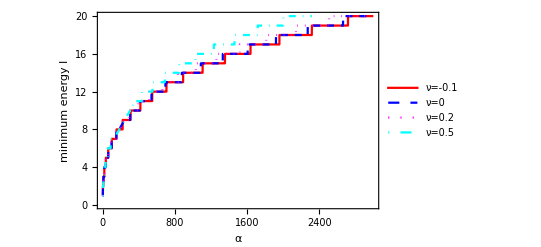

```mathematica
Plot[{lmini[α,-0.1,1],lmini[α,0.0,1],lmini[α,0.2,1],lmini[α,0.5,1]},{α,0,3000},Frame->True,PlotStyle->{{Red},{Blue, Dashed},{Magenta, Dotted},{Cyan, DotDashed}},PlotRange->{{0,3000},{0,20}},FrameLabel-> {Style[α,15],Style["minimum energy l",15]}, PlotLegends->Placed[{"ν=-0.1","ν=0","ν=0.2","ν=0.5"},{0.8,0.4}]]
```

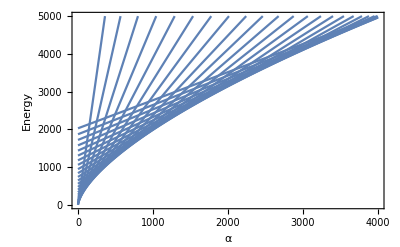

```mathematica
Plot[mytablei[α,0.2,1],{α,0,4000},PlotRange->{{0,4000},{0,5000}},Frame->True,FrameLabel-> {Style[α,15],Style["Energy",15]}]
```

```mathematica
(*κ=μR^3/α*)
```

```mathematica
(*critical fractional excess area*)  
Deltai[α_,ν_,R_]:=Energyi[α,ν,R]/(π *α* (1+ν)/(1-2ν))
```

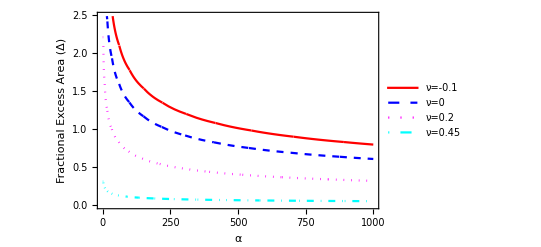

```mathematica
pdeltai=Plot[{Deltai[α,-0.1,1],Deltai[α,0.0,1],Deltai[α,0.2,1],Deltai[α,0.45,1]},{α,0,1000},FrameLabel->{Style["α",15],Style["Fractional Excess Area (Δ)",15]},PlotStyle->{{Red},{Blue, Dashed},{Magenta, Dotted},{Cyan, DotDashed}},Frame->True,PlotLegends->{"ν=-0.1","ν=0","ν=0.2","ν=0.45"}]
```

```mathematica
EnergyDensityI[l_,m_,R_,g_,ν_,r_]:=1/(4 Pi)*Simplify[Simplify[2*( EpsxyiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxyiVector0[l,m,R,g,ν,r]]
+EpsyziVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyziVector0[l,m,R,g,ν,r]]
+EpszxiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszxiVector0[l,m,R,g,ν,r]])+(1-ν)/(1-2ν)*(EpsxxiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxiVector0[l,m,R,g,ν,r]]
+ EpsyyiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyiVector0[l,m,R,g,ν,r]]
+ EpszziVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszziVector0[l,m,R,g,ν,r]])+2*ν/(1-2ν)*(EpsxxiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyiVector0[l,m,R,g,ν,r]]+EpsyyiVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszziVector0[l,m,R,g,ν,r]]+EpszziVector0[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxiVector0[l,m,R,g,ν,r]])]+Simplify[2*( EpsxyiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxyiVector2[l,m,R,g,ν,r]]
+EpsyziVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyziVector2[l,m,R,g,ν,r]]
+EpszxiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszxiVector2[l,m,R,g,ν,r]])+(1-ν)/(1-2ν)*(EpsxxiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxiVector2[l,m,R,g,ν,r]]
+ EpsyyiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyiVector2[l,m,R,g,ν,r]]
+ EpszziVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszziVector2[l,m,R,g,ν,r]])+2*ν/(1-2ν)*(EpsxxiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsyyiVector2[l,m,R,g,ν,r]]+EpsyyiVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpszziVector2[l,m,R,g,ν,r]]+EpszziVector2[l,m,R,g,ν,r].MatrixAll1[m].Transpose[EpsxxiVector2[l,m,R,g,ν,r]])],Assumptions->{R>0} ][[1]][[1]];
```

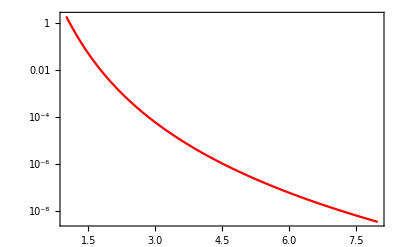

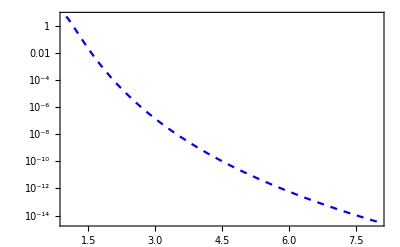

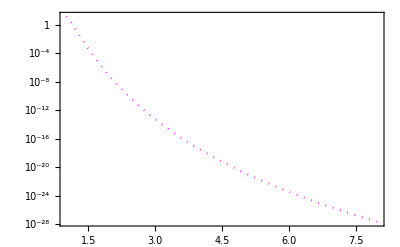

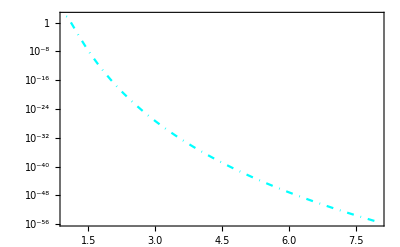

-Graphics-

```mathematica
pi4log=Plot[{EnergyDensityI[4,4,1,1,0.2,r]},{r,1,8},PlotStyle->{Red},Frame->True,PlotRange->Full,ScalingFunctions-> "Log"]
pi8log=Plot[{EnergyDensityI[8,8,1,1,0.2,r]},{r,1,8},PlotStyle->{{Blue,Dashed}},Frame->True,PlotRange->Full,ScalingFunctions-> "Log"]
pi16log=Plot[{EnergyDensityI[16,16,1,1,0.2,r]},{r,1,8},PlotStyle->{{Magenta,Dotted}},Frame->True,PlotRange->Full,ScalingFunctions-> "Log"]
pi32log=Plot[{EnergyDensityI[32,32,1,1,0.2,r]},{r,1,8},PlotStyle->{{Cyan,DotDashed}},Frame->True,PlotRange->Full,ScalingFunctions-> "Log"]
pilog=Plot[-10,{x,1,1.6},FrameLabel->{Style["r",15],Style["Energy Density",15]},Frame->True,PlotRange-> {{1,1.6},{5*^-2,60}},ScalingFunctions-> "Log"]
```

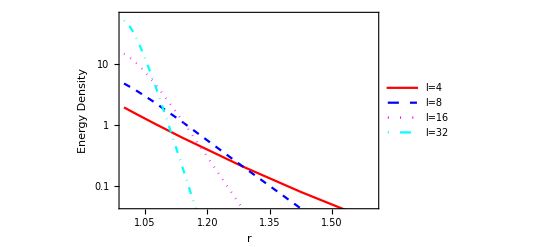

```mathematica
Legended[Show[pilog,pi4log,pi8log,pi16log,pi32log],Placed[LineLegend[{Red,{Blue,Dashed},{Magenta,Dotted},{Cyan,DotDashed}},{"l=4","l=8","l=16","l=32"}],{0.8,0.55}]]
```

```mathematica
(*Coefficients A_{m+/-1}, B_{m+/-1}, ..., P, Q, S in the paper*)
```

```mathematica
Amp1[l_,m_,R_,g_,ν_]=A1[l,m,R,g,ν]/R;
Amm1[l_,m_,R_,g_,ν_]=A2[l,m,R,g,ν]/R;
Bmp1[l_,m_,R_,g_,ν_]=A5[l,m,R,g,ν]/R;
Bmm1[l_,m_,R_,g_,ν_]=A6[l,m,R,g,ν]/R;
Cmp1[l_,m_,R_,g_,ν_]=A9[l,m,R,g,ν]/R;
Cmm1[l_,m_,R_,g_,ν_]=A10[l,m,R,g,ν]/R;
Dmp1[l_,m_,R_,g_,ν_]=B1[l,m,R,g,ν]/R;
Dmm1[l_,m_,R_,g_,ν_]=B2[l,m,R,g,ν]/R;
Emp1[l_,m_,R_,g_,ν_]=B5[l,m,R,g,ν]/R;
Emm1[l_,m_,R_,g_,ν_]=B6[l,m,R,g,ν]/R;
Fmp1[l_,m_,R_,g_,ν_]=B9[l,m,R,g,ν]/R;
Fmm1[l_,m_,R_,g_,ν_]=B10[l,m,R,g,ν]/R;
Icoeff[l_,m_,R_,g_,ν_]=C2[l,m,R,g,ν]/R;
H[l_,m_,R_,g_,ν_]=C4[l,m,R,g,ν]/R;
G[l_,m_,R_,g_,ν_]=C6[l,m,R,g,ν]/R;
Jmp1[l_,m_,R_,g_,ν_]=A1i[l,m,R,g,ν]/R;
Jmm1[l_,m_,R_,g_,ν_]=A2i[l,m,R,g,ν]/R;
Kmp1[l_,m_,R_,g_,ν_]=A5i[l,m,R,g,ν]/R;
Kmm1[l_,m_,R_,g_,ν_]=A6i[l,m,R,g,ν]/R;
Lmp1[l_,m_,R_,g_,ν_]=A9i[l,m,R,g,ν]/R;
Lmm1[l_,m_,R_,g_,ν_]=A10i[l,m,R,g,ν]/R;
Mmp1[l_,m_,R_,g_,ν_]=B1i[l,m,R,g,ν]/R;
Mmm1[l_,m_,R_,g_,ν_]=B2i[l,m,R,g,ν]/R;
Nmp1[l_,m_,R_,g_,ν_]=B5i[l,m,R,g,ν]/R;
Nmm1[l_,m_,R_,g_,ν_]=B6i[l,m,R,g,ν]/R;
Omp1[l_,m_,R_,g_,ν_]=B9i[l,m,R,g,ν]/R;
Omm1[l_,m_,R_,g_,ν_]=B10i[l,m,R,g,ν]/R;
S[l_,m_,R_,g_,ν_]=C2i[l,m,R,g,ν]/R;
Q[l_,m_,R_,g_,ν_]=C4i[l,m,R,g,ν]/R;
P[l_,m_,R_,g_,ν_]=C6i[l,m,R,g,ν]/R;
```